## Utils

```mathematica
SetDirectory["C:\\Users\\drezn\\Dropbox\\Mathematica\\Billiards"];
newCentersFromFile=Get["data/x0001_0100-no-hold.m"]; 
(*//Drop[#,{30}]&;*)(*EULER INFINITY POINT*)
```

```mathematica
toDeg[r_]:=180.*r/π;
toRad[d_]:=π*d/180.;
Clear@negl;negl[v_]:=Abs[v]<10^-9;
Clear@safeDiv;
safeDiv[num_,denom_]:=If[negl[denom],0,num/denom];
magn2[v_]:=v.v;
magn[v_]:=Sqrt[magn2[v]];
flipY[{x_,y_}]:={x,-y};
flipX[{x_,y_}]:={-x,y};
perp[{x_,y_}]:={-y,x};
perpNeg[{x_,y_}]:={y,-x};
crossProduct[{x1_,y1_},{x2_,y2_}]:=-x2 y1 + x1 *y2;
refl[v_,n_]:=2(v.n)n/magn2[n]-v;
norm[v_]:=v/magn[v];
clamp[v_,max_:100]:=If[v>max,max,If[v<-max,-max,v]];
ray[p0_,phat_,d_]:=p0+phat*d;
Clear@rot;
rot[p_,st_,ct_]:=Module[{m},
m={{ct,-st},{st,ct}};
m.p];
rot[p_,t_]:=rot[p,Sin@t,Cos@t];
rotRel[p_,t_,p0_]:=p0+rot[p-p0,t];
getEquilateral[th_]:=Module[{s=Sin[2π/3.],c=Cos[2π/3.]},
NestList[rot[#,s,c]&,rot[{1.,0.},Sin@th,Cos@th],2]];
```

```mathematica
subscriptTxt[prefix_,sub_]:=ToString[Subscript[prefix,sub],StandardForm];
subscriptTxtClr[prefix_,sub_,clr_]:=ToString[Style[Subscript[prefix,sub],clr],StandardForm];
padZ[v_,n_:4]:=ToString@NumberForm[v,{n,0},NumberPadding->{"0",""},NumberPoint->""];
```

```mathematica
closestPerp[p_,l1_,l2_]:=Module[{dl=l2-l1,s},
s=safeDiv[(p-l1).dl,dl.dl];
ray[l1,dl,s]];
```

```mathematica
Clear@quadRoots;
quadRoots[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
If[det<0,Print["quadRoots fail: {a,b,c}="<>ToString@{a,b,c}];False,
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)]];
Clear@interRays;
interRays[p1_,n1_,p2_,n2_]:=Module[{m,b,sols},
m=Transpose[{n1,n2}];(*{{nx1,-nx2},{ny1,-ny2}};*)
If[negl[Det[m]],p1,
b=p2-p1;(*{x2-x1,y2-y1}];*)
sols=LinearSolve[m,b];
ray[p1,n1,sols[[1]]]]
];
interRaysIllConditioned[n1_,n2_]:=negl@Det@Transpose@{n1,n2};
interRaysUnprot[p1_,n1_,p2_,n2_]:=Module[{m,b,sols},
m=Transpose@{n1,n2};(*{{nx1,-nx2},{ny1,-ny2}};*)
b=p2-p1;(*{x2-x1,y2-y1}];*)
sols=LinearSolve[m,b];
ray[p1,n1,sols[[1]]]
];
```

```mathematica
Second[l_]:=l[[2]];
Third[l_]:=l[[3]];
Fourth[l_]:=l[[4]];
Fifth[l_]:=l[[5]];
Sixth[l_]:=l[[6]];
Seventh[l_]:=l[[7]];
Eighth[l_]:=l[[8]];
Nineth[l_]:=l[[9]];
```

```mathematica
signedArea[poly_]:=(1/2)Total@MapThread[(#1[[1]]#2[[2]]-#2[[1]]#1[[2]])&,{poly,RotateLeft@poly}];
```

#### Triangles

```mathematica
Clear@s;
```

```mathematica
cosHalfAngle[cosAngle_]:=Sqrt[(1.+cosAngle)/2];(* careful: plus or minus *)
sinHalfAngle[cosAngle_]:=Sqrt[(1.-cosAngle)/2];
tanHalfAngle[sinAngle_,cosAngle_]:=sinAngle/(1+cosAngle);
(* careful: plus or minus *)
cosDoubleAngle[cosAngle_]:=2*cosAngle*cosAngle-1.; (* cA^2-sA^2 = 2 cA^2-1 *)
sinDoubleAngle[sinAngle_]:=2*sinAngle*Sqrt[1.-sinAngle^2];(* 2 sA cA *)
sinDoubleAngle[sinAngle_,cosAngle_]:=2*sinAngle*cosAngle;(* 2 sA cA *)
(* gives cos(A) *)
lawOfCosines[a_,b_,c_]:=(b^2+c^2-a^2)/(2.b c);
lawOfCosines3[a_,b_,c_]:={lawOfCosines[a,b,c],lawOfCosines[b,c,a],lawOfCosines[c,a,b]};
getSin[theCos_]:=Sqrt[1.-theCos^2];
lawOfCosinesSymbol[a_,b_,c_]:=(b^2+c^2-a^2)/(2b c);
getSinSymbol[theCos_]:=Sqrt[1-theCos^2];
(* cos(3t) = cos(2t+t) = c2 c - s2t s; *)
(* sin(3t) = sin(2t+t) = s2 c + s c2 *)
sinCosTripleAngle[s_,c_,s2_,c2_]:=Module[{s3,c3},
c3=c2 c-s2 s;
s3=s2 c+s c2;
{s3,c3}];
cosTripleAngle[c_]:=4c^3-3c;
getSinCosApB[sa_,sb_,ca_,cb_]:={sa cb + sb ca ,ca cb - sa sb};
getSinCosAmB[sa_,sb_,ca_,cb_]:= {sa cb - sb ca,ca cb + sa sb};
getSinApmB[sa_,sb_,ca_,cb_]:= {sa cb + sb ca,sa cb - sb ca};
```

```mathematica
testCosTriple[t_]:=Module[{c,s3,c3,c3a,s,c2,s2},
{c,s}={Cos@t,Sin@t};
c3a=cosTripleAngle[c];
c2=cosDoubleAngle[c];
s2=sinDoubleAngle[s,c];
{s3,c3}=sinCosTripleAngle[s,c,s2,c2];
{c3a,c3}];
```

```mathematica
(*Plot[testCosTriple[t],{t,0,2π}]*)
```

```mathematica
cosDiffAngle[sa_,ca_,sb_,cb_]:=ca cb+sa sb;
cosSumAngle[sa_,ca_,sb_,cb_]:=ca cb-sa sb;
(* compute sin^2(A/2), by passing cosA *)
sin2HalfAngle[cosAngle_]:=(1-cosAngle)/2;(* sinHalfAngle[cos]^2 *)
cos2HalfAngle[cosAngle_]:=(1+cosAngle)/2;(* cosHalfAngle[cos]^2 *)
```

```mathematica
Clear@cosThird;
cosThird[cos_]:=Chop@N@Re[Module[{sin=Sqrt[1-cos^2]},
((cos+I sin)^(-1/3)+(cos+I sin)^(1/3))/2]];
```

```mathematica
Clear@getBisector;
getBisector[vbase_,v1_,v2_]:=Module[{v01,v02},
v01=norm[v1-vbase];
v02=norm[v2-vbase];
norm[v01+v02]];
```

```mathematica
Clear@getTriBisectors;
getTriBisectors[p1_,p2_,p3_]:=Module[{u12,u23,u31},
u12=norm[p2-p1];
u23=norm[p3-p2];
u31=norm[p1-p3];
{
norm[u12-u31],
norm[u23-u12],
norm[u31-u23]
}
];
```

```mathematica
export3[name_,plot_]:=Module[{subdir="pics/"},
Export[subdir<>name<>".pdf",plot];
Export[subdir<>name<>".eps",plot];
Export[subdir<>name<>".png",plot];
];
```

```mathematica
export4[name_,plot_]:=Module[{subdir="pics/"},
Export[subdir<>name<>".pdf",plot];
Export[subdir<>name<>".eps",plot];
Export[subdir<>name<>".png",plot];
Export[subdir<>name<>".svg",plot];
];
```

#### Circle

-Graphics-

```mathematica
Clear@circleInter;
circleInter[c1_,r1_,c2_,r2_]:=Module[{d,x,y,chat},
d=magn[c2-c1];
chat=(c2-c1)/d;
x=(d^2-r2^2+r1^2)/(2d);
y=Sqrt[r1^2-x^2];
{c1+x chat+y perp[chat],c1+x chat-y perp[chat]}];
```

```mathematica
Manipulate[Module[{is},
is=circleInter[c1,1,c2,1.5];
Graphics[{Circle[c1,1],Circle[c2,1.5],Red,PointSize@Large,Point@is},PlotRange->{{-2,2},{-2,2}}]],
{{c1,{-1,-.5}},Locator},
{{c2,{1.25,.25}},Locator}]
```

#### Ellipse

```mathematica
Solve[(x/a)^2+(y/b)^2==1 ,y]//FullSimplify[#,a>0]&
```

{{y→-(b √((a-x) (a+x)))/a},{y→(b √((a-x) (a+x)))/a}}

```mathematica
ellEqn[a_,x_,y_]:=(x/a)^2+y^2-1;
ellEqnb[a_,b_,x_,y_]:=(x/a)^2+(y/b)^2-1;
ellGrad[a_,x_,y_]:=-{x,y a^2};(* (x/a)^2+y^2==1 *)
ellGradb[a_,b_,x_,y_]:=-2{x/a^2,y/b^2};(* (x/a)^2+y^2==1 *)
ellY[a_,x_]:=Sqrt[1-(x/a)^2];
ellYb[a_,b_,x_]:=b Sqrt[1-(x/a)^2];(*(x/a)^2+(y/b)^2==1 *);
ellError[a_,b_,{x_,y_}]:=(x/a)^2+(y/b)^2-1;
Clear@eccentricity;eccentricity[a_,b_]:=Sqrt[1-(b/a)^2];
ellPerimeterRamanujan2[a_,b_]:=Module[{h=((a-b)/(a+b))^2},
π(a+b)(1+3h/(10+Sqrt[4-3h]))];
ellPerimeterRamanujan[a_,b_]:=π(3(a+b)-Sqrt[(3a+b)(a+3b)]);
ellPerimeter[a_,b_]:=Module[{ecc=eccentricity[a,b]},4*a*EllipticE[ecc^2]];
ellArea[a_,b_]:=π a b;
focalDistance[a_,b_]:=Sqrt[a^2-b^2];
Clear@getFoci;getFoci[a_]:=Module[{c},If[a<1,c=Sqrt[1-a^2];{{0,c},{0,-c}},c=Sqrt[a^2-1];{{-c,0},{c,0}}]];
getFocib[a_,b_]:=b*getFoci[a/b];
```

```mathematica
(*ellRayCoeffs=Module[{r,eqn,sols},
r=ray[{x,y},{nx,ny},s];
eqn=FullSimplify[ellEqn[a,r[[1]],r[[2]]],Assumptions->a>0&&Abs[x]<=a&&(nx^2+ny^2==1)];
FullSimplify[a^2 CoefficientList[eqn,s],a>0]]*)
```

```mathematica
Clear@ellInterRay;
ellInterRay[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRoots[c2,c1,c0];
If[ListQ[ss],
ray[{x,y},{nx,ny},#]&/@ss,
{{0,0},{0,0}}]
];
```

Used for Proofs

```mathematica
quadRootsUnprot[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)];Clear@ellInterRayUnprot;

ellInterRayUnprot[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRootsUnprot[c2,c1,c0];
ray[{x,y},{nx,ny},#]&/@ss
];
```

```mathematica
(*ellRayCoeffsB=Module[{r,eqn,sols},
r=ray[{x,y},{nx,ny},s];
eqn=FullSimplify[ellEqnb[a,b,r[[1]],r[[2]]],Assumptions->a>0&&b>0&&Abs[x]<=a&&(nx^2+ny^2==1)];
Together/@FullSimplify[CoefficientList[eqn,s],a>0&&b>0]]*)
```

```mathematica
ellInterRaybUnprot[a_,b_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=b^2 nx^2+a^2 ny^2;
c1=2 (b^2 nx x+a^2 ny y);
c0=-a^2 b^2+b^2 x^2+a^2 y^2;
ss=quadRootsUnprot[c2,c1,c0];
ray[{x,y},{nx,ny},#]&/@ss
];
```

```mathematica
Clear@ellInterRaybUnprotAny;
ellInterRaybUnprotAny[a_,b_,ctr_,axisA_,axisB_,p_,dir_]:=Module[{m,p0,dir0,inter0},
m={axisA,axisB};
p0=m.(p-ctr);
dir0=m.dir;
inter0=ellInterRaybUnprot[a,b,p0,dir0];
(Transpose[m].#+ctr)&/@inter0];
```

```mathematica
DynamicModule[{gr,xmax=2,ymax=2,axis1,axis2,t,interP1P2,lgt=.33},
Manipulate[
t=toRad@tDeg;
axis1={Cos@t,Sin@t};
axis2=perp@axis1;
interP1P2=ellInterRaybUnprotAny[a,b,ctr,axis1,axis2,p1,p2-p1];
gr=Graphics[{PointSize@Medium,
{Arrowheads@Medium,Arrow@{ctr,ctr+lgt axis1},Arrow@{ctr,ctr+lgt axis2}},
{Rotate[{Circle[ctr,{a,b}],Dashed,Line@{{-a,0},{a,0}},Line@{{0,-b},{0,b}}},t]},
{PointSize@Large,Blue,Point@interP1P2[[1]],Red,Point@interP1P2[[2]],Black,Line@interP1P2}
}];
Show[{gr},PlotRange->{{-xmax,xmax},{-ymax,ymax}}],
{{a,1.5},.5,2,.1,Appearance->"Labeled"},
{{b,1},.5,2,.1,Appearance->"Labeled"},
{{tDeg,30,"θ"},-180,180,.1,Appearance->"Labeled"},
{{ctr,{0,0}},Locator},
{{p1,{.5,.75}},Locator},
{{p2,{-.5,.25}},Locator}]]
```

```mathematica
(* works for circle: a==1 *)
Clear@ellTangents;
ellTangents[a_,p_]:=Module[{a2,px,py,px2,px3,py2,radicand,numFact,denomx,denomy},
{px,py}=p;
a2=a*a;
px2=px*px;py2=py*py;
px3=px*px2;
denomx=px3+a2 px py2;
denomy=px2+a2 py2;
radicand=px2+a2(py2-1);
numFact=Sqrt[radicand]*Abs[px];
(*["radicand=",radicand,", numFact=",numFact,", dx=",denomx,", dy=",denomy];*)
(* NOTE: the first one is Clockwise, the 2nd one is CCW *)
{{a2 safeDiv[px2+py numFact,denomx],safeDiv[a2 py-numFact,denomy]},
{a2 safeDiv[px2-py numFact,denomx],safeDiv[a2 py+numFact,denomy]}}
];
```

```mathematica
(* hack *)
(*tangsToCirc[ctr_,r_,p_]:=(ctr+r#)&/@ ellTangents[1.,(p-ctr)/r];*)
```

```mathematica
Clear@ellTangentsb;
ellTangentsb[a_,b_,p_]:=
Module[{a2,b2,px,py,px2,px3,py2,py3,radicand,numFact,denomx,denomy},
{px,py}=p;
a2=a*a;
b2=b*b;
px2=px*px;py2=py*py;
px3=px*px2;py3=py*py2;
denomx=b2 px2 +a2 py2;
denomy=b2 px2 py+a2 py3;
radicand= b2 px2+a2(py2-b2);
numFact=Sqrt[radicand]*Abs[py];
(*Print["radicand=",radicand,", numFact=",numFact,", dx=",denomx,", dy=",denomy];*)
(* NOTE: Reverse[] so first one is Clockwise, the 2nd one is CCW *)
Reverse@{{a2 safeDiv[b2 px- numFact,denomx],b2 safeDiv[a2 py2+px numFact,denomy]},
{a2 safeDiv[b2 px+ numFact,denomx],b2 safeDiv[a2 py2-px numFact,denomy]}}
];
```

-Graphics--Graphics-

```mathematica
Clear@tangsToCirc;
tangsToCirc[ctr_,R_,P_]:=Module[{d,t1,t2,xhat,yhat},
d=magn[P-ctr];
xhat=(P-ctr)/d;
yhat=perp[xhat];
If[d<R,t1=ctr+R xhat;{t1,t1},
t1={R,Sqrt[d^2-R^2]}/d;
t2=flipY@t1;
(ctr+R#.{xhat,yhat})&/@{t1,t2}]];
```

```mathematica
DynamicModule[{ts,gr},
Manipulate[
ts=tangsToCirc[ctr,R,P];
gr=Graphics[{PointSize@Large,Thick,
{Circle[ctr,R],Point@ctr,Point@P,Line@{ctr,P}},
{Red,Point@ts,Dashed,Line@{P,#}&/@ts,Line@ts},
MapThread[Text[Style[#1,20],#2,{-1.5,-1.5}]&,{{"O","P"},{ctr,P}}]}];
Show[{gr},PlotRange->{{-1.1,3},{-2,2}}],
{{R,1},.1,2,.01},
{{ctr,{0,0}},Locator},
{{P,{2,0}},Locator}]]
```

#### Hyperbola

```mathematica
hypC[a_,b_]:=a^2+b^2;
hypEqn[a_,b_,{x_,y_}]:=(x/a)^2-(y/b)^2==1;
hypErr[a_,b_,{x_,y_}]:=(x/a)^2-(y/b)^2-1;
hypGrad[a_,b_,{x_,y_}]:=-{x b^2,-y a^2};
```

```mathematica
hypParam[a_,b_,t_]:=Module[{x,y},
x=a Cosh[t];
y=b Sinh[t];
{{x,y},{-x,-y}}];
```

#### Triangles

```mathematica
Clear@triSides;triSides[vs_]:=MapThread[(#1-#2)&,{vs,RotateLeft@vs}];
Clear@triLengths;triLengths[vs_]:=magn/@triSides[vs];
Clear@triLengthsRL;triLengthsRL[vs_]:=RotateLeft@triLengths@vs;
triPer[tri_]:=Total[triLengths@tri];
(* a,b,c are side lengths *)
Clear@triAreaHeron;triAreaHeron[{a_,b_,c_}]:=Module[{s},
s=(a+b+c)/2;(* semi perimeter *)
Sqrt[s*(s-a)*(s-b)*(s-c)]];
(* order by oposition to vertices *)
getMedians[t1_,t2_,t3_]:={t2+t3,t1+t3,t1+t2}/2;
getMediansV[vs_]:=.5(vs+RotateLeft@vs);
```

```mathematica
Clear@getInradius;getInradius[{a_,b_,c_}]:=Module[{num1,num2,num3,denom},
num1=b+c-a;
num2=c+a-b;
num3=a+b-c;
denom=a+b+c;
Sqrt[num1*num2*num3/denom]/2];
```

```mathematica
getCircumradius[{a_,b_,c_}]:=Module[{s,num,denom1,denom2,denom3},
s=(a+b+c)/2;
num=a*b*c;
denom1=(a+b-s);
denom2=(a+c-s);
denom3=(b+c-s);
num/(4*Sqrt[s*denom1*denom2*denom3])];
```

```mathematica
getNinepointCircleRadius[sides_]:=getCircumradius[sides]/2;
```

```mathematica
getTriData[tri_]:=Module[{sides,perimeter,inc,inradius,circumradius,cosines,bisectors,area},
sides=RotateLeft@triLengths@tri;
perimeter=Total@sides;
inradius=getInradius[sides];
circumradius=getCircumradius[sides];
cosines=getTriCosines[tri];
bisectors=getTriBisectors@@tri;
area=inradius*perimeter/2;
{"sides"->sides,
"perimeter"->perimeter,
"inradius"->inradius,
"circumradius"->circumradius,
"rOvR"->inradius/circumradius,
"cosines"->cosines,
"area"->area,
"bisectors"->bisectors}];
```

```mathematica
getSubtriData[tri_]:=Module[{sides,inc,tps,incR,npc,npcR},
sides=triLengthsRL@tri;
inc=getIncenterTrilin[tri,sides];
(* the intouchpoints of this guy is on the billiard, needs to draw them *)
tps=intouchTriangle[tri,sides];
incR=getInradius[sides];
npc=getNinepointCenterTrilin[tri,sides];
npcR=getNinepointCircleRadius[sides];
<|"tri"->tri,"sides"->sides,"inc"->inc,"incR"->incR,"npc"->npc,"npcR"->npcR,"tps"->tps|>];
```

```mathematica
Clear@getAnticomplData;
getAnticomplData[orbit_,sides_]:=
getSubtriData@anticomplementaryTriangle[orbit,sides];
```

```mathematica
Clear@getMedialData;
getMedialData[orbit_,sides_]:=
getSubtriData@medialTriangle[orbit,sides];
```

```mathematica
getIncenterAxes[a_]:=Module[{δ,a1,b1},
δ=Sqrt[a^4-a^2+1];
a1=(δ-1)/a;b1=(a^2-δ);
{a1,b1}];
```

```mathematica
getExcenterAxes[a_]:=Module[{δ,ae,be},
δ=Sqrt[a^4-a^2+1];
ae=(δ+1)/a;be=(a^2+δ);
{ae,be}];
```

```mathematica
Clear@getCircularity;
getCircularity[locus_]:=Module[{rads,ctr,mean,sd},
(* assume it's zero since points may not be evenly distributed so "mean" won't work and RegionCentroid is too slow *)
ctr={0,0};
rads=magn[#-ctr]&/@locus;
mean=Mean@rads;
sd=StandardDeviation@rads;
{
"n"->Length@locus,
"ctr"->ctr,
"min"->Min@rads,
"max"->Max@rads,
"mean"->mean,
"sd"->sd,
"zscore"->sd/mean
}];
```

```mathematica
Clear@txtSubscript;
txtSubscript[txt_,subscr_,style_,where_,offset_:{0,0}]:=Text[Style[Subscript[txt,subscr],style],where,offset];
Clear@txtSuperSub;
txtSuperSub[txt_,superscr_,subscr_,style_,where_,offset_:{0,0}]:=Text[Style[Subsuperscript[txt,subscr,superscr],style],where,offset];
Clear@txtSubscriptSuffix;
txtSubscriptSuffix[txt_,subscr_,suffix_,style_,where_,offset_:{0,0}]:=Text[Style[ToString[Subscript[txt,subscr],FormatType->StandardForm]<>suffix,style],where,offset];
```

```mathematica
Clear@ellLabel;
Options@ellLabel={inward->False};
ellLabel[a_,p_,lgt_,OptionsPattern[]]:=p+If[OptionValue@inward,lgt,-lgt]*norm[ellGrad[a,Sequence@@p]];
Clear@ellLabelb;
Options@ellLabelb={inward->False};
ellLabelb[a_,b_,p_,lgt_,OptionsPattern[]]:=p+If[OptionValue@inward,lgt,-lgt]*norm@ellGradb[a,b,Sequence@@p];
Clear@ellLabelTxt;
Options@ellLabelTxtb={inward->False};
ellLabelTxtb[a_,b_,p_,txt_,lgt_,opts:OptionsPattern[]]:=Text[txt,ellLabelb[a,b,p,lgt,{opts}]];
Clear@ellLabelTxt;
Options@ellLabelTxt={inward->False};
ellLabelTxt[a_,p_,txt_,lgt_,opts:OptionsPattern[]]:=Text[txt,ellLabel[a,p,lgt,{opts}],{0,0}];
```

```mathematica
Clear@labelPoints;labelPoints[pts_,prefix_,style_,offset_:{0,0}]:=MapThread[txtSubscript[prefix,#1,style,#2,offset]&,{Range@Length@pts,pts}];
Clear@ellLabelPoints;
ellLabelPoints[a_,pts_,prefix_,style_,lgt_:.33]:=MapThread[txtSubscript[prefix,#1,style,ellLabel[a,#2,lgt]]&,{Range@Length@pts,pts}];
ellLabelPointsSuperSub[a_,pts_,prefix_,super_,style_,lgt_:.33]:=MapThread[txtSuperSub[prefix,super,#1,style,ellLabel[a,#2,lgt]]&,{Range@Length@pts,pts}];
ellLabelPointsSuffix[a_,pts_,prefix_,suffixes_,style_,lgt_:.33]:=MapThread[txtSubscriptSuffix[prefix,#1,#3,style,ellLabel[a,#2,lgt]]&,{Range@Length@pts,pts,suffixes}];
Clear@ellLabelPointsSuffixb;ellLabelPointsSuffixb[a_,b_,pts_,prefix_,suffixes_,style_,lgt_:.33]:=MapThread[txtSubscriptSuffix[prefix,#1,#3,style,ellLabelb[a,b,#2,lgt]]&,{Range@Length@pts,pts,suffixes}];
Clear@ellLabelPointsb;
ellLabelPointsb[a_,b_,pts_,prefix_,style_,lgt_:.33]:=MapThread[txtSubscript[prefix,#1,style,ellLabelb[a,b,#2,lgt]]&,{Range@Length@pts,pts}];
Clear@ellLabelPointsbInward;
ellLabelPointsbInward[a_,b_,pts_,prefix_,style_,lgt_:.33]:=MapThread[txtSubscript[prefix,#1,style,ellLabelb[a,b,#2,lgt,inward->True]]&,{Range@Length@pts,pts}];
```

```mathematica
Clear@getStats;
Options@getStats={label->""};
getStats[vals_,OptionsPattern[]]:=Module[{mean,sd,z},
mean=Mean@vals;
sd=StandardDeviation@vals;
z=safeDiv[sd,mean];
<|"n"->Length@vals,"mean"->mean,"sd"->sd,"z"->z,"min"->Min@vals,"max"->Max@vals,"median"->Median@vals,"label"->OptionValue@label|>];
```

Formatting

```mathematica
nfn[v_,n_]:=ToString@NumberForm[v,{n+2,n}];
nf[v_]:=ToString@NumberForm[v,{3,2}];
nf1[v_]:=ToString@NumberForm[v,{3,1}];
nf0[v_]:=ToString@IntegerPart[v];
padZ[v_,n_:4]:=ToString@NumberForm[v,{n,0},NumberPadding->{"0",""},NumberPoint->""];
```

```mathematica
Clear@getBilliardAngle;
getBilliardAngle[a_,b_,{px_,py_}]:=
ArcTan[px/a,py/b];
```

-Graphics-

```mathematica
stereographicProj[x_,y_]:=Module[{c=x*x+y*y},
{2x,2y,c-1}/(c+1)];
```

#### imagine point at (x0, y0, 1), on plane tangent and above sphere x^2+y^2+z^2=1. line from center to point: p(t) = t (x0,y0,1) p(t) on sphere ⇔ t^2 (x0^2+y0^2+1) = 1 ⇒ t^2=1/(...) ⇒ p = (x0,y0,1)/sqrt(x0^2+y0^2+1) = (x0,y0,1)/α

-Graphics-

### r = 1, z=1/α ⇒ θ = arccos(1/α) y/x=tan[ϕ] ⇒ ϕ = arctan[y/x] = arctan[y0/x0]

```mathematica
sphereProj[x0_,y0_]:=Module[{α=Sqrt[x0^2+y0^2+1]},
{1/α,y0/x0}]
```

```mathematica
sphereProj2[x0_,y0_]:=Module[{α=x0^2+y0^2},
{x0,y0}/α]
```

```mathematica
sphereProj3[x0_,y0_]:=Module[{α=x0^2+y0^2},
{x0,y0}/Sqrt@α]
```

```mathematica
logProj[x0_,y0_]:=Module[{α=Log[1+x0^2+y0^2]},
{x0,y0}/α]
```

```mathematica
Clear@makeMovie;
makeMovie[fname_,frames_,repeats_:3]:=Module[{framesConcat},
framesConcat=Flatten@ConstantArray[frames,repeats];
Print["Exporting "<>ToString@Length[framesConcat]<>" frames to "<>fname];
Export[fname,framesConcat,"VideoEncoding"->"MPEG-4 Video"];
];
```

#### Envelope Aux [most code on companion envelopes.nb]

```mathematica
Clear@getEnvelope;(* via intersection *)
Options@getEnvelope={epsDeg->.001,tDeg2Phase->0};
getEnvelope[a_?NumericQ,tDeg_?NumericQ,trilfn1_,trilfn2_,OptionsPattern[]]:=Module[{ons,onsPhase,p1,q1,p2,q2},
ons=orbitNormals[a,toRad@(tDeg-.5OptionValue@epsDeg)];
{p1,q1}=If[OptionValue@tDeg2Phase>0,
onsPhase=orbitNormals[a,toRad@(tDeg-.5OptionValue@epsDeg+OptionValue@tDeg2Phase)];
{trilfn1[ons[[1]],ons[[3]]],trilfn1[onsPhase[[1]],onsPhase[[3]]]},
#[ons[[1]],ons[[3]]]&/@{trilfn1,trilfn2}
];
ons=orbitNormals[a,toRad@(tDeg+.5OptionValue@epsDeg)];
{p2,q2}=If[OptionValue@tDeg2Phase>0,
onsPhase=orbitNormals[a,toRad@(tDeg+.5OptionValue@epsDeg+OptionValue@tDeg2Phase)];
{trilfn1[ons[[1]],ons[[3]]],trilfn1[onsPhase[[1]],onsPhase[[3]]]},
#[ons[[1]],ons[[3]]]&/@{trilfn1,trilfn2}
];
interRaysUnprot[p1,(q1-p1),p2,(q2-p2)]];
```

```mathematica
Clear@getEnvelopeb;
getEnvelopeb[a_?NumericQ,b_?NumericQ,tDeg_?NumericQ,trilfn1_,trilfn2_,epsDeg_:.001]:=Module[{ons,p1,q1,p2,q2},
ons=orbitNormalsb[a,b,toRad@tDeg];{p1,q1}=#[ons[[1]],ons[[3]]]&/@{trilfn1,trilfn2};
ons=orbitNormalsb[a,b,toRad@(tDeg+epsDeg)];{p2,q2}=#[ons[[1]],ons[[3]]]&/@{trilfn1,trilfn2};
interRaysUnprot[p1,(q1-p1),p2,(q2-p2)]];
```

```mathematica
(* new *)Clear@getEnvelopeLocus;
Options@getEnvelopeLocus=Options@getEnvelope;
getEnvelopeLocus[a_,trilinFn1_,trilinFn2_,ps_,opts:OptionsPattern[]]:=Module[{pp,ons},
pp=Quiet@ParametricPlot[ons=orbitNormals[a,toRad@tDeg];getEnvelope[a,tDeg,trilinFn1,trilinFn2,FilterRules[{opts},Options@getEnvelope]],{tDeg,0,360},
PerformanceGoal->"Speed",PlotStyle->ps]];
```

```mathematica
rayCircTs=Normal/@(t/.FullSimplify[Solve[magn2[{x0,y0}+{xhat,yhat} t-{ox,oy}]==R^2,t,Reals]])
```

{-(-ox xhat+x0 xhat-oy yhat+y0 yhat+√(-oy^2 xhat^2+2 oy xhat (xhat y0+(ox-x0) yhat)-(xhat y0+(ox-x0) yhat)^2+R^2 (xhat^2+yhat^2)))/(xhat^2+yhat^2),(ox xhat-x0 xhat+oy yhat-y0 yhat+√(-oy^2 xhat^2+2 oy xhat (xhat y0+(ox-x0) yhat)-(xhat y0+(ox-x0) yhat)^2+R^2 (xhat^2+yhat^2)))/(xhat^2+yhat^2)}

```mathematica
interRayCircTs[{x0_,y0_},{xhat_,yhat_},{ox_,oy_},R_]=rayCircTs;
```

```mathematica
interRayCirc[r0_,rhat_,ctr_,R_]:=Module[{ts},
ts=interRayCircTs[r0,rhat,ctr,R];
ray[r0,rhat,#]&/@ts];
```

```mathematica
colorStr[str_,clr_]:=ToString[Style[str,clr],StandardForm]
```

```mathematica
(* for organizing buttons in manipulate UI *)
makeCtrlCol[ctrls_]:=Column[{Style[First@ctrls,Bold,Medium],Sequence@@Rest[ctrls]},Alignment->Right,BaselinePosition->1];
```

## Ellipse Inversion, Isogonal and Isotomic Conjugates

-Graphics-
https://arxiv.org/pdf/1309.6378.pdf

```mathematica
Clear@ellInversion;
ellInversion[a_,p_]:=Module[{q,w,p2},
q=ellInterRayUnprot[a,{0,0},p][[2]];
w=q.q;
p2=p.p;
{p*w/p2,q}]
```

```mathematica
ellInversion[1.5,{.5,.5}]
```

{{1.38462,1.38462},{0.83205,0.83205}}

```mathematica
Manipulate[
DynamicModule[{a=1.5,ell,pinv,q,fs,gr},
{ell,fs}={plotEll[a],getFoci[a]};
Dynamic[{pinv,q}=ellInversion[a,p];
gr=Graphics[{PointSize@Large,Point@fs,Red,Point@pinv,Dashed,Line[{p,pinv}],Blue,Point@q}];
Show[{ell,gr},Frame->True,PlotRange->{{-2a,2a},{-2,2}},
PlotLabel->(Style["Inversion with Respect to Ellipse",{Black,Medium}])]]],
{{p,{.5,.5}},Locator},SaveDefinitions->True]
```

```mathematica
(*CloudDeploy[%,"inversion with respect to ellipse",Permissions->"Public"]*)
```

```mathematica
-Graphics--Graphics-
```

```mathematica
Clear@isogonalConjugate;
isogonalConjugate[p_,tri_,bisectors_]:=Module[{refla,reflb,inter},
refla=refl[p-First@tri,First@bisectors];
reflb=refl[p-Second@tri,Second@bisectors];
inter=interRaysUnprot[First@tri,refla,Second@tri,reflb];
inter];
```

```mathematica
(* could use cevianTriangle, but needs conversion from cartesian to trilinear *)
```

```mathematica
Clear@isotomicConjugate;
isotomicConjugate[p_,tri_]:=Module[{inters,meds,isos,n1,n2,n3,isoConj},
inters=MapThread[interRays[#1,p-#1,#2,#3-#2]&,{tri,RotateLeft@tri,RotateRight@tri}];
meds=getMedians@@tri;
isos=MapThread[(2#1-#2)&,{meds,inters}];
n1=isos[[1]]-tri[[1]];
n2=isos[[2]]-tri[[2]];
n3=isos[[3]]-tri[[3]];
isoConj=Which[
!interRaysIllConditioned[n1,n2],interRaysUnprot[tri[[1]],n1,tri[[2]],n2],
!interRaysIllConditioned[n1,n3],interRaysUnprot[tri[[1]],n1,tri[[3]],n3],
True,interRaysUnprot[tri[[2]],n2,tri[[3]],n3]];
<|"p"->p,"tri"->tri,"pconj"->isoConj,"inters"->inters,"meds"->meds,"isos"->isos|>];
```

```mathematica
Clear@showIsotomicConjugate;
Options@showIsotomicConjugate={drGr->False,"drLines"->False,drLabels->False,drLogQprime->False,drPs->True};
showIsotomicConjugate[p_,tri_,OptionsPattern[]]:=Module[{isoData,gr,grLines,grLabels,txtD=-1.25},
isoData=isotomicConjugate[p,tri];
gr=If[OptionValue@drGr,{
{FaceForm@None,PointSize@Large,
{Blue,Point@p},
If[OptionValue@drPs,{Blue,Text[Style["Q",16],p,{txtD,txtD}]},{}],
{EdgeForm@Black,Polygon@tri,Point@tri,labelPoints[tri,"P",16,{-2,0}]},
{Purple,Point@isoData["meds"]},
{Blue,Point@isoData["inters"]},
{Darker@Green,Point@isoData["isos"],Point@isoData["pconj"]},
If[OptionValue@drPs,Text[Style["Q'",16],isoData["pconj"],{txtD,txtD}],{}],
If[OptionValue@drLogQprime,Module[{isoConjLog},isoConjLog=isoData["pconj"]@Log[1+norm@isoData["pconj"]];
{Darker@Green,Point@isoConjLog,Text[Style["log[Q']",16],isoConjLog,{txtD,txtD}]}],{}]}
},{}];
grLines=If[OptionValue@"drLines",{Dashed,
{Blue,MapThread[Line[{#1,#2}]&,{tri,isoData["inters"]}]},
{Darker@Green,MapThread[Line[{#1,#2}]&,{tri,isoData["isos"]}]}},{}];
grLabels=If[OptionValue@drLabels,{
{Red,labelPoints[isoData["meds"],"m",16,{txtD,0}]},
{Blue,labelPoints[isoData["inters"],"i",16,{txtD,0}]},
{Darker@Green,labelPoints[isoData["isos"],"iso",16,{txtD,0}]}},{}];
{isoData["pconj"],Graphics/@{gr,grLines,grLabels}}];
```

```mathematica
Manipulate[
DynamicModule[{tri,actData,isoGr,actGr},
tri={{0,0},p2,p3};
isoGr=showIsotomicConjugate[p0,tri,drGr->True,"drLines"->drLines0,drLabels->drLabels0,drLogQprime->drLogQprime0][[2]];
actGr=If[drACT,
actData=getAnticomplData[tri,triLengthsRL@tri];
Graphics@{FaceForm@None,EdgeForm@{Blue,Dashed},Polygon@actData["tri"],Darker@Green,Circle[actData["inc"],actData["incR"]],PointSize@Medium,Point@actData["tps"]},
{}];
Show[{isoGr,actGr},
ImageSize->Large,
Frame->True,PlotRange->{{-5,5},{-5,5}},PlotLabel->Style["Isotomic Conjugate: Move Q or P_3",{Black,Medium}]]],
{{p0,{.75,.5}},Locator},
{{p2,{1,0}},Locator},
{{p3,{2,2}},Locator},
{{drLines0,False,"isotomic lines"},{True,False}},
{{drLabels0,False,"label points"},{True,False}},
{{drLogQprime0,False,"log Q'"},{True,False}},
{{drACT,False,"anticompl"},{True,False}}]
```

```mathematica
(*DeleteFile[isotApp]*)
```

```mathematica
(*isotApp=CloudDeploy[%,"isotomic conjugate",Permissions->"Public"]*)
```

```mathematica
DynamicModule[{p1={0,0},p2={1,0},gr,tri,bis,isogConj,isotConj,p0star,inc,bar,lgt=.2,lgtLine=3},
Manipulate[
tri={p1,p2,p3};
inc=getIncenter[tri];
bis=getTriBisectors@@tri;
p0star=isogonalConjugate[p0,tri,bis];
(*isoConj=showIsotomicConjugate[p0,tri][[1]];*)
isotConj=showIsotomicConjugate[p0,tri,drGr->True,"drLines"->drLinesIsot,"drLabels"->False,drPs->False];
gr=Graphics[{PointSize@Large,FaceForm@None,Arrowheads@Medium,
EdgeForm@{Thick,Black},Blue,Point@tri,Polygon@tri,Red,Point@p0star,Darker@Green,Point@isotConj[[1]],
{Blue,MapThread[Arrow@{#1,#1+lgt*#2}&,{tri,bis}]},
If[drLinesIsog,
{Gray,Line@{#,ray[#,norm[p0-#],lgtLine]}&/@tri,Red,Line@{#,ray[#,norm[p0star-#],lgtLine]}&/@tri},{}]}];
Show[{gr,
If[drLinesIsot,isotConj[[2]],{}]},Frame->False,ImageSize->Large,
PlotLabel->(Style["Isogonal and Isotomic Conjugates",{Medium,Black}]),
PlotRange->{{-.25,1.5},{-.25,1}}],
{{p3,{1.25,.75}},Locator},
{{p0,{.75,.1}},Locator},
{{drLinesIsog,False,"isogonal lines"},{True,False}},
{{drLinesIsot,False,"isotomic lines"},{True,False}},
SaveDefinitions->True]]
```

```mathematica
(*DeleteFile[isogApp]*)
```

```mathematica
(*isogApp=CloudDeploy[%,"isogonal conjugate",Permissions->"Public"]*)
```

## Trilinears & Barycentrics

-Graphics-

```mathematica
getBarycentrics[{x_,y_},{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:=Module[{detT,l1,l2,l3},
detT=(x1-x3)(y2-y3)-(x2-x3)(y1-y3);
l1=((y2-y3)(x-x3)+(x3-x2)(y-y3))/detT;
l2=((y3-y1)(x-x3)+(x1-x3)(y-y3))/detT;
l3=1-l1-l2;
{l1,l2,l3}];
```

Trilinears x : y : z convert via triangle vertices A, B, C  and sides a, b, c :

```mathematica
(* from barycentrics *)
getTrilinears[p_,tri_,sides_]:=Module[{bs},
MapThread[#1/#2&,{getBarycentrics[p,tri],sides}]]
```

```mathematica
Clear@trilinearToCartesianUnsafe;
trilinearToCartesianUnsafe[
{A_,B_,C_},(* vertices *)
{a_,b_,c_},(* side lengths *)
{x_,y_,z_} (* trilinears *)
]:=Module[{(*a,b,c,*)denom},
(* may not need *)
(*a=magn[C-B];b=magn[A-C];c=magn[B-A];*)
denom={a,b,c}.{x,y,z};
(#/denom)&/@(a x A+b y B+c z C)];
```

```mathematica
Clear@trilinearToCartesian;
trilinearToCartesian[
{A_,B_,C_},(* vertices *)
{a_,b_,c_},(* side lengths *)
{x_,y_,z_} (* trilinears *)
]:=Module[{(*a,b,c,*)denom},
(* may not need *)
(*a=magn[C-B];b=magn[A-C];c=magn[B-A];*)
denom={a,b,c}.{x,y,z};
safeDiv[#,denom]&/@(a x A+b y B+c z C)];
```

```mathematica
rotateSym[fabc_]:={fabc,fabc/.{a->b,b->c,c->a},fabc/.{a->c,b->a,c->b}}
```

```mathematica
(* trilinears: a:b:c *)
getIncenterTrilin[orbit_,sides_]:=trilinearToCartesian[orbit,sides,{1,1,1}];
getIncenterTrilinUnsafe[orbit_,sides_]:=trilinearToCartesianUnsafe[orbit,sides,{1,1,1}];
getCircumcenterTrilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},trilinearToCartesian[orbit,{a,b,c},{a(b2+c2-a2),b(c2+a2-b2),c(a2+b2-c2)}]];
getOrthocenterTrilin[orbit_,sides_]:=Module[{cs},
cs=getTriCosines[orbit];
trilinearToCartesian[orbit,sides,1/cs]
];
getCentroidTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c,c a,a b}];
getFeuerbachTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
{b c(b+c-a)(b-c)^2,
c a(c+a-b)(c-a)^2,
a b(a+b-c)(a-b)^2}];
getNinepointCenterTrilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},trilinearToCartesian[orbit,{a,b,c},
{b c(a2(b2+c2)-(b2-c2)^2),
c a(b2(c2+a2)-(c2-a2)^2),
a b(c2(a2+b2)-(a2-b2)^2)}]];
getFirstIsodynamicTrilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinA,sinB,sinC,sqrt3=Sqrt[3]},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
trilinearToCartesian[orbit,{a,b,c},
{3 cosA+sqrt3 sinA,
3 cosB+sqrt3 sinB,
3 cosC+sqrt3 sinC}]];
```

```mathematica
getX9OrthicTrilin[o_,s_]:=Module[{ort,ortSides},
ort=orthicTriangle[o,s];
ortSides=triLengthsRL@ort;
getMittenTrilin[ort,ortSides]];
(* the incenter of the extouch is not currently catalogued *)
getExtouchX1Trilin[vs_,sides_]:=Module[{ext},
ext=extouchTriangle[vs,sides];
getIncenterTrilin[ext,triLengthsRL@ext]];
getX9ExtouchTrilin[o_,s_]:=Module[{ext,extSides},
ext=extouchTriangle[o,s];
extSides=triLengthsRL@ext;
getMittenTrilin[ext,extSides]];
```

```mathematica
(* X(356) *)
getFirstMorleyTrilin[orbit_,sides_]:=Module[{cs,c3},
cs=getTriCosines[orbit];
c3=cosThird/@cs;
trilinearToCartesian[orbit,sides,
{c3[[1]]+2c3[[2]] c3[[3]],
c3[[2]]+2c3[[3]] c3[[1]],
c3[[3]]+2c3[[1]] c3[[2]]}]
];
(* X(357) *)
getSecondMorleyTrilin[orbit_,sides_]:=Module[{cs,c3},
cs=getTriCosines[orbit];
c3=cosThird/@cs;
trilinearToCartesian[orbit,sides,1/c3]
];
(* X(358) *)
getThirdMorleyTrilin[orbit_,sides_]:=Module[{cs,c3},
cs=getTriCosines[orbit];
c3=cosThird/@cs;
trilinearToCartesian[orbit,sides,c3]
];
getSymmedianTrilin[orbit_,sides_]:=trilinearToCartesian[orbit,sides,sides];
getMittenTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b+c-a,c+a-b,a+b-c}];
getBarycenterTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{a,b,c}];
getGergonneTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b*c/(b+c-a),c*a/(c+a-b),a*b/(a+b-c)}];
getNagelTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c}, {(b+c-a)/a,(c+a-b)/b,(a+b-c)/c}];
getSpiekerTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c(b+c),c a(c+a),a b (a+b)}];
(* X40 *)
getBevanTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{
b/(c+a-b)+c/(a+b-c)-a/(b+c-a),
c/(a+b-c)+a/(b+c-a)-b/(c+a-b),
a/(b+c-a)+b/(c+a-b)-c/(a+b-c)}];
```

```mathematica
getX12Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{
b c(b+c)^2/(b+c-a),
c a(c+a)^2/(c+a-b),
a b(a+b)^2/(a+b-c)
}];
```

```mathematica
(* (csc A)(-1+cos B+cos C)[sin 2B+sin 2C+2(-1+cos A)(sin B+sin C)]*)
Clear@getX119Trilin;
getX119Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
Module[{cosA,cosB,cosC,sinA,sinB,sinC,sin2A,sin2B,sin2C},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{sin2A,sin2B,sin2C}=MapThread[sinDoubleAngle[#1,#2]&,{{sinA,sinB,sinC},{cosA,cosB,cosC}}];
{(1/sinA)(cosB+cosC-1)(sin2B+sin2C+2(cosA-1)(sinB+sinC)),
(1/sinB)(cosC+cosA-1)(sin2C+sin2A+2(cosB-1)(sinC+sinA)),
(1/sinC)(cosA+cosB-1)(sin2A+sin2B+2(cosC-1)(sinA+sinB))
}
]];
```

```mathematica
getX119Trilin[Sequence@@Part[orbitNormals[1.5,toRad@10.],{1,3}]]
```

{0.0927717,-1.15536}

```mathematica
getX142Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
{b+c-((b-c)^2)/a,
c+a-((c-a)^2)/b,
a+b-((a-b)^2)/c}];
```

```mathematica
(* X214 *)
getX214Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},
{(b+c-2a)(b2+c2-a2-b c),
(c+a-2b)(c2+a2-b2-c a),
(a+b-2c)(a2+b2-c2-a b)
}]];
```

```mathematica
(* bc(b2+c2-a2)(b2-c2)2 *)
```

```mathematica
(* X69: bc(b2+c2-a2)*)
getX69Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},
{b c(b2+c2-a2),
c a(c2+a2-b2),
a b(a2+b2-c2)
}]];
```

```mathematica
getX125Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},
{b c(b2+c2-a2)(b2-c2)^2,
c a(c2+a2-b2)(c2-a2)^2,
a b(a2+b2-c2)(a2-b2)^2}]];
```

```mathematica
(* X264: 1/[a3(a2-b2-c2)] *)
getX264Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},
1/{a a2(a2-b2-c2),b b2(b2-c2-a2),c c2(c2-a2-b2)}]];
```

```mathematica
(* X284 a (b+c-a)/(b+c) *)
getX284Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
{a (b+c-a)/(b+c),
b(c+a-b)/(c+a),
c(a+b-c)/(a+b)}];
```

```mathematica
(* X(442) COMPLEMENT OF SCHIFFLER POINT
Trilinears bc(v+w):ca(w+u):ab(u+v),where
u:v:w=X(284);e.g.,u(A,B,C)=(sin A)/(cos B+cos C) *)
getX442Trilin[orbit_,{a_,b_,c_}]:=Module[{u,v,w},
{u,v,w}={a (b+c-a)/(b+c),
b(c+a-b)/(c+a),
c(a+b-c)/(a+b)};
trilinearToCartesian[orbit,{a,b,c},{b c(v+w),c a(w+u),a b(u+v)}
]];
```

```mathematica
(* X264 of excentral *)
getX1742Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c,a3=a*a*a,b3=b*b*b,c3=c*c*c},
trilinearToCartesian[orbit,{a,b,c},
{(a3 b-2 a2 b2+a b3+a3 c+a2 b c-a b2 c-b3 c-2 a2 c2-a b c2+2 b2 c2+a c3-b c3),
(b3 c-2 b2 c2+b c3+b3 a+b2 c a-b c2 a-c3 a-2 b2 a2-b c a2+2 c2 a2+b a3-c a3),
(c3 a-2 c2 a2+c a3+c3 b+c2 a b-c a2 b-a3 b-2 c2 b2-c a b2+2 a2 b2+c b3-a b3)}]];
```

```mathematica
(* X600: a(bc+2S)[abc(b+c-a)+2(b2+c2-a2)S]:: *)
```

```mathematica
getX600Trilin[orbit_,{a_,b_,c_}]:=Module[{abc=a b c,a2=a*a,b2=b*b,c2=c*c,S},
S=2triAreaHeron@{a,b,c};
trilinearToCartesian[orbit,{a,b,c},
{a(b c+2S)(abc(b+c-a)+2(b2+c2-a2)S),
b(c a+2S)(abc(c+a-b)+2(c2+a2-b2)S),
c(a b+2S)(abc(a+b-c)+2(a2+b2-c2)S)
}]];
```

#### Geogebra is wrong about X600

{(2 √2 (2-√2) (1+2 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2))))+(√2+2 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2)))) (2+4 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2)))))/(2 √2 (2-√2) (1+2 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2))))+2 (√2+2 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2)))) (2+4 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2))))),((√2+2 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2)))) (2+4 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2)))))/(2 √2 (2-√2) (1+2 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2))))+2 (√2+2 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2)))) (2+4 (-1+1/2 (2+√2)) √(2 (2+√2) (-√2+1/2 (2+√2)))))}

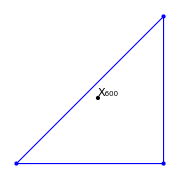

```mathematica
Module[{tri,sides,x},
tri={{0,0},{1,0},{1,1}};
sides=triLengthsRL@tri;
x=getX600Trilin[tri,sides];
Print@x;
Graphics[{FaceForm@None,PointSize@Medium,drawPoly[tri,Blue],Point@x,Text["X_600",x,{-1,-1}]},ImageSize->Small]]
```

```mathematica
(* X(1145) bc(b+c-2a)[2abc-(b+c)(a2-(b-c)2)] *)
getX1145Trilin[orbit_,{a_,b_,c_}]:=Module[{abc=a b c},
trilinearToCartesian[orbit,{a,b,c},
{b c(b+c-2a)(2abc-(b+c)(a^2-(b-c)^2)),
c a(c+a-2b)(2abc-(c+a)(b^2-(c-a)^2)),
a b(a+b-2c)(2abc-(a+b)(c^2-(a-b)^2))}
]]
```

```mathematica
(* de Longchamps Point *)
getX20Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
trilinearToCartesian[orbit,{a,b,c},{
cosA-cosB cosC,
cosB-cosC cosA,
cosC-cosA cosB}]];
```

```mathematica
(* 1/(cos B+cos C) *)
getX21Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
trilinearToCartesian[orbit,{a,b,c},1/{cosB+cosC,cosC+cosA,cosA+cosB}]];
```

```mathematica
(*cos3A,cos3B,cos3C*)
Clear@getX49Trilin;getX49Trilin[orbit_,{a_,b_,c_}]:=Module[{coss,cos3s},
coss=lawOfCosines3[a,b,c];
cos3s=cosTripleAngle/@coss;
trilinearToCartesian[orbit,{a,b,c},cos3s]];
```

```mathematica
Clear@getX59Trilin;getX59Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinA,sinB,sinC,cosBC,cosCA,cosAB},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
cosBC=cosB*cosC+sinB*sinC;
cosCA=cosC*cosA+sinC*sinA;
cosAB=cosA*cosB+sinA*sinB;
trilinearToCartesian[orbit,{a,b,c},{
1/(1-cosBC),
1/(1-cosCA),
1/(1-cosAB)}]];
```

```mathematica
Clear@getX144Trilin;getX144Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinA,sinB,sinC,tanAov2,tanBov2,tanCov2},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
tanAov2=tanHalfAngle[sinA,cosA];
tanBov2=tanHalfAngle[sinB,cosB];tanCov2=tanHalfAngle[sinC,cosC];
(* (csc A)(tan B/2+tan C/2-tan A/2) *)
trilinearToCartesian[orbit,{a,b,c},{
(tanBov2+tanCov2-tanAov2)/sinA,
(tanCov2+tanAov2-tanBov2)/sinB,
(tanAov2+tanBov2-tanCov2)/sinC}]];

(* intersection of feuerbach hyp w/ billiard *)
Clear@getX1156Trilin;
getX1156Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{
(b-c)^2 + a(b+c-2a),
(c-a)^2 + b(c+a-2b),
(a-b)^2 + c(a+b-2c)
}];
```

```mathematica
Clear@getX1155Trilin;
getX1155Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{
(b-c)^2 + a(b+c-2a),
(c-a)^2 + b(c+a-2b),
(a-b)^2 + c(a+b-2c)
}];
```

```mathematica
(* a(b^2 Cos[2B]+ c^2 Cos[2C] - a^2 Cos[2A]) *)
getX26Trilin[orbit_,{a_,b_,c_}]:=
Module[{cosA,cosB,cosC,cos2A,cos2B,cos2C,a2=a*a,b2=b*b,c2=c*c},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
cos2A=2 cosA^2-1;
cos2B=2 cosB^2-1;
cos2C=2 cosC^2-1;
trilinearToCartesian[orbit,{a,b,c},
{a(b2 cos2B+ c2 cos2C - a2 cos2A),
b(c2 cos2C+ a2 cos2A - b2 cos2B),
c(a2 cos2A+ b2 cos2B - c2 cos2C)}
]];
```

```mathematica
getX359[orbit_,{a_,b_,c_}]:=
Module[{cosA,cosB,cosC,A,B,C},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
A=ArcCos[cosA];
B=ArcCos[cosB];
C=ArcCos[cosC];
trilinearToCartesian[orbit,{a,b,c},
{a/A,b/B,c/C}
]];
```

```mathematica
getX360[orbit_,{a_,b_,c_}]:=
Module[{cosA,cosB,cosC,A,B,C},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
A=ArcCos[cosA];
B=ArcCos[cosB];
C=ArcCos[cosC];
trilinearToCartesian[orbit,{a,b,c},
{A/a,B/b,C/c}
]];
```

```mathematica
getX364[orbit_,{a_,b_,c_}]:=Module[{ah=Sqrt@a,bh=Sqrt@b,ch=Sqrt@c},
trilinearToCartesian[orbit,{a,b,c},
{bh+ch-ah,ch+ah-bh,ah+bh-ch}
]];
```

```mathematica
getX365[orbit_,{a_,b_,c_}]:=
trilinearToCartesian[orbit,{a,b,c},
{Sqrt@a,Sqrt@b,Sqrt@c}
];
```

```mathematica
getX366[orbit_,{a_,b_,c_}]:=
trilinearToCartesian[orbit,{a,b,c},
1/{Sqrt@a,Sqrt@b,Sqrt@c}
];
```

```mathematica
getX367[orbit_,{a_,b_,c_}]:=Module[{ah=Sqrt@a,bh=Sqrt@b,ch=Sqrt@c},
trilinearToCartesian[orbit,{a,b,c},
1/{bh+ch,ch+ah,ah+bh}
]];
```

```mathematica
Module[{ons},
ons=orbitNormals[1.5,toRad@10.];
getX360[ons[[1]],ons[[3]]]]
```

{-0.266377,-0.414822}

```mathematica
(* incenter of excentral triangle *)
getX164Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinAov2,sinBov2,sinCov2},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinAov2,sinBov2,sinCov2}=sinHalfAngle/@{cosA,cosB,cosC};
trilinearToCartesian[orbit,{a,b,c},{
sinBov2+sinCov2-sinAov2,
sinCov2+sinAov2-sinBov2,
sinAov2+sinBov2-sinCov2
}]];
```

```mathematica
(* barycenter of excentral triangle *)
getX165Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a a,b2=b b,c2=c c},
trilinearToCartesian[orbit,{a,b,c},{
3a2-2a(b+c)-(b-c)^2,
3b2-2b(c+a)-(c-a)^2,
3c2-2c(a+b)-(a-b)^2
}]];
```

```mathematica
(* mittenpunkt of excentral triangle *)
getX168Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinAov2,sinBov2,sinCov2},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinAov2,sinBov2,sinCov2}=sinHalfAngle/@{cosA,cosB,cosC};
trilinearToCartesian[orbit,{a,b,c},{
b/(1-sinBov2)+c/(1-sinCov2)-a/(1-sinAov2),
c/(1-sinCov2)+a/(1-sinAov2)-b/(1-sinBov2),
a/(1-sinAov2)+b/(1-sinBov2)-c/(1-sinCov2)}]];
```

```mathematica
Module[{o,n,s},
{o,n,s}=orbitNormals[1.5,1.1];
getOrthocenterTrilin[o,s]]
```

{0.696532,1.04352}

```mathematica
Module[{o,n,s,cirs,incs},
{o,n,s}=orbitNormals[1.5,1.1];
cirs={getCircumcenterTrilin[o,s],getCircumcenter@@o};
incs={getIncenterTrilin[o,s],getIncenter[o[[1]],n[[1]],o[[2]],n[[2]]]};
{cirs,incs}//MatrixForm]
```

({-0.0701496,-0.336575} | getCircumcenter[{0.680394,0.891207},{1.3669,-0.41182},{-1.49106,-0.109019}]
{0.449317,0.210191} | getIncenter[{0.680394,0.891207},{-0.321319,-0.946971},{1.3669,-0.41182},{-0.827741,0.561111}])

#### Generate Billiard as Locus

```mathematica
(* isog conj of X9 *)
getX57Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b+c-a,c+a-b,a+b-c}];
```

```mathematica
getX100Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b-c,c-a,a-b}];
getX513Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b-c,c-a,a-b}];
getX649Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{a(b-c),b(c-a),c(a-b)}];
getX101Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{safeDiv[a,b-c],safeDiv[b,c-a],safeDiv[c,a-b]}];
(* vtx of Yff parabola *)
getX3234Trilin[orbit_,{a_,b_,c_}]:=Module[{a2,b2,c2,a3,b3,c3,trils},
a2=a*a;b2=b*b;c2=c*c;
a3=a2*a;b3=b2*b;c3=c2*c;
trils={
((a-b) (a-c) (2a3-a2 b-b3-a2 c+b2 c+b c2-c3)^2)/a,
((b-c) (b-a) (2b3-b2 c-c3-b2 a+c2 a+c a2-a3)^2)/b,
((c-a) (c-b) (2c3-c2 a-a3-c2 b+a2 b+a b2-b3)^2)/c};
trilinearToCartesian[orbit,{a,b,c},trils]
];


getX88Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b+c-2a,c+a-2b,a+b-2c}];
getX162Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},Module[{a2=a*a,b2=b*b,c2=c*c},
1/{(b2-c2)(b2+c2-a2),(c2-a2)(c2+a2-b2),(a2-b2)(a2+b2-c2)}]];
(* isogonal conjugate of X88, therefore all are inverted *)
getX36Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a a,b2=b b,c2=c c},
trilinearToCartesian[orbit,{a,b,c},{
a(b2+c2-a2-b c),
b(c2+a2-b2-c a),
c(a2+b2-c2-a b)}]
];
getX44Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b+c-2a,c+a-2b,a+b-2c}];
getX693Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{(b-c)/a^2,(c-a)/b^2,(a-b)/c^2}];
```

```mathematica
(* X(230) bc[a2(2a2-b2-c2)+(b2-c2)2] *)
getX230Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a a,b2=b b,c2=c c},
trilinearToCartesian[orbit,{a,b,c},{
b c(a2(2a2-b2-c2)+(b2-c2)^2),
c a(b2(2b2-c2-a2)+(c2-a2)^2),
a b(c2(2c2-a2-b2)+(a2-b2)^2)
}]];
```

```mathematica
(* YFF PARABOLIC POINT *)
getX190Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c/(b-c),c a/(c-a),a b/(a-b)}];
(* X650 is both on the anti-orthic axis and on L55 Gergonne of ACT, i.e., L(31) of billiard, meaning *both* its isotomic and isogonal conjugates lie on the EB, i.e., the E9-centered circumellipse *)
(* X(650)=isogonal conjugate of X(651)
X(650)=isotomic conjugate of X(4554)
*) 
getX650Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
{(b-c)(b+c-a),
(c-a)(c+a-b),
(a-b)(a+b-c)}];
(*bc/[a(b-c)(b+c-a)] = 1/[a^2(b-c)(b+c-a)] *)
getX4554Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
1/{a^2(b-c)(b+c-a),b^2(c-a)(c+a-b),c^2(a-b)(a+b-c)}];
getX652Trilin[orbit_,{a_,b_,c_}]:=Module[{secA,secB,secC},
{secA,secB,secC}=1/lawOfCosines3[a,b,c];trilinearToCartesian[orbit,{a,b,c},{secB-secC,secC-secA,secA-secB}]];
getX655Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinA,sinB,sinC,cosAmB,cosBmC,cosCmA},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=Sqrt[1-#^2]&/@{cosA,cosB,cosC};
(* f(A,B,C):f(B,C,A):f(C,A,B),where f(A,B,C)=1/[cos(A-B)-cos(C-A)] *)
cosAmB=cosA cosB+sinA sinB;
cosBmC=cosB cosC+sinB sinC;
cosCmA=cosC cosA+sinC sinA;
trilinearToCartesian[orbit,{a,b,c},
1/{cosAmB-cosCmA,cosBmC-cosAmB,cosCmA-cosBmC}]
];
getX656Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},{(b2-c2)(b2+c2-a2),(c2-a2)(c2+a2-b2),(a2-b2)(a2+b2-c2)}]];
getX798Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},{a2(b2-c2),b2(c2-a2),c2(a2-b2)}]];
getX823Trilin[orbit_,{a_,b_,c_}]:=Module[{secA2,secB2,secC2},
{secA2,secB2,secC2}=1/{lawOfCosines[a,b,c]^2,lawOfCosines[b,a,c]^2,lawOfCosines[c,a,b]^2};
trilinearToCartesian[orbit,{a,b,c},1/{
secB2-secC2,
secC2-secA2,
secA2-secB2}]];
(* TRILINEAR POLE OF LINE X(1)X(3) *)
getX651Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{(b-c)(b+c-a),(c-a)(c+a-b),(a-b)(a+b-c)}];
```

```mathematica
(* sec(A-π/6)=1/[cosA cosPi6+ sinA sinPi6] *)
getX13Trilin[orbit_,{a_,b_,c_}]:=Module[{coss,cosPi6=Cos[π/6],sinPi6=Sin[π/6],sins,cosABCmPi6},
coss=lawOfCosines3[a,b,c];
cosABCmPi6=cosDiffAngle[#,Sqrt[1-#^2],cosPi6,sinPi6]&/@coss;
trilinearToCartesian[orbit,{a,b,c},1/cosABCmPi6]];
```

```mathematica
(* (b-c)/a *) getX514Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
{(b-c)/a,(c-a)/b,(a-b)/c}
];
```

```mathematica
(* Peter Moses: Perspector of the Inner Conway Triangle, vertices on the EB *)
(* (a^2+(b-c)^2)(a^3-(b+c)*a^2+(b+c)^2*a-(b+c)(b^2+c^2)): *)
fnX11677[a_,b_,c_]:=Module[{a2=a a,b2=b b,c2=c c},(a2 + (b - c)^2) (a a2 - (b + c)a2 + a(b + c)^2 - (b + c) (b2 + c2))/a] ;
getX11677[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},{fnX11677[a,b,c],fnX11677[b,c,a],fnX11677[c,a,b]}]];
```

#### Novo resultado : X661 é o unico ponto no plano q esta simultaneamente no eixo antiortico e no [L(55) do anticomplementar] L(31) do de referencia. É o unico ponto no plano tal que seus conjugados isogonal e o isotomico caem (em pontos diferentes: 662 e 799) no bilhar.

```mathematica
(* b^2-c^2 *) 
getX661Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},{b2-c2,c2-a2,a2-b2}]];
(* X(661)=isogonal conjugate of X(662)
X(661)=isotomic conjugate of X(799) *)
(* x662 is isog conj of x661 *)
getX662Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},1/{b2-c2,c2-a2,a2-b2}]];
(* x799 is isot conj of x661 *)
getX663Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},{a(b-c)(b+c-a),b(c-a)(c+a-b),c(a-b)(a+b-c)}]];
getX664Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},1/{a(b-c)(b+c-a),b(c-a)(c+a-b),c(a-b)(a+b-c)}]];
getX664TestTrilin[orbit_,{a_,b_,c_}]:=
trilinearToCartesian[orbit,{a,b,c},
{(a-b) (a-c) (a+b-c) (a+c-b)/a,
(b-c) (b-a) (b+c-a) (b+a-c)/b,
(c-a) (c-b) (c+a-b) (c+b-a)/c}];
getX799Trilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},1/{a2(b2-c2),b2(c2-a2),c2(a2-b2)}]];
```

```mathematica
(* X(908)= POINT ACUBENS = (cosB+cosC-1)/a *)
getX908Trilin[orbit_,{a_,b_,c_}]:=Module[{cA,cB,cC},
{cA,cB,cC}=lawOfCosines3[a,b,c];
trilinearToCartesian[orbit,{a,b,c},
{(cB+cC-1)/a,
(cC+cA-1)/b,
(cA+cB-1)/c}
]];
```

```mathematica
(* X(857)= INTERCEPT OF EULER LINE AND TRILINEAR POLAR OF X(75)
X(857)= sinC^2 sin2B sin(C-A) + sinB^2 sin2C sin(B-A) *)
getX857Trilin[orbit_,{a_,b_,c_}]:=Module[{cA,cB,cC,sA2,sB2,sC2,sA,sB,sC,sAmC,sAmB,sBmC,s2A,s2B,s2C},
{cA,cB,cC}=lawOfCosines3[a,b,c];
{sA2,sB2,sC2}=(1-#^2)&/@{cA,cB,cC};
{sA,sB,sC}=Sqrt/@{sA2,sB2,sC2};
{s2A,s2B,s2C}=MapThread[sinDoubleAngle,{{sA,sB,sC},{cA,cB,cC}}];
sAmB=sA cB-cA sB;
sAmC=sA cC-cA sC;
sBmC=sB cC-cB sC;
trilinearToCartesian[orbit,{a,b,c},{
-sC2 s2B sAmC-sB2 s2C sAmB,
sA2 s2C sAmB-sC2 s2A sBmC,
sB2 s2A sBmC+sA2 s2B sAmC}]];
```

```mathematica
(* X(2590)=X(2)-ISOCONJUGATE OF X(1381) *)
(* a/f(a,b,c):b/f(b,c,a):c/f(c,a,b),where f(a,b,c) is as at X(1381) *)
(* X(1381)=1st INTERCEPT OF LINE X(1)X(3) AND CIRCUMCIRCLE
Trilinears f(a,b,c):f(b,c,a):f(c,a,b),where f(a,b,c)=r+(|OI|-R) cos A *)
getX2590Trilin[orbit_,{a_,b_,c_}]:=Module[{cA,cB,cC,r,x3,x1,R,k},
{cA,cB,cC}=lawOfCosines3[a,b,c];
x1=getIncenterTrilin[orbit,{a,b,c}];
x3=getCircumcenterTrilin[orbit,{a,b,c}];
r=getInradius[{a,b,c}];
R=getCircumradius[{a,b,c}];
k=magn[x1-x3]-R;
trilinearToCartesian[orbit,{a,b,c},{
a/(r+k cA),b/(r+k cB),c/(r+k cC)
}]
];
```

```mathematica
getX2590Trilin@@Part[orbitNormals[1.2,toRad@0.],{1,3}]
```

{-6.21306,9.50995×10^-15}

```mathematica
getX101Trilin@@Part[orbitNormals[2,toRad@40.],{1,3}]
```

{-1.41096,1.00183}

```mathematica
getX4554Trilin@@Part[orbitNormals[2,toRad@40.],{1,3}]
```

{-1.70288,0.167823}

```mathematica
Chop[getMittenTrilin@@Part[orbitNormals[2,toRad@10.],{1,3}]]
```

{0,0}

#### Barycentrics (does not appear to work!)

-Graphics-

```mathematica
barycentricToCartesian[orbit_,lambdas0_]:=Module[{x,y,area,lambdas},
(*area=Area[Polygon@orbit];*)
lambdas=lambdas0/Total@lambdas0;
x=Total@MapThread[(#1*#2)&,{First/@orbit,lambdas}];
y=Total@MapThread[(#1*#2)&,{Second/@orbit,lambdas}];
{x,y}];
```

```mathematica
Clear@X10405;X10405[orbit_,{a_,b_,c_}]:=barycentricToCartesian[orbit,
1/{3a^2-2a b-2a c-(b-c)^2,
3b^2-2b c-2b a-(c-a)^2,
3c^2-2c a-2c b-(a-b)^2}];
```

```mathematica
(* perpector of anticomplementary on extouch: http://mathworld.wolfram.com/Perspector.html  *)
```

```mathematica
X144b[orbit_,{a_,b_,c_}]:=barycentricToCartesian[orbit,
{1/(a-b-c)+1/(a-b+c)+1/(a+b-c),
1/(b-c-a)+1/(b-c+a)+1/(b+c-a),
1/(c-a-b)+1/(c-a+b)+1/(c+a-b)}];
```

```mathematica
Module[{o,n,s},
{o,n,s}=orbitNormals[1.5,.1];
{getX144Trilin[o,s],X144b[o,s]}
]
```

{{0.59009,0.346298},{0.59009,0.346298}}

```mathematica
equiError[tri_]:=Module[{s,bar,inc,savg},
s=triLengthsRL@tri;
savg=Total@s/Length@s;
bar=getBarycenterTrilin[tri,s];
inc=getIncenterTrilin[tri,s];
magn2[bar-inc]/savg]
```

```mathematica
isEqui[tri_]:=equiError[tri]<10^-6;
```

```mathematica
drawPoly[poly_,clr_]:={EdgeForm@{clr,Thick},Polygon@poly,clr,Point@poly};
drawPolyThick[poly_,clr_]:={EdgeForm@{clr,AbsoluteThickness@3},Polygon@poly,clr,Point@poly};
```

## Triangles form Trilinear Matrices

```mathematica
trilinearMatrixToCartesian[orbit_,sides_,tryM_]:=trilinearToCartesian[orbit,sides,#]&/@tryM;
trilinearMatrixToCartesianUnsafe[orbit_,sides_,tryM_]:=trilinearToCartesianUnsafe[orbit,sides,#]&/@tryM;
```

to do : anticomplementary, external tangents triangle.

```mathematica
intouchTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,(a c)/(a-b+c),(a b)/(a+b-c)},
{(b c)/(-a+b+c),0,(a b)/(a+b-c)},
{(b c)/(-a+b+c),(a c)/(a-b+c),0}}];
```

```mathematica
intouchTriangleUnsafe[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesianUnsafe[orbit,{a,b,c},
{{0,(a c)/(a-b+c),(a b)/(a+b-c)},
{(b c)/(-a+b+c),0,(a b)/(a+b-c)},
{(b c)/(-a+b+c),(a c)/(a-b+c),0}}];
```

```mathematica
extouchTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,(a-b+c)/b,(a+b-c)/c},
{(-a+b+c)/a,0,(a+b-c)/c},
{(-a+b+c)/a,(a-b+c)/b,0}}];
```

```mathematica
Clear@incentralTriangle;
incentralTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,1,1},
{1,0,1},
{1,1,0}}];
```

```mathematica
Clear@excentralTriangle;
excentralTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{-1,1,1},
{1,-1,1},
{1,1,-1}}];
```

```mathematica
Clear@medialTriangle;
medialTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,a c,a b},{b c,0,a b},{b c,a c,0}}];
```

```mathematica
Clear@yffTriangle;
yffTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,safeDiv[a c,c-a],safeDiv[a b,a-b]},(* error in mathworld http://mathworld.wolfram.com/YffContactTriangle.html which shows this as {0,ac/(c-a),ab/(b-a)}*)
{safeDiv[b c,b-c],0,safeDiv[a b,a-b]},
{safeDiv[b c,b-c],safeDiv[a c,c-a],0}}];
```

```mathematica
Module[{tri={{0,0},{1,0},{1,1}}},
medialTriangle[tri,triLengthsRL@tri]]
```

{{1,1/2},{1/2,1/2},{1/2,0}}

```mathematica
Clear@orthicTriangle;
orthicTriangle[orbit_,sides_]:=Module[{secA,secB,secC},
{secA,secB,secC}=1./getTriCosines[orbit];trilinearMatrixToCartesian[orbit,sides,{{0,secB,secC},{secA,0,secC},{secA,secB,0}}]];
```

```mathematica
Clear@eulerTriangle;
eulerTriangle[orbit_,{a_,b_,c_}]:=Module[{cA,cB,cC,sA,sB,sC,tA,tB,tC},
{cA,cB,cC}={
lawOfCosines[a,b,c],
lawOfCosines[b,a,c],
lawOfCosines[c,a,b]};
{sA,sB,sC}=getSin/@{cA,cB,cC};
{tA,tB,tC}={sA/cA,sB/cB,sC/cC};
trilinearMatrixToCartesian[orbit,{a,b,c},
{{2 tA+tB+tC,sA/cB,sA/cC},
{sB/cA,tA+2tB+tC,sB/cC},
{sC/cA,sC/cB,tA+tB+2tC}}]];
```

```mathematica
(* https://faculty.evansville.edu/ck6/encyclopedia/gemini.html *)
(* (a^2+b*c)/a:(-a*b-c*a)/b:(-a*b-c*a)/c *)
(* remember to rotate rows *)
gemini90Triangle[orbit_,{a_,b_,c_}]:=Module[{a2=a a,b2=b b,c2=c c},
trilinearMatrixToCartesian[orbit,{a,b,c},
{{(a2+b c)/a , (-a b-c a)/b , (-a b-c a)/c},
{ (-b c-a b)/a,(b2+c a)/b , (-b c-a b)/c },
{ (-c a-b c)/a,(-c a-b c)/b,(c2+a b)/c }}]];
```

```mathematica
gemini2Triangle[orbit_,{a_,b_,c_}]:=
trilinearMatrixToCartesian[orbit,{a,b,c},
{{-1,(b+c)/b,(b+c)/c},
{(c+a)/a,-1,(c+a)/c},
{(a+b)/a,(a+b)/b,-1}}];
```

```mathematica
gemini30Triangle[orbit_,{a_,b_,c_}]:=
trilinearMatrixToCartesian[orbit,{a,b,c},
{{1,(c-b)/b,(b-c)/c},
{(c-a)/a,1,(a-c)/c},
{(b-a)/a,(a-b)/b,1}}];
```

```mathematica
honsbergerVtxA[a_,b_,c_]:={(a-b+c)(a+b-c),(a+b-c)((b-c)^2-a(b+c))/b,(a-b+c)((b-c)^2-a(b+c))/c};
```

```mathematica
honsbergerTriangle[orbit_,{a_,b_,c_}]:=
trilinearMatrixToCartesian[orbit,{a,b,c},
{honsbergerVtxA[a,b,c],RotateRight[honsbergerVtxA[b,c,a],1],RotateRight[honsbergerVtxA[c,a,b],2]}];
```

```mathematica
(* intouch of ACT on the EB *)
innerConwayTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{b c,(c-b)c,(b-c)b},
{(c-a)c,c a,(a-c)a},
{(b-a)b,(a-b)a,a b}}];
```

```mathematica
(* http://mathworld.wolfram.com/TangentialTriangle.html *)
tangentialTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{-a,b,c},{a,-b,c},{a,b,-c}}];
anticomplementaryTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{1/{-a,b,c},1/{a,-b,c},1/{a,b,-c}}];
externaltangentsTriangle[orbit_,sides_]:=Module[{x,y,z},
{x,y,z}=getTriCosines[orbit];
trilinearMatrixToCartesian[orbit,sides,
{{-(x+1),x+z,x+y},
{y+z,-(y+1),y+x},
{z+y,z+x,-(z+1)}
}]];
```

```mathematica
hexylTriangle[orbit_,{a_,b_,c_}]:=Module[{x,y,z,diag},
{x,y,z}=lawOfCosines3[a,b,c];
diag=x+y+z+1;
trilinearMatrixToCartesian[orbit,{a,b,c},
{{diag,x+y-z-1,x-y+z-1},
{x+y-z-1,diag,-x+y+z-1},
{x-y+z-1,-x+y+z-1,diag}}]];
```

```mathematica
outerNapoleonTriangle[orbit_,{a_,b_,c_}]:=Module[{
cosA,cosB,cosC,sinA,sinB,sinC,
cPi6,sPi6,
sApPi6,sBpPi6,sCpPi6,sAmPi6,sBmPi6,sCmPi6},
cPi6=Cos[π/6.];
sPi6=Sin[π/6.];
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{sApPi6,sAmPi6}=getSinApmB[sinA,sPi6,cosA,cPi6];
{sBpPi6,sBmPi6}=getSinApmB[sinB,sPi6,cosB,cPi6];
{sCpPi6,sCmPi6}=getSinApmB[sinC,sPi6,cosC,cPi6];
trilinearMatrixToCartesian[orbit,{a,b,c},
{{-1,2sCpPi6,2sBpPi6},
{2sCpPi6,-1,2sApPi6},
{2sBpPi6,2sApPi6,-1}}]];
```

```mathematica
firstMorleyTriangle[orbit_,{a_,b_,c_}]:=Module[{cs,cs3},
cs=lawOfCosines3[a,b,c];
cs3=cosThird/@cs;
trilinearMatrixToCartesian[orbit,{a,b,c},
{{1,2cs3[[3]],2cs3[[2]]},
{2cs3[[3]],1,2cs3[[1]]},
{2cs3[[2]],2cs3[[1]],1}}]];
```

-Graphics-

```mathematica
secondMorleyTriangle[orbit_,{a_,b_,c_}]:=Module[{cs,cs3,ss3,s2p3,c2p3,a12,a13,a23},
cs=lawOfCosines3[a,b,c];
cs3=cosThird/@cs;
ss3=Sqrt[1-#^2]&/@cs3;
c2p3=-1/2;(*Cos[2π/3.];*)
s2p3=Sqrt[3]/2;(*Sin[2π/3.];*)
a12=cs3[[3]] c2p3+ss3[[3]] s2p3;
a13=cs3[[2]] c2p3+ss3[[2]] s2p3;
a23=cs3[[1]] c2p3+ss3[[1]] s2p3;
trilinearMatrixToCartesian[orbit,{a,b,c},
{{1,2a12,2a13},
{2a12,1,2a23},
{2a13,2a23,1}}]];
```

-Graphics-

```mathematica
Sin[4π/3]
```

-(√3)/2

```mathematica
thirdMorleyTriangle[orbit_,{a_,b_,c_}]:=Module[{cs,cs3,ss3,s4p3,c4p3,a12,a13,a23},
cs=lawOfCosines3[a,b,c];
cs3=cosThird/@cs;
ss3=Sqrt[1-#^2]&/@cs3;
c4p3=-1/2;(*Cos[4π/3.];*)
s4p3=-Sqrt[3]/2;(*Sin[4π/3.];*)
a12=cs3[[3]] c4p3+ss3[[3]] s4p3;
a13=cs3[[2]] c4p3+ss3[[2]] s4p3;
a23=cs3[[1]] c4p3+ss3[[1]] s4p3;
trilinearMatrixToCartesian[orbit,{a,b,c},
{{1,2a12,2a13},
{2a12,1,2a23},
{2a13,2a23,1}}]];
```

```mathematica
cevianTriangle[orbit_,{a_,b_,c_},{t1_,t2_,t3_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{0,t2,t3},{t1,0,t3},{t1,t2,0}}];antiCevianTriangle[orbit_,{a_,b_,c_},{t1_,t2_,t3_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{-t1,t2,t3},{t1,-t2,t3},{t1,t2,-t3}}];
```

```mathematica
pedalTriangle[orbit_,{a_,b_,c_},{t1_,t2_,t3_}]:=Module[{cA,cB,cC},
{cA,cB,cC}=lawOfCosines3[a,b,c];
trilinearMatrixToCartesian[orbit,{a,b,c},{
{0,t2+t1 cC,t3+t1 cB},
{t1+t2 cC,0,t3+t2 cA},
{t1+t3 cB,t2+t3 cA,0}
}]];
```

-Graphics-

```mathematica
antipedalTriangle[orbit_,{a_,b_,c_},{α_,β_,γ_}]:=Module[{cA,cB,cC},
{cA,cB,cC}=lawOfCosines3[a,b,c];
trilinearMatrixToCartesian[orbit,{a,b,c},{
{-(β+α cC)(γ+α cB),(γ+α cB)(α+β cC),(β+α cC)(α+γ cB)},
{(γ+β cA)(β+α cC),-(γ+β cA)(α+β cC),(α+β cC)(β+γ cA)},
{(β+γ cA)(γ+α cB),(α+γ cB)(γ+β cA),-(α+γ cB)(β+γ cA)}
}]];
```

```mathematica
trilinearCoords[tri_,p_]:=
RotateLeft@MapThread[magn[closestPerp[p,#1,#2]-p]&,
(* needs this crossed rotation so trilinears come out in the usual way *)
{tri,RotateLeft@tri}]
```

```mathematica
Module[{o,n,s,p,tril},
{o,n,s}=orbitNormals[1.5,toRad@35.];
p=getSymmedianTrilin[o,s];
tril=trilinearCoords[o,p];
tril
(*Print@(s/s[[1]]);
tril/tril[[1]]*)]
```

{0.551909,0.580316,0.273465}

```mathematica
symmedialTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{0,b,c},{a,0,c},{a,b,0}}];
```

```mathematica
Clear@feuerbachTriangle;
feuerbachTriangle[orbit_,{a_,b_,c_}]:=Module[{
sinA,sinB,sinC,
cosA,cosB,cosC,
cosBmC,cosCmA,cosAmB,
c2haAmB,c2haBmC,c2haCmA,
m},
{cosA,cosB,cosC}=lawOfCosines3[a,b,c];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
cosBmC=cosDiffAngle[sinB,cosB,sinC,cosC];
cosCmA=cosDiffAngle[sinC,cosC,sinA,cosA];
cosAmB=cosDiffAngle[sinA,cosA,sinB,cosB];
c2haAmB=cos2HalfAngle[cosAmB];
c2haBmC=cos2HalfAngle[cosBmC];
c2haCmA=cos2HalfAngle[cosCmA];
m={
{-sin2HalfAngle[cosBmC],c2haCmA,c2haAmB},
{c2haBmC,-sin2HalfAngle[cosCmA],c2haAmB},
{c2haBmC,c2haCmA,-sin2HalfAngle[cosAmB]}
};trilinearMatrixToCartesian[orbit,{a,b,c},m]];
```

```mathematica
Module[{o,n,s},
{o,n,s}=orbitNormals[1.5,.1];
feuerbachTriangle[o,s]]
```

{{-1.04832,-0.369712},{-0.112968,0.352287},{0.256211,-0.740368}}

#### The first point in the extouch triangle flows on caustic at the exact same parametric than P1

```mathematica
Manipulate[Module[{o,ett,ell,a=1.5,gr,ca,cb},
o=orbitNormals[a,t][[1]];
{ca,cb}=getTriCausticParams[a];
ett=extouchTriangle[o,triLengthsRL@o];
gr=Graphics[{FaceForm@None,PointSize@Medium,
{EdgeForm@{Blue,Thick},Polygon@o,Red,Point@First@o,Blue,Circle[First@o,.05]},
{EdgeForm@Darker@Green,Polygon@ett},
{Darker@Green,Circle[ett[[1]],.05]},
{Red,Point[{-ca Cos[t],-cb Sin[t]}]}}];
Show[{plotEll[a],plotEllb[ca,cb,Brown],gr},AspectRatio->Automatic,Frame->True]],{t,0,2π,π/360.}]
```

#### Anticomplementary triangle seems like the more stable, more useful to produce higher order points.

```mathematica
DynamicModule[{cc,vs,sides,cir,cirRad,tt,ac,et,ortTril,ortCev,clrs,ort,ortAntiCev,hexyl},
Manipulate[
vs={{-1,0},{1,0},p1}; (*N@{{0,0},{1,-.6},{.7,.5}};*)
sides=triLengthsRL@vs;
cir=getCircumcenterTrilin[vs,sides];
cirRad=magn[vs[[1]]-cir];
tt=tangentialTriangle[vs,sides];
ac=anticomplementaryTriangle[vs,sides];
et=externaltangentsTriangle[vs,sides];
hexyl=hexylTriangle[vs,sides];
ortTril=1/getTriCosines[vs];
ort=trilinearToCartesian[vs,sides,ortTril];
ortCev=cevianTriangle[vs,sides,ortTril];
ortAntiCev=antiCevianTriangle[vs,sides,ortTril];
clrs={Black,Red,Green,Blue,Purple,Cyan,Pink};
Legended[Graphics[{PointSize@Medium,Black,FaceForm@None,
MapThread[{EdgeForm@#1,#1,Polygon@#2,Point@#2}&,{clrs,{vs,tt,ac,et,ortCev,ortAntiCev,hexyl}}],
{Circle[cir,cirRad],Point@cir},
{Orange,Point@ort}},ImageSize->Medium,Frame->True,PlotRange->{{-5,5},{-5,5}}],
LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
{"reference","tangential","anticomplementary","external tangents","ortho cevian = orthic","ortho anticevian","hexyl"}]],
{{p1,{0,2}},Locator},SaveDefinitions->True]]
```

```mathematica
DynamicModule[{cc,vs,normals,sides,ell,cir,cirRad,tt,ac,et,ortTril,ortCev,clrs,ort,ortAntiCev,hexyl,gr,xmax=3,ymax=3},Manipulate[
ell=plotEll[a];
{vs,normals,sides}=orbitNormals[a,toRad@tDeg];
sides=triLengthsRL@vs;
cir=getCircumcenterTrilin[vs,sides];
cirRad=magn[vs[[1]]-cir];
tt=tangentialTriangle[vs,sides];
ac=anticomplementaryTriangle[vs,sides];
et=externaltangentsTriangle[vs,sides];
hexyl=hexylTriangle[vs,sides];
ortTril=1/getTriCosines[vs];
ort=trilinearToCartesian[vs,sides,ortTril];
ortCev=cevianTriangle[vs,sides,ortTril];
ortAntiCev=antiCevianTriangle[vs,sides,ortTril];
clrs={Black,Red,Green,Blue,Purple,Cyan,Pink};
gr=Legended[Graphics[{PointSize@Medium,Black,FaceForm@None,
MapThread[{EdgeForm@#1,#1,Polygon@#2,Point@#2}&,{clrs,{vs,tt,ac,et,ortCev,ortAntiCev,hexyl}}],
{Circle[cir,cirRad],Point@cir},
{Orange,Point@ort}},ImageSize->Medium,Frame->True,PlotRange->{{-5,5},{-5,5}}],
LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
{"reference","tangential","anticomplementary","external tangents","ortho cevian = orthic","ortho anticevian","hexyl"}]];
Show[{ell,gr},PlotRange->{{-xmax,xmax},{-ymax,ymax}}],
{{a,1.5},1.01,3,.05},
{{tDeg,0},-360,360,.1},SaveDefinitions->True]]
```

## Triangular Orbits

#### Ellipse Invariants

#### Constant Perimeter (Gaston Darboux, 1917)

#### -Graphics- Jean-Gaston Darboux (1842-1917)

```mathematica
deltaA[a_]:=Sqrt[a^4-a^2 +1];
```

```mathematica
Clear[darbouxP];
darbouxP[a_,b_:1]:=Module[{a2,b2,delta,per},
a2=a^2;
b2=b^2;
delta=Sqrt[a2^2-a2 b2+b2^2];
per=2Sqrt[2delta-a2-b2](a2+b2+delta)/(a2-b2);
per
];
```

#### Exit angle at x_1 which creates triangular orbit (Garcia, 2019)

-Graphics-

```mathematica
Clear@cosAlpha;cosAlpha[a_,x_]:=Module[{x2,a2,a4,c2,denom},
x2=x^2;
a2=a^2;
a4=a2^2;
c2=a2-1;
denom=c2 Sqrt[a4-c2 x2];
a2 Sqrt[-a2-1+2Sqrt[a4-c2]]/denom];
```

```mathematica
cosAlpha[a,x]//TeXForm
```

\frac{a^2 \sqrt{-a^2+2 \sqrt{a^4-a^2+1}-1}}{\left(a^2-1\right) \sqrt{a^4-\left(a^2-1\right) x^2}}

#### Can I find an expression for the next orbit point P_2 in terms of “a” and x_1

```mathematica
Clear@getP2;getP2[a_,x1_]:=Module[{y,p1,norm,ca,sa,p2,normRot,normRotNeg,p2Neg},
y=-ellY[a,x1];
p1={x1,y};
ca=cosAlpha[a,x1]/.{Sqrt[1-a^2+a^4]->d}/.{-1-a^2+2 d->d2};(* to simplify *)
sa=Sqrt[1-ca^2];
norm=ellGrad[a,x1,y];
normRot=rot[norm,sa,ca];
normRotNeg=rot[norm,-sa,ca];
p2=ellInterRayUnprot[a,p1,normRot][[2]]; (* get 2nd solution *)
p2Neg=ellInterRayUnprot[a,p1,normRotNeg][[2]]; 
{p2,p2Neg}];
```

```mathematica
Clear@getReflData;getReflData [a_,p0_,normal_,sinAlpha_,cosAlpha_]:=Module[{nRot,inter,interNorm,interRefl,nextInter,nextInterNorm},
nRot=rot[normal,sinAlpha,cosAlpha];
inter=ellInterRay[a,p0,nRot][[2]];
interNorm=norm[ellGrad[a,inter[[1]],inter[[2]]]];
interRefl=refl[norm[p0-inter],interNorm];
nextInter=ellInterRay[a,inter,interRefl][[2]];
nextInterNorm=norm[ellGrad[a,nextInter[[1]],nextInter[[2]]]];
{ (* returns an "object" *)
"nRot"->nRot,
"inter"->inter,
"interNorm"->interNorm,
"interRefl"->interRefl,
"nextInter"->nextInter,
"nextInterNorm"->nextInterNorm
}];
```

```mathematica
Clear@getReflDatab;getReflDatab [a_,b_,p0_,normal_,sinAlpha_,cosAlpha_]:=Module[{nRot,inter,interNorm,interRefl,nextInter,nextInterNorm},
nRot=rot[normal,sinAlpha,cosAlpha];
inter=ellInterRaybUnprot[a,b,p0,nRot][[2]];
interNorm=norm[ellGradb[a,b,inter[[1]],inter[[2]]]];
interRefl=refl[norm[p0-inter],interNorm];
nextInter=ellInterRaybUnprot[a,b,inter,interRefl][[2]];
nextInterNorm=norm[ellGradb[a,b,nextInter[[1]],nextInter[[2]]]];
{ (* returns an "object" *)
"nRot"->nRot,
"inter"->inter,
"interNorm"->interNorm,
"interRefl"->interRefl,
"nextInter"->nextInter,
"nextInterNorm"->nextInterNorm
}];
```

```mathematica
Clear@getOrbitData;
Options@getOrbitData={posY->False};getOrbitData[a_,x_,OptionsPattern[]]:=Module[{y,o1,n1,ca,sa,sa2,ca2,halfAlpha,pos,neg,orbit,sides},
y=-ellY[a,x];
If[OptionValue@posY,y=-y];
o1={x,y};
n1=norm[ellGrad[a,x,y]];
ca=cosAlpha[a,x];
sa=Sqrt[1-ca^2];
pos=getReflData[a,o1,n1,sa,ca];
neg=getReflData[a,o1,n1,-sa,ca];(* orbit at -α *)
(* half-angle to display α at bisector *)
sa2=Sqrt[(1-ca)/2];
ca2=Sqrt[(1+ca)/2];
halfAlpha=rot[n1,sa2,ca2];
orbit={o1,"inter"/.pos,"nextInter"/.pos};
sides=triLengthsRL@orbit;
{
"ca"->ca,
"sa"->sa,
"halfAlpha"->halfAlpha,
"nRot"->("nRot"/.pos),
"interRefl"->("interRefl"/.pos),
"orbit"->orbit,
"sides"->sides,
"normals"->{n1,"interNorm"/.pos,"nextInterNorm"/.pos},
"nRotNeg"->("nRot"/.neg),
"interReflNeg"->("interRefl"/.neg),
"orbitNeg"->{o1,"inter"/.neg,"nextInter"/.neg},
"normalsNeg"->{n1,"interNorm"/.neg,"nextInterNorm"/.neg}
}
];
```

```mathematica
Clear@getOrbitDatab;
Options@getOrbitDatab={posY->False};getOrbitDatab[a_,b_,x_,OptionsPattern[]]:=Module[{y,o1,n1,ca,sa,sa2,ca2,halfAlpha,pos,neg,orbit,sides},
y=-ellYb[a,b,x];
If[OptionValue@posY,y=-y];
o1={x,y};
n1=norm[ellGradb[a,b,x,y]];
ca=cosAlpha[a/b,x/b];
sa=Sqrt[1-ca^2];
pos=getReflDatab[a,b,o1,n1,sa,ca];
neg=getReflDatab[a,b,o1,n1,-sa,ca];(* orbit at -α *)
(* half-angle to display α at bisector *)
sa2=Sqrt[(1-ca)/2];
ca2=Sqrt[(1+ca)/2];
halfAlpha=rot[n1,sa2,ca2];
orbit={o1,"inter"/.pos,"nextInter"/.pos};
sides=triLengthsRL@orbit;
{
"ca"->ca,
"sa"->sa,
"halfAlpha"->halfAlpha,
"nRot"->("nRot"/.pos),
"interRefl"->("interRefl"/.pos),
"orbit"->orbit,
"sides"->sides,
"normals"->{n1,"interNorm"/.pos,"nextInterNorm"/.pos},
"nRotNeg"->("nRot"/.neg),
"interReflNeg"->("interRefl"/.neg),
"orbitNeg"->{o1,"inter"/.neg,"nextInter"/.neg},
"normalsNeg"->{n1,"interNorm"/.neg,"nextInterNorm"/.neg}
}
];
```

```mathematica
getOrbitData[2.,1.,posY->False]//ColumnForm
```

ca→0.549885
sa→0.835241
halfAlpha→{-0.699945,0.714197}
nRot→{-0.954984,0.296658}
interRefl→{0.999046,0.0436602}
orbit→{{1.,-0.866025},{-1.99582,0.0646022},{1.94314,0.236743}}
sides→{3.94273,1.45108,3.13704}
normals→{{-0.27735,0.960769},{0.991722,-0.128403},{-0.898933,-0.438085}}
nRotNeg→{0.649963,0.759966}
interReflNeg→{-0.999046,-0.0436602}
orbitNeg→{{1.,-0.866025},{1.94314,0.236743},{-1.99582,0.0646022}}
normalsNeg→{{-0.27735,0.960769},{-0.898933,-0.438085},{0.991722,-0.128403}}

```mathematica
{"orbit","sides"}/.getOrbitData[2.,1.,posY->False]
```

{{{1.,-0.866025},{-1.99582,0.0646022},{1.94314,0.236743}},{3.94273,1.45108,3.13704}}

```mathematica
Clear@orbitDataT;
orbitDataT[a_,t_]:=Module[{ellP},
ellP=N@{a  Cos@t,Sin@t};
getOrbitData[N[a],ellP[[1]],posY->(ellP[[2]]>0)]
];
```

```mathematica
Clear@orbitNormals;
orbitNormals[a_,t_]:=Module[{ellP,orbitData},
ellP={N@a * Cos[N@t],Sin[N@t]};
orbitData=getOrbitData[N[a],ellP[[1]],posY->(ellP[[2]]>0)];
{"orbit","normals","sides"}/.orbitData
];
```

```mathematica
Clear@orbitNormalsb;
orbitNormalsb[a_,b_,t_]:=Module[{ellP,orbitData},
ellP={a  Cos@t,b Sin@t};
orbitData=getOrbitDatab[a,b,ellP[[1]],posY->(ellP[[2]]>0)];
{"orbit","normals","sides"}/.orbitData
];
```

```mathematica
getTriCosines[tri_]:=Module[{u12,u23,u31},
u12=norm[tri[[2]]-tri[[1]]];
u23=norm[tri[[3]]-tri[[2]]];
u31=norm[tri[[1]]-tri[[3]]];
{
-u12.u31,
-u23.u12,
-u31.u23
}];
```

```mathematica
getTriDoubleCosineSum[tri_]:=Total[cosDoubleAngle/@getTriCosines@tri];
```

```mathematica
getOrbitCosines[a_,t_]:=Module[{orbit,normals,sides},
{orbit,normals,sides}=orbitNormals[a,t];
getTriCosines[orbit]];
```

```mathematica
Clear@getTriCausticParams;
getTriCausticParams[a_]:=Module[{px,qy,delta},
delta=Sqrt[a^4-a^2+1];
px=a^3/(delta+1);
qy=1/(a^2+delta);
{px,qy}];
```

```mathematica
getTriAreaRatioHelman[a_]:=Module[{ts,tris},
ts=Table[toRad@t,{t,0,359,1}];
tris=orbitNormals[a,#]&/@ts;
MapThread[{#1,Area[Polygon@First[#2]]/Sqrt@Apply[Times,Third@#2]}&,{ts,tris}]];
```

```mathematica
Clear@getGammaL;
getGammaL[a_,b_]:=Module[{δ,c2,γ,L,a2,b2},
a2=a^2;
b2=b^2;
δ=Sqrt@(a2^2-a2 b2+b2^2);
c2=a2-b2;
γ=Sqrt@(2δ-a2-b2)/c2;
L=2(δ+a2+b2)γ;
{γ,L}];
(* robust for contour plot *)
Clear@getGammaLsym;
getGammaLsym[a_?NumericQ,b_?NumericQ]:=Module[{eps=10^-6},If[a>=b,getGammaL[a+eps,b],getGammaL[b+eps,a]]];
```

```mathematica
getOrthocenterAxes[a_,b_]:=Module[{a2=a*a,b2=b*b,delta,k4,c2},
delta=Sqrt[a2^2-a2 b2+b2^2];
c2=a2-b2;
k4=((a2+b2)delta-2(a2 b2))/c2;
{k4/a,k4/b}];
```

```mathematica
getCausticAxes[a_,b_]:=Module[{a2=a^2,b2=b^2,delta,c2,ac,bc},
delta=Sqrt[a2^2-a2 b2+b2^2];
c2=a2-b2;
ac=a(delta-b2)/c2;
bc=b(a2-delta)/c2;
{ac,bc}];
```

```mathematica
getDelta[a_,b_]:=Sqrt[a^4-a^2 b^2+b^4];
```

```mathematica
rOvR[a_]:=Module[{δ=getDelta[a,1]},
2(δ-1)/((a^2-1)(a^2+δ))]
```

```mathematica
Clear@getJoachimsthal;
getJoachimsthal[a_,b_]:=Module[{δ,a2=a*a,b2=b*b,c2},
c2=a2-b2;
δ=Sqrt[a2^2-a2 b2+b2^2];
Sqrt[2δ-a2-b2]/c2];
```

```mathematica
isoscelesP2[a_,b_]:=Module[{J=getJoachimsthal[a,b],p1,costpp,sintpp,p2,p3},
costpp=J a;
sintpp=Sqrt[1-costpp^2];
p1={0,-b};
p2=FullSimplify[{a costpp,b sintpp},a>b>0];
p3=flipX@p2;
{p1,p2,p3}]
```

```mathematica
isoscelesP2[1.5,1]
```

{{0,-1},{1.45692,0.23795},{-1.45692,0.23795}}

```mathematica
getOrbitAxes[a_,trilinFn_]:=Module[{ons0,ons90},
ons0=orbitNormals[a,0.];
ons90=orbitNormals[a,π/2.];
Abs/@{trilinFn[ons0[[1]],ons0[[3]]][[1]],trilinFn[ons90[[1]],ons90[[3]]][[2]]}];
```

## Drawing Notables & Clrs

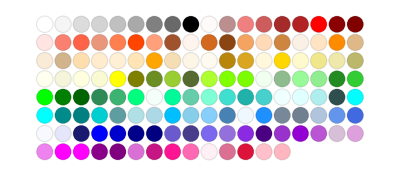

```mathematica
ColorData["HTML","Panel"]
```

```mathematica
ptClrs={
"ell"->Black,
"med"->Darker@Red,
"bar"->Brown,
"inc"->Darker@Green,
"ort"->Orange,
"cir"->Purple,
"npc"->ColorData["HTML","PaleVioletRed"],
"exc"->Darker@Green,
"ex12"->Darker@Green,
"ex23"->Darker@Green,
"ex31"->Darker@Green,
"dar"->ColorData["HTML","Navy"],
"x144"->ColorData["HTML","Navy"],
"x59"->ColorData["HTML","OrangeRed"],
"feu"-> ColorData["HTML","DarkKhaki"],
"antifeu"->ColorData["HTML","SlateGray"],
"anticompl"->Blue,
"steiner"->Brown,
"steinerinell"->Brown,
"x88"->Darker@Cyan,
"x100"->ColorData["HTML","SlateGray"],
"nag"->ColorData["HTML","MediumAquamarine"],
"mit"->Red(*Lighter@Blue*),
"sym"->ColorData["HTML","DodgerBlue"],
"bev"->Lighter@Purple,
"ger"->Darker@Cyan,
"spi"->ColorData["HTML","SpringGreen"],
"nap"->Red,
"hex"->Pink,
(* overrides *)
"red"->Red,
"green"->Green,
"blue"->Blue
};
```

```mathematica
ptClrs
```

{ell→-Graphics-,med→-Graphics-,bar→-Graphics-,inc→-Graphics-,ort→-Graphics-,cir→-Graphics-,npc→-Graphics-,exc→-Graphics-,ex12→-Graphics-,ex23→-Graphics-,ex31→-Graphics-,dar→-Graphics-,x144→-Graphics-,x59→-Graphics-,feu→-Graphics-,antifeu→-Graphics-,anticompl→-Graphics-,steiner→-Graphics-,steinerinell→-Graphics-,x88→-Graphics-,x100→-Graphics-,nag→-Graphics-,mit→-Graphics-,sym→-Graphics-,bev→-Graphics-,ger→-Graphics-,spi→-Graphics-,nap→-Graphics-,hex→-Graphics-,red→-Graphics-,green→-Graphics-,blue→-Graphics-}

```mathematica
Clear@plotEllb;
plotEllb[a_,b_,clr_:("ell"/.ptClrs)]:=Graphics[{
If[SameQ[clr,None],{},{If[ListQ@clr,Sequence@@clr,clr],Circle[{0,0},{a,b}]}]}];
Clear@plotEll;
plotEll[a_,clr_:("ell"/.ptClrs)]:=plotEllb[a,1,clr];
```

```mathematica
Clear@plotEllbAxesLow;
plotEllbAxesLow[a_,b_]:=Graphics@{Dashed,Gray,Thickness@Medium,{Line@{{-a,0},{a,0}},Line@{{0,-b},{0,b}}}};
```

```mathematica
Clear@plotEllAxesLow;
plotEllAxesLow[a_]:=plotEllbAxesLow[a,1];
```

```mathematica
Clear@plotEllAxes;plotEllAxes[a_,clr_:("ell"/.ptClrs)]:=Graphics@@Show[{plotEll[a,clr],plotEllAxesLow[a]}]
Clear@plotEllbAxes;
plotEllbAxes[a_,b_,clr_:("ell"/.ptClrs)]:=Graphics@@Show[{plotEllb[a,b,clr],plotEllbAxesLow[a,b]}]
```

```mathematica
Clear@plotEllFillb;
plotEllFillb[a_,b_,clrFill_,clr_:("ell"/.ptClrs)]:=Graphics[{
If[SameQ[clrFill,None],{},{If[ListQ@clrFill,Sequence@@clrFill,clrFill],Disk[{0,0},{a,b}]}],
If[SameQ[clr,None],{},{If[ListQ@clr,Sequence@@clr,clr],Circle[{0,0},{a,b}]}]
}];
Clear@plotEllFill;plotEllFill[a_,clrFill_,clr_:("ell"/.ptClrs)]:=plotEllFillb[a,1,clrFill,clr];
```

```mathematica
(*Clear@plotEll;
plotEll[a_,clr_:("ell"/.ptClrs)]:=ParametricPlot[{N[a] Cos[u],Sin[u]},{u,0.0,2.0π},
PlotStyle->clr,PerformanceGoal->"Quality"];
plotEllFill[a_,clrFill_,clr_:("ell"/.ptClrs)]:=Module[{int,ext},
int=ParametricPlot[r{N[a] Cos[u],Sin[u]},{u,0.0,2.0π},{r,0,1},
PlotStyle->clrFill,PerformanceGoal->"Quality"];
ext=plotEll[a,clr];
Show[{int,ext}]];
plotEllb[a_,b_,clr_:("ell"/.ptClrs)]:=ParametricPlot[{N[a] Cos[u],N[b]Sin[u]},{u,0.0,2.0π},
PlotStyle->clr,PerformanceGoal->"Quality"];*)
```

```mathematica
drawArrow[p0_,phat_,l_]:=Arrow[{p0,ray[p0,phat,l]}];
```

```mathematica
Clear@drawOrbit;
Options@drawOrbit={lgt->.25,drNormals->True,pSize->16,drVtxLabels->True,clr->{Thick,Darker@Blue}};
drawOrbit[orbitData_,OptionsPattern[](*lgt_:.25,drawNormals_:True,psize_:16*)]:=Module[{normals,orbit,halfAlpha},
orbit="orbit"/.orbitData;
normals="normals"/.orbitData;
halfAlpha="halfAlpha"/.orbitData;
Graphics[{
PointSize[Large],Arrowheads[Medium],
{OptionValue@clr,Point@orbit},
{FaceForm[GrayLevel@.9],EdgeForm@OptionValue@clr,Polygon@orbit},
If[OptionValue@drNormals,
{Black,
MapThread[drawArrow[#1,#2,OptionValue@lgt]&,{orbit,normals}],
Dashed,
drawArrow[orbit[[1]],"nRot"/.orbitData,OptionValue@lgt],
drawArrow[orbit[[1]],"nRotNeg"/.orbitData,OptionValue@lgt],
Text["α",ray[orbit[[1]],halfAlpha ,.33OptionValue@lgt]]},{}],
If[OptionValue@drVtxLabels,MapThread[txtSubscript["P",ToString@#1,OptionValue@pSize,ray[#2,-#3,.33OptionValue@lgt]]&,
{{1,2,3},orbit,normals}],{}]}]
];
```

```mathematica
Clear@drawOneNotable;drawOneNotable[clr_,at_,txt_,dx_:1.5,dy_:0,fntSize_:12]:={clr,Point@at,Text[Style[txt,fntSize],at,{dx,dy}]};
circOneNotable[clr_,at_,rad_,txt_,dx_:1.5,dy_:0,fntSize_:12]:={clr,Circle[at,rad],Text[Style[txt,fntSize],at,{dx,dy}]};
Clear@drawNotableLines;drawNotableLines[notables_]:=Graphics@{Darker[Gray],Dashed,
(* euler line: cir,bar,npc,ort *)
Line[{"cir","ort"}/.notables],
(* npc to feuerbach: npc,inc,feu *)
Line[{"npc","feu"}/.notables],
(* mittenpunkt to symmedian: mit,inc,sym *)
Line[{"mit","sym"}/.notables],
(* gergonne to mit: ger,bar,mit *)
Line[{"mit","ger"}/.notables],
(* nagel line: nag,bar,spi,inc *)
Line[{"nag","inc"}/.notables]};
Clear@drawNotables;
drawNotables[notables_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[(#/.ptClrs),(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
drawNotablesSingleClr[notables_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[clr,(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@circNotables;
circNotables[notables_,rad_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[(#/.ptClrs),(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@circNotablesSingleClr;
circNotablesSingleClr[notables_,rad_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[clr,(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@drawSomeNotables;
drawSomeNotables[notables_,nots_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[(#/.ptClrs),(#/.notables),prefix<>#]&/@nots}];
Clear@drawBasicNotables;
drawBasicNotables[notables_,prefix_:""]:=drawSomeNotables[notables,{"inc","bar","ort","cir","npc","mit","feu","ger"},prefix];
Clear@drawBasicNotablesSingleClr;
drawBasicNotablesSingleClr[notables_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[clr,(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
Clear@circBasicNotables;
circBasicNotables[notables_,rad_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[(#/.ptClrs),(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
Clear@circBasicNotablesSingleClr;
circBasicNotablesSingleClr[notables_,rad_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[clr,(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
```

## Circumbilliard (using linear algebra)

```mathematica
ellExtremum[{mx_,my_},{vx_,vy_},{c1_,c2_,c3_,c4_,c5_},t_]=Module[{xt,yt},
xt=mx+t vx;
yt=my+t vy;
Collect[1+c1 xt+c2 yt+c3 xt yt+c4 xt^2+c5 yt^2,t]]
```

1+c1 mx+c4 mx^2+c2 my+c3 mx my+c5 my^2+t (c1 vx+2 c4 mx vx+c3 my vx+c2 vy+c3 mx vy+2 c5 my vy)+t^2 (c4 vx^2+c3 vx vy+c5 vy^2)

```mathematica
(* by symmetry, b=0 of the quadratic*)
Clear@ellExtremumSym;
ellExtremumSym[{mx_,my_},{vx_,vy_},{c1_,c2_,c3_,c4_,c5_}]:=Module[{a,c,d,sqrtd,sol},
a=c4 vx^2+c3 vx vy+c5 vy^2;
(* b=c1 vx+2 c4 mx vx+c3 my vx+c2 vy+c3 mx vy+2 c5 my vy; *)
c=1+c1 mx+c4 mx^2+c2 my+c3 mx my+c5 my^2;
(*(-b + sqrt(b2-4ac)/(2a)) => sqrt(-4ac)/(2a) => sqrt(-ac)/a*)  
sol=Sqrt[-c/a];(*Sqrt[-a*c]/a;*)(* sqrt(-a)*sqrt(c)/a => sqrt(c/a) *)
{sol,-sol}];
```

```mathematica
(* grad = { c1 + c3 y + 2 c4 x, c2 + c3 x + 2 c5 y *)
Clear@circumTangent;circumTangent[{c1_,c2_,c3_,c4_,c5_},{x_,y_}]:=Module[{grad,tang},
grad={c1+c3 y+2c4 x,c2+c3 x+2c5 y};
tang=perp@grad;
tang];
```

```mathematica
Clear@getHessianDet;
getHessianDet[tri_,ctr_]:=Module[{mtx123,mtx45,mtx,rhs,ls,hess},
(* c1 x + c2 y + c3 x y + c4 x^2 + c5 y^2 == -1 *)
(* grad = { c1 + c3 y + 2 c4 x, c2 + c3 x + 2 c5 y *)
mtx123={#[[1]],#[[2]],#[[1]]*#[[2]],#[[1]]^2,#[[2]]^2}&/@tri;
mtx45={
{1,0,ctr[[2]],2ctr[[1]],0},
{0,1,ctr[[1]],0,2ctr[[2]]}};
mtx=Join[mtx123,mtx45];
rhs={-1,-1,-1,0,0};
ls=LinearSolve[mtx,rhs];
hess={{2ls[[4]],ls[[3]]},{ls[[3]],2ls[[5]]}};
Det[hess]];
```

```mathematica
Clear@getCircumAny;
getCircumAny[orbit_,ctr_]:=Module[{mtx123,mtx45,mtx,rhs,ls,hess,vals,vects,lengths,lgt1,lgt2,vertices,valsMinMax,orbitTangents,area,major,minor,c,fs},
(* c1 x + c2 y + c3 x y + c4 x^2 + c5 y^2 == -1 *)
(* grad = { c1 + c3 y + 2 c4 x, c2 + c3 x + 2 c5 y *)
mtx123={#[[1]],#[[2]],#[[1]]*#[[2]],#[[1]]^2,#[[2]]^2}&/@orbit;
mtx45={
{1,0,ctr[[2]],2ctr[[1]],0},
{0,1,ctr[[1]],0,2ctr[[2]]}};
mtx=Join[mtx123,mtx45];
rhs={-1,-1,-1,0,0};
ls=LinearSolve[mtx,rhs];
hess={{2ls[[4]],ls[[3]]},{ls[[3]],2ls[[5]]}};
{vals,vects}=Eigensystem@hess;
lgt1=Abs[First@ellExtremumSym[ctr,vects[[1]],ls]];
lgt2=lgt1*Sqrt[vals[[1]]/vals[[2]]];
lengths={lgt1,lgt2};
valsMinMax=If[Abs@vals[[1]]<Abs@vals[[2]],{vals[[1]],vals[[2]]},{vals[[2]],vals[[1]]}];
major=If[Abs@vals[[1]]<Abs@vals[[2]],vects[[1]],vects[[2]]];
minor=If[Abs@vals[[1]]<Abs@vals[[2]],vects[[2]],vects[[1]]];
c=Sqrt[Abs[lgt2^2-lgt1^2]];
fs={ctr+Sign[valsMinMax[[1]]]major c,ctr-Sign[valsMinMax[[1]]]major c};
orbitTangents=circumTangent[ls,#]&/@orbit;
vertices=MapThread[(ctr+#1*#2)&,{lengths,vects}];
area=π*lengths[[1]]*lengths[[2]];
<|"ctr"->ctr,"coeffs"->Chop@ls,"vals"->Chop@vals,"valsMinMax"->valsMinMax,"axes"->Chop@vects,"major"->major,"minor"->minor,"minorVal"->valsMinMax[[1]],"majorVal"->valsMinMax[[2]],"lengths"->lengths,"ratio"->safeDiv[lgt1,lgt2],"prod"->lgt1*lgt2,"vertices"->Chop@vertices,"foci"->fs,"c"->c,
"orbit"->orbit,"orbitTangents"->orbitTangents,"area"->area|>];
```

```mathematica
-Graphics-
-Graphics-
```

```mathematica
Clear@getEll5ctr;
getEll5ctr[ctrs5_]:=Module[{mtx,rhs,ls,discr,x0,y0},
(* A x^2 + B x y + C y^2 + D x + E y == -1 *)
mtx={#[[1]]^2,#[[1]]*#[[2]],#[[2]]^2,#[[1]],#[[2]]}&/@ctrs5;
rhs={-1,-1,-1,-1,-1};
ls=LinearSolve[mtx,rhs];
discr=ls[[2]]^2-4ls[[1]]ls[[3]];
x0=(2*ls[[3]]*ls[[4]]-ls[[2]]ls[[5]])/discr;
y0=(2*ls[[1]]*ls[[5]]-ls[[2]]ls[[4]])/discr;
{x0,y0}];
```

```mathematica
Module[{a=1.5,ps},
ps=Table[N@{a Cos[t]+5,Sin[t]+7},{t,0,2π,2π/7}];
getEll5ctr[Take[ps,5]]]
```

{5.,7.}

```mathematica
Clear@getCircumMit;
getCircumMit[orbit_]:=Module[{ctr},
ctr=getMittenTrilin[orbit,triLengthsRL@orbit];
getCircumAny[orbit,ctr]];
(* Steiner Circumellipse *)
Clear@getCircumBar;getCircumBar[orbit_]:=getCircumAny[orbit,getBaricenter@@orbit];
```

```mathematica
getCircumMit[orbitNormals[1.5,π/3.][[1]]]
```

<|ctr→{0.,-6.24567×10^-16},coeffs→{0,0,0,-0.444444,-1.},vals→{-2.,-0.888889},valsMinMax→{-0.888889,-2.},axes→{{0,1.},{-1.,0}},major→{-1.,-4.91566×10^-16},minor→{-4.91566×10^-16,1.},minorVal→-0.888889,majorVal→-2.,lengths→{1.,1.5},ratio→0.666667,prod→1.5,vertices→{{0,1.},{-1.5,0}},foci→{{1.11803,-7.49793×10^-17},{-1.11803,-1.17415×10^-15}},c→1.11803,orbit→{{0.75,0.866025},{1.34925,-0.436921},{-1.49317,-0.0953041}},orbitTangents→{{1.73205,-0.666667},{-0.873842,-1.19933},{-0.190608,1.32726}},area→4.71239|>

```mathematica
(* {ctrLab->"*",drTri->False,drOrbitTangents->False,ps->-Graphics-,drVertices->False,drLgl->0.2,labClr->-Graphics-,labPos->{-1.25,-1.25},labSize->20} *)
```

```mathematica
Clear@drawCircumAnyLow;
Options@drawCircumAnyLow={ctrLab->"*",drAxes->True,drTri->False,drOrbitTangents->False,ps->Black,drVertices->False,drFoci->False,drLgl->.2,labClr->Darker@Red,labPos->{-1.25,-1.25},labSize->20};
drawCircumAnyLow[cII_,tri_,OptionsPattern[]]:=Module[{o,vl,v,ul,u,pp,ax1,ax2,gr,grTri,grGrads,ps2},
o=cII["ctr"];
vl=cII["lengths"][[1]];
v=cII["axes"][[1]];
ul=cII["lengths"][[2]];
u=cII["axes"][[2]];
pp=ParametricPlot[o+vl Cos[t]v+ul Sin[t] u,{t,0,2π},PlotStyle->OptionValue@ps];
ax1=Graphics[{Dashed,OptionValue@ps,Line@{o-vl v,o+vl v}}];
(*ParametricPlot[(o+vl v)t+(o-vl v)(1-t),{t,0,1},PlotStyle->{Dashed,OptionValue@ps}];*)
ax2=Graphics[{Dashed,OptionValue@ps,Line@{o-ul u,o+ul u}}];(*ParametricPlot[(o+ul u)t+(o-ul u)(1-t),{t,0,1},PlotStyle->{Dashed,OptionValue@ps}];*)
grTri=If[OptionValue@drTri,{FaceForm@{OptionValue@ps,Opacity@.1},EdgeForm@OptionValue@ps,EdgeForm@{Thick,Blue},Polygon@tri},{}];
grGrads=If[OptionValue@drOrbitTangents,{Arrowheads@Medium,OptionValue@ps,MapThread[Arrow@{#1,#2}&,{cII["orbit"],cII["orbit"]+.5norm/@cII["orbitTangents"]}]},{}];
ps2=OptionValue@ps;
gr={
If[OptionValue@drVertices,{PointSize@Large,Black,Point@tri,ellLabelPoints[1,tri,"P",16,OptionValue@drLgl]},{}],
If[ListQ@ps2,Sequence@@ps2,ps2],
If[OptionValue@drFoci,{Directive[OptionValue@ps],PointSize@Medium,Point@cII["foci"]},{}],
{PointSize@Large,OptionValue@labClr,Point@o,Text[Style[OptionValue@ctrLab,OptionValue@labSize],o,OptionValue@labPos]}
};
Show[{If[OptionValue@drAxes,{ax1,ax2},{}],pp,Graphics/@{grTri,gr,grGrads}}]];
```

```mathematica
Clear@drawCircumAny;
Options@drawCircumAny=Options@drawCircumAnyLow;
drawCircumAny[tri_,ctr_,opts:OptionsPattern[]]:=drawCircumAnyLow[getCircumAny[tri,ctr],tri,{opts}];
```

```mathematica
Clear@drawCircumMit;
Options@drawCircumMit=Options@drawCircumAnyLow;drawCircumMit[tri_,opts:OptionsPattern[]]:=drawCircumAny[tri,getMittenTrilin[tri,triLengthsRL@tri],{opts}];
(* Steiner Circumellipse *)
Clear@drawCircumBar;
Options@drawCircumBar=Options@drawCircumAnyLow;
drawCircumBar[tri_,opts:OptionsPattern[]]:=drawCircumAny[tri,getBaricenter@@tri,{opts}];
```

```mathematica
Clear@drawSteinerInellipse;
drawSteinerInellipse[tri_,opts:OptionsPattern[]]:=Module[{meds},
meds=getMedians@@tri;
drawCircumAny[meds,getBaricenter@@tri,{opts}]
];
Clear@drawCircumExc;drawCircumExc[tri_,opts:OptionsPattern[]]:=drawCircumAny[tri,getMittenTrilin[tri,triLengthsRL@tri],{opts}];
Clear@drawCircumInc;drawCircumInc[tri_,opts:OptionsPattern[]]:=drawCircumAny[tri,getIncenterTrilin[tri,triLengthsRL@tri],{opts}];
```

## Conic Coeffs

```mathematica
(* A x^2 + B x y + C y^2 + D x + E y + F = 0 *) 
(* axx x^2 + 2 axy x y + ayy y^2 + 2 bx x + 2by y + C = 0 *) 

(* A=axx, B=2 axy, C = ayy, D = 2 bx,E = 2 by *)
```

```mathematica
Clear@getConicCoeffs;
getConicCoeffs[fivePs_]:=Module[{mtx,rhs,coeffs,det,isHyp,hess,evals,evecs,majorAxis,S,a,b,ctr,c2,c,foci,errs,err2sum},
mtx={
(* A *) #[[1]]^2,
(* B *)#[[1]]*#[[2]],
(* C *) #[[2]]^2,
(* D *) #[[1]],
(* E *)#[[2]]
}&/@fivePs;
(*Print["m=",MatrixForm@mtx,"; det=",Det[mtx]];*)
rhs=ConstantArray[-1,5];
coeffs=LinearSolve[mtx,rhs];
errs=Chop[(coeffs[[1]]#[[1]]^2+
coeffs[[2]]#[[1]]#[[2]]+
coeffs[[3]]#[[2]]^2+
coeffs[[4]]#[[1]]+
coeffs[[5]]#[[2]]+1)&/@fivePs];
err2sum=Total[errs^2];
det=coeffs[[1]]*coeffs[[3]]-coeffs[[2]]coeffs[[2]]/4;
isHyp=det<0;
(* xc=-(bx*ayy-axy*by)/det;
yc=-(axx*by-axy*bx)/det; *)
ctr={2 coeffs[[3]]coeffs[[4]]-coeffs[[2]]coeffs[[5]],2 coeffs[[1]]coeffs[[5]]-coeffs[[2]]coeffs[[4]]}/(-4 det);

hess={{coeffs[[1]],coeffs[[2]]/2},{coeffs[[2]]/2,coeffs[[3]]}};
{evals,evecs}=Eigensystem@hess;
majorAxis=If[evals[[1]]<evals[[2]],evecs[[1]],evecs[[2]]];
(* axx * ayy - axy^2 *)
(* it will be zero if hyp wrt tr *)
S=Det[{
{coeffs[[1]],coeffs[[2]]/2,coeffs[[4]]/2},
{coeffs[[2]]/2,coeffs[[3]],coeffs[[5]]/2},
{coeffs[[4]]/2,coeffs[[5]]/2,1}}];
a=Sqrt@Abs[S/(Min[evals[[1]],evals[[2]]]det)];
b=Sqrt@Abs[S/(Max[evals[[1]],evals[[2]]]det)];

c2=If[isHyp,a^2+b^2,a^2-b^2];
c=Sqrt@c2;
foci={ctr+c majorAxis,ctr-c majorAxis };
<|"fivePs"->fivePs,"discr"->S,"det"->det,"isHyp"->isHyp,
"ctr"->ctr,"foci"->foci,"a"->a,"b"->b,"c"->c,"c2"->c2,"coeffs"->coeffs,"majorAxis"->majorAxis,"errs"->errs,"err2sum"->err2sum|>];
```

```mathematica
(* https://en.wikipedia.org/wiki/Hyperbola *)
(* axx x^2 + 2 axy x y + ayy y^2 + 2 bx x + 2by y + C = 0 *) 
Clear@getConicCoeffsOld;
getConicCoeffsOld[fivePs_]:=Module[{mtx,rhs,axx,ayy,axy,bx,by,discr,det,xc,yc,ctr,a,b,c,r1,r2,l1,l2,c2,hess,eigenvals,eigenvecs,majorAxis,foci},
mtx={
(* axx *) #[[1]]^2,
(* ayy *) #[[2]]^2,
(* 2 axy *) 2#[[1]]*#[[2]],
(* 2 bx *) 2#[[1]],
(* 2 by *) 2#[[2]]
}&/@fivePs;
(*Print["m=",MatrixForm@mtx,"; det=",Det[mtx]];*)
rhs=ConstantArray[-1,5];
{axx,ayy,axy,bx,by}=LinearSolve[mtx,rhs];
discr=Det[{
{axx,axy,bx},
{axy,ayy,by},
{bx,by,1}}];
det=axx*ayy-axy^2;
hess={{axx,axy},{axy,ayy}};
{eigenvals,eigenvecs}=Eigensystem@hess;
majorAxis=If[eigenvals[[1]]<eigenvals[[2]],eigenvecs[[1]],eigenvecs[[2]]];
(* axx * ayy - axy^2 *)
(* it will be zero if hyp wrt tr *)
xc=-(bx*ayy-axy*by)/det;
yc=-(axx*by-axy*bx)/det;
ctr={xc,yc};
(*tan2phi=(2axy)/(axx-ayy);*)
(*sin2phi=axy;
cos2phi=(axx-ayy)/2;
phi=ArcTan[cos2phi,sin2phi]/2;*)
(* ronaldo: considerar quadrante do par ordenado (c2p,s2p) *)
(* (c,s) = coseno e seno do angulo normal *)
(*  Q1:c>0,s>0; Q2:c>0,s>0; Q3:c<0,s>0; Q4:c<0,s>0 *)
(* ou seja, seno sempre positivo, coseno negativo se em Q2 ou Q3, i.e., cos2phi < 0 *)
{r1,r2}=quadRootsUnprot[1,-axx-ayy,det];
(* ronaldo: trocar a por b *)
l1=Min[Abs/@{r1,r2}];
l2=Max[Abs/@{r1,r2}];
(*{l1,l2}=quadRootsUnprot[1,-axx-ayy,det];*)
a=Sqrt@Abs[discr/(l1 det)];
b=Sqrt@Abs[discr/(l2 det)];
c2=If[det<0,a^2+b^2,a^2-b^2];
c=Sqrt@c2;
foci={ctr+c majorAxis,ctr-c majorAxis };
<|"fivePs"->fivePs,"discr"->discr,"det"->det,"isHyp"->(det<0),
"ctr"->ctr,"foci"->foci,"l1"->l1,"l2"->l2,"a"->a,"b"->b,"c"->c,"c2"->c2,"coeffs"->{axx,ayy,axy,bx,by},"majorAxis"->majorAxis|>];
```

```mathematica
Clear@drawConic;
Options@drawConic={ctrLab->"",ps->Directive[Thick,Darker@Red],lgt->.1,showFoci->False,psAxes->Directive[Dashed,Black],maxX->2,maxY->2};
drawConic[conic_,OptionsPattern[]]:=Module[{o,a,v,b,u,ctr,fs,pp,ax,gr,foci,maxT=π,cp,sp,ell},
o=conic["ctr"];
a=conic["a"];
b=conic["b"];
(* major axis *)
v=conic["majorAxis"];
u=perp@v;
foci=conic["foci"];
{pp,ax}=If[conic["isHyp"],
{ParametricPlot[{o+a Cosh[t]v+b Sinh[t] u,o-a Cosh[t]v-b Sinh[t] u},{t,-maxT,maxT},PlotStyle->OptionValue@ps],Graphics[{OptionValue@psAxes,Line@{o-OptionValue@maxX(v+u (b/a)),o+OptionValue@maxX(v+u (b/a))},Line@{o-OptionValue@maxY(v-u (b/a)),o+OptionValue@maxY(v-u (b/a))}}]},
{ParametricPlot[o+a v Cos@t+b u Sin@t,{t,0,2π},PlotStyle->OptionValue@ps],
Graphics[{OptionValue@psAxes,Line@{o-a v,o+a v},Line@{o-b u,o+b u}}]}];
fs=Graphics@If[OptionValue@showFoci,{PointSize@Medium,First@Cases[OptionValue@ps,_RGBColor],Point@foci,Thick,Line@foci,Text[Style["f",20],#,{0,-1}]&/@foci},{}];
gr=Graphics[{First@Cases[OptionValue@ps,_RGBColor],PointSize@Large,Point@o,If[OptionValue@ctrLab!="",ellLabelTxt[conic["ellA"],o,Style[OptionValue@ctrLab,20],OptionValue@lgt],{}]}];
Show[{fs,ax,pp,gr}]];
```

```mathematica
Clear@x;Clear@y;
```

```mathematica
Clear@drawConicImplicit;
Options@drawConicImplicit={ctrLab->"",ps->Directive[Thick,Darker@Red],lgt->.1,showFoci->False,psAxes->Directive[Dashed,Black],maxX->2,maxY->2};
drawConicImplicit[conic_,OptionsPattern[]]:=Module[{coeffs,cp,gr},
coeffs=conic["coeffs"];
gr=Graphics[{PointSize@Large,OptionValue@ps,Point@conic["ctr"]}];
cp=ContourPlot[coeffs[[1]]x^2+coeffs[[2]]x y +coeffs[[3]]y^2+coeffs[[4]]x+coeffs[[5]]y+1==0,{x,-OptionValue@maxX,OptionValue@maxX},{y,-OptionValue@maxY,OptionValue@maxY},ContourStyle->OptionValue@ps];
Show[{cp,gr}]];
```

## Five Point Hyperbola, Feuerbach, and Excentral Jerabek

```mathematica
(* https://en.wikipedia.org/wiki/Hyperbola *)
(* axx x^2 + 2 axy x y + ayy y^2 + 2 bx x + 2by y + C = 0 *) Clear@getHypCoeffs5b;
Clear@getHypCoeffs5b;
getHypCoeffs5b[fivePs_,tr_]:=Module[{mtx,rhs,axx,ayy,axy,bx,by,discr,det,xc,yc,ctr,a,b,c,l1,l2,c2,hess,eigenvals,eigenvecs,majorAxis,foci,fiveErrs},
mtx={
(* axx *) #[[1]]^2,
(* ayy *) #[[2]]^2,
(* 2 axy *) 2#[[1]]*#[[2]],
(* 2 bx *) 2#[[1]],
(* 2 by *) 2#[[2]]
}&/@((#-tr)&/@fivePs);(* trick to remove ill-conditioning on origin-centered conics *)
(*Print["m=",MatrixForm@mtx,"; det=",Det[mtx]];*)
rhs=ConstantArray[-1,5];
{axx,ayy,axy,bx,by}=LinearSolve[mtx,rhs];
fiveErrs=(axx #[[1]]^2 + 2 axy #[[1]]#[[2]] + ayy #[[2]]^2 + 2 bx #[[1]] + 2by #[[2]]+1)&/@((#-tr)&/@fivePs);
hess={{axx,axy},{axy,ayy}};
{eigenvals,eigenvecs}=Eigensystem@hess;
majorAxis=If[eigenvals[[1]]<eigenvals[[2]],eigenvecs[[1]],eigenvecs[[2]]];
(* axx * ayy - axy^2 *)
discr=Det[{
{axx,axy,bx},
{axy,ayy,by},
{bx,by,1}}];
det=axx*ayy-axy^2;
(* it will be zero if hyp wrt tr *)
xc=-(bx*ayy-axy*by)/det;
yc=-(axx*by-axy*bx)/det;
ctr={xc,yc}+tr;
(*tan2phi=(2axy)/(axx-ayy);*)
(*sin2phi=axy;
cos2phi=(axx-ayy)/2;
phi=ArcTan[cos2phi,sin2phi]/2;*)
{l1,l2}=quadRootsUnprot[1,-axx-ayy,det];
a=Sqrt@Abs[-discr/(l1 det)];
b=Sqrt@Abs[-discr/(l2 det)];
c2=a^2+b^2;
c=Sqrt@c2;
foci={ctr+c majorAxis,ctr-c majorAxis };
<|"fivePs"->fivePs,"fiveErrs"->fiveErrs,"discr"->discr,"det"->det,"isHyp"->(det<0),
"ctr"->ctr,"foci"->foci,"l1"->l1,"l2"->l2,"a"->a,"b"->b,"c"->c,"c2"->c2,"coeffs"->{axx,ayy,axy,bx,by},"majorAxis"->majorAxis|>];
```

```mathematica
(* https://en.wikipedia.org/wiki/Hyperbola *)
(* axx x^2 + 2 axy x y + ayy y^2 + 2 bx x + 2by y + C = 0 *)
```

```mathematica
Clear@d;
Module[{l,d,h},
d=getDelta[a,1];
l=(a^2/(a^2-1)) Sqrt[2d-a^2-1];
h=(a^2+d+1)/(a^2+d);
Solve[h/l==Sqrt[3]/3,a,Reals]]
```

{{a→-√(-3+4 √3)},{a→√(-3+4 √3)}}

```mathematica
Clear@getHypCoeffs5bNoTr;
getHypCoeffs5bNoTr[fivePs_]:=Module[{randCtr,mtx,rhs,axx,ayy,axy,bx,by,fiveErrs,discr,det,xc,yc,ctr,hess,eigenvals,eigenvecs,majorAxis,
l1,l2,a,b,c2,c,r1,r2,foci},
randCtr=RandomReal[{-1,1},2];
mtx={
(* axx *) #[[1]]^2,
(* ayy *) #[[2]]^2,
(* 2 axy *) 2#[[1]]*#[[2]],
(* 2 bx *) 2#[[1]],
(* 2 by *) 2#[[2]]
}&/@((#-randCtr)&/@fivePs);
(* trick to remove ill conditioning on origin-centered *)
(*Print["m=",MatrixForm@mtx,"; det=",Det[mtx]];*)
rhs=ConstantArray[-1,5];
{axx,ayy,axy,bx,by}=LinearSolve[mtx,rhs];
fiveErrs=(axx #[[1]]^2 + 2 axy #[[1]]#[[2]] + ayy #[[2]]^2 + 2 bx #[[1]] + 2by #[[2]]+1)&/@fivePs;
(* axx * ayy - axy^2 *)
discr=Det[{
{axx,axy,bx},
{axy,ayy,by},
{bx,by,1}}];
det=axx*ayy-axy^2;
(* restores to center *)
xc=-(bx*ayy-axy*by)/det;
yc=-(axx*by-axy*bx)/det;
(* add random center back *)
ctr={xc,yc}+randCtr;
hess={{axx,axy},{axy,ayy}};
{eigenvals,eigenvecs}=Eigensystem@hess;
majorAxis=If[eigenvals[[1]]<eigenvals[[2]],eigenvecs[[1]],eigenvecs[[2]]];
(* ronaldo: considerar quadrante do par ordenado (c2p,s2p) *)
(* (c,s) = coseno e seno do angulo normal *)
(*  Q1:c>0,s>0; Q2:c>0,s>0; Q3:c<0,s>0; Q4:c<0,s>0 *)
(* ou seja, seno sempre positivo, coseno negativo se em Q2 ou Q3, i.e., cos2phi < 0 *)
{r1,r2}=quadRootsUnprot[1,-axx-ayy,det];
(* ronaldo: trocar a por b *)
l1=Min[Abs/@{r1,r2}];
l2=Max[Abs/@{r1,r2}];
a=Sqrt@Abs[-discr/(l1 det)];
b=Sqrt@Abs[-discr/(l2 det)];
c2=a^2+b^2;
c=Sqrt@c2;
foci={ctr+c majorAxis,ctr-c majorAxis};
<|"fivePs"->fivePs,"fiveErrs"->fiveErrs,"discr"->discr,"det"->det,"isHyp"->(det<0),
"ctr"->ctr,"foci"->foci,"l1"->l1,"l2"->l2,"a"->a,"b"->b,"c"->c,"c2"->c2,"coeffs"->{axx,ayy,axy,bx,by},"eigenvals"->eigenvals,"eigenvecs"->eigenvecs,"majorAxis"->majorAxis|>];
```

```mathematica
Clear@drawHyp5b;
Options@drawHyp5b={ctrLab->"",ps->{Darker@Red},lgt->.1,showFoci->False,psAxes->Directive[Dashed,Black],fntSize->16};
drawHyp5b[hyp5_,OptionsPattern[]]:=Module[{o,a,v,b,u,ctr,fs,pp1,pp2,ax1,ax2,gr,foci,maxAsymptT=3,maxT=π,cp,sp},
o=hyp5["ctr"];
a=hyp5["a"];
b=hyp5["b"];
(* major axis *)
v=hyp5["majorAxis"];
u=perp@v;
foci=hyp5["foci"];
pp1=ParametricPlot[o+a Cosh[t]v+b Sinh[t] u,{t,-maxT,maxT},PlotStyle->OptionValue@ps];
pp2=ParametricPlot[o-a Cosh[t]v-b Sinh[t] u,{t,-maxT,maxT},PlotStyle->OptionValue@ps];
(* axes could be lines Line@{} *)
(*ax1=ParametricPlot[o+v t+u (b/a)t,{t,-maxAsymptT,maxAsymptT},PlotStyle->{Dashed,OptionValue@psAxes}];
ax2=ParametricPlot[o+v t-u (b/a)t,{t,-maxAsymptT,maxAsymptT},PlotStyle->{Dashed,OptionValue@psAxes}];*)
ax1=Graphics[{OptionValue@psAxes,Line@{o-maxAsymptT(v+u (b/a)),o+maxAsymptT(v+u (b/a))}}];
ax2=Graphics[{OptionValue@psAxes,Line@{o-maxAsymptT(v-u (b/a)),o+maxAsymptT(v-u (b/a))}}];
fs=Graphics@If[OptionValue@showFoci,{PointSize@Medium,First@Cases[OptionValue@ps,_RGBColor],Point@foci,Thick,Line@foci,Text[Style["F",OptionValue@fntSize],#,{0,-1}]&/@foci},{}];
gr=Graphics[{First@Cases[OptionValue@ps,_RGBColor],PointSize@Large,Point@o,If[OptionValue@ctrLab!="",ellLabelTxt[hyp5["ellA"],o,Style[OptionValue@ctrLab,20],OptionValue@lgt],{}]}];
Show[{fs,pp1,pp2,ax1,ax2,gr}]];
```

https://mathworld.wolfram.com/JerabekHyperbola.html
Jerabek Hyp goes thru:
3, 4 , 6 , 54, 64, 65, 66, 67, 68, 69, 70, 71, 72, 73, 74, 248, 265, 290, 695, 879, 895, 1173, 1175, 1176, 1177, 1242, 1243, 1244, 1245, 1246, 1439, 1798, 1903, 1942, 1987, 2213, 2435, 2574, 2575, 2992, 2993.

```mathematica
Clear@getJerabekHyp;
getJerabekHyp[tri_,sides_]:=Module[{fivePs,hyp5,ctr},
fivePs={Sequence@@tri,getOrthocenterTrilin[tri,sides],getSymmedianTrilin[tri,sides]};
ctr=getX125Trilin[tri,sides];
(* displace origin to avoid ill-conditioning, since mit=0 *)
(* ronaldo: quando ela passa pela origem, constant term -> 0 *)
hyp5=getHypCoeffs5b[fivePs,ctr]; (*RandomReal[{-1,1},2]];*)
Append[hyp5,<|"orbit"->tri,"sides"->sides,"ctr"->ctr,"ellA"->0,
"labels"->{"P_1","P_2","P_3","X_4","X_6"},
"ctrLabel"->"X_125",
"colors"->({"orbit","orbit","orbit","ort","sym"}/.ptClrs)|>]
];
```

```mathematica
Clear@getFeuerbachHyp;
getFeuerbachHyp[tri_,sides_]:=Module[{fivePs,hyp5,ctr},
fivePs={Sequence@@tri,getIncenterTrilin[tri,sides],getOrthocenterTrilin[tri,sides]};
ctr=getFeuerbachTrilin[tri,sides];
(* displace origin to avoid ill-conditioning, since mit=0 *)
hyp5=getHypCoeffs5b[fivePs,ctr]; (*RandomReal[{-1,1},2]];*)
Append[hyp5,<|"orbit"->tri,"sides"->sides,"ctr"->ctr,"ellA"->0,
"labels"->{"P_1","P_2","P_3","X_1","X_4"},
"ctrLabel"->"X_11",
"colors"->({"orbit","orbit","orbit","ort","sym"}/.ptClrs)|>]
];
```

```mathematica
Clear@getFeuerbachHypMitten;
getFeuerbachHypMitten[tri_,sides_]:=Module[{fivePs,hyp5,ctr},
fivePs={Sequence@@tri,getIncenterTrilin[tri,sides],getMittenTrilin[tri,sides]};
ctr=getFeuerbachTrilin[tri,sides];
(* displace origin to avoid ill-conditioning, since mit=0 *)
hyp5=getHypCoeffs5b[fivePs,ctr]; (*RandomReal[{-1,1},2]];*)
Append[hyp5,<|"orbit"->tri,"sides"->sides,"ctr"->ctr,"ellA"->0,
"labels"->{"P_1","P_2","P_3","X_1","X_9"},
"ctrLabel"->"X_11",
"colors"->({"orbit","orbit","orbit","ort","sym"}/.ptClrs)|>]
];
```

```mathematica
Clear@getJerabekHypExc;
getJerabekHypExc[tri_,sides_]:=Module[{exc,excSides},
exc=excentralTriangle[tri,sides];
excSides=triLengthsRL@exc;
getJerabekHyp[exc,excSides]];
```

```mathematica
Clear@getHypX100;
getHypX100[a_,tDeg_]:=Module[{o,n,s,exc,inc,mit,x100,fivePs,hyp5},
{o,n,s}=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[o,s];
inc=getIncenterTrilin[o,s];
mit=getMittenTrilin[o,s];
x100=getX100Trilin[o,s];
fivePs={inc,Sequence@@exc,mit};
(* displace origin to avoid ill-conditioning, since mit=0 *)
hyp5=getHypCoeffs5b[fivePs,x100]; (*RandomReal[{-1,1},2]];*)
Append[hyp5,<|"orbit"->o,"sides"->s,"ctr"->x100,"ellA"->a,
"labels"->{"X_1","E_12","E_23","E_31","X_9"},
"ctrLabel"->"X_100",
"colors"->({"inc","inc","inc","inc","mit"}/.ptClrs)|>]
];
```

```mathematica
Clear@getHypFeuerbach;
getHypFeuerbach[a_,tDeg_]:=Module[{o,n,s,inc,ort,feu,fivePs,hyp5},
{o,n,s}=orbitNormals[a,toRad@tDeg];
inc=getIncenterTrilin[o,s];
ort=getOrthocenterTrilin[o,s];
feu=getFeuerbachTrilin[o,s];
fivePs={Sequence@@o,inc,ort};
(* displace origin to avoid ill-conditioning, since mit=0 *)
hyp5=getHypCoeffs5b[fivePs,feu]; (*RandomReal[{-1,1},2]];*)
Append[hyp5,<|"orbit"->o,"sides"->s,"ctr"->feu,"ellA"->a,
"labels"->{"","","","X_1","X_4"},
"ctrLabel"->"X_11",
"colors"->({"ell","ell","ell","inc","ort"}/.ptClrs)|>]
];
```

## [*** paper 05] Chapple's Porism, J.H.Weaver Poristic, Boris Odehnal

William Chapple (1718-1781), Wikipedia: https://en.wikipedia.org/wiki/William_Chapple_(surveyor)

R≥2r, r≤R/2

Leonhard Euler published |OI|=d=Sqrt[R^2-2 R r] in 1765; this was found earlier by Chapple. In a 1746 essay in The Gentleman' s Magazine he states: when two circles are the incircle and circumcircle of a triangle, then there is an infinite family of triangles for which they are the incircle and circumcircle [...] significantly predates Poncelet' s own 1822 work in this area.

B. Odenhal, “Poristic Loci of Triangle Centers”, 2011, https:// www.geometrie.tuwien.ac.at/odehnal/pltc.pdf
J.H.Weaver, “Invariants of a Poristic System”, 1927: https://projecteuclid.org/download/pdf_1/euclid.bams/1183492031

Weaver Theorem I: In a poristic system of triangles, which has a fixed incirde and a fixed circumcircle, the line determined by the points of intersection of the bisectors of the exterior angles of the triangle with the opposite sides is a fixed line. 

Our comment: this is L1, the antiorthic axis, generated by intersections of the Excentral Sides and the opposite sides of ABC: https://youtu.be/vyHZ8fwyiE8

```mathematica
Clear@d;
```

```mathematica
getEulerOI[R_,r_]:=Sqrt[R(R-2 r)];
```

```mathematica
FullSimplify[(R+getEulerOI[R,r])/(R-getEulerOI[R,r])]
```

(-r+R+√(R (-2 r+R)))/r

```mathematica
(* conjecturing the axis ratio of the X3-centered excentral inconic is (R+d)/(R-d) *)
```

```mathematica
excIncX3AxisRatio[r_,R_]:=R/r(1+Sqrt[1-2r/R])-1;
```

```mathematica
excIncX3AxisRatio[.3625,1]
```

3.20525

```mathematica
dsolChapple[r_]=getEulerOI[1,r]
```

√(1-2 r)

```mathematica
rsolChapple[d_]=First[r/.Solve[getEulerOI[1,r]==d,r]]
```

1/2 (1-d^2)

```mathematica
Solve[rsolChapple[d]==r,d]
```

{{d→-√(1-2 r)},{d→√(1-2 r)}}

```mathematica
Solve[rsolChapple[d]==1/4,d]
```

{{d→-1/(√2)},{d→1/(√2)}}

```mathematica
FullSimplify[rsolChapple[(Sqrt@5+1)/2-1]]
```

1/4 (-1+√5)

```mathematica
N@%
```

0.309017

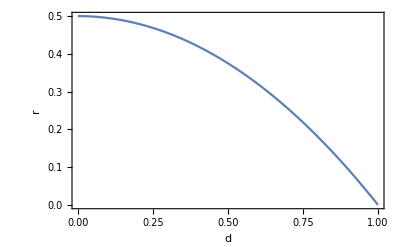

```mathematica
Plot[rsolChapple[d],{d,0,1},Frame->True,FrameLabel->(Style[#,{Black,16}]&/@{"d","r"})]
```

-Graphics-

```mathematica
getConvexHull[ps_]:=First[List@@First@ConvexHullMesh[ps]["BoundaryPolygons"]]
```

```mathematica
Module[{pts},
pts=RandomReal[{-1,1},{50,2}];
First[List@@First@ConvexHullMesh[pts]["BoundaryPolygons"]]]
```

{{-0.891772,0.351334},{-0.871432,-0.995068},{0.929891,-0.851284},{0.965234,-0.501716},{0.976377,0.385077},{0.799825,0.887084},{0.0513437,0.988548},{-0.542952,0.890125},{-0.69061,0.758611}}

```mathematica
getMacBeathInconic[tri_,sides_]:=Module[{ctr,persp,trils,touchPts},
(* foci are on X3 and X4 of excentral, i.e., X40 and X1 of reference *)
ctr=getNinepointCenterTrilin[tri,sides];
persp=getX264Trilin[tri,sides];
(* peter moses: X1742 is excentral's X264 *)
trils=getTrilinears[persp,tri,sides];
touchPts=cevianTriangle[tri,sides,trils];
getCircumAny[touchPts,ctr]];
```

```mathematica
getX3Inconic[tri_,sides_]:=Module[{ctr,persp,trils,touchPts},
(* foci are on X3 and X4 of excentral, i.e., X40 and X1 of reference *)
ctr=getCircumcenterTrilin[tri,sides];
persp=getX69Trilin[tri,sides];
(* peter moses: X1742 is excentral's X264 *)
trils=getTrilinears[persp,tri,sides];
touchPts=cevianTriangle[tri,sides,trils];
getCircumAny[touchPts,ctr]];
```

```mathematica
getPoristicCircumbilliardAR[r_,R_]:=Module[{rOvR=r/R},
Sqrt@(rOvR^2+(2*(rOvR+1))Sqrt@(-2*rOvR+1)+2)/Sqrt@(rOvR(rOvR+4))]
```

```mathematica
getPoristicCircumbilliardAR[.36266,1]
```

1.5

```mathematica
FullSimplify[getPoristicCircumbilliardAR[r,1],r>1]//TeXForm
```

\sqrt{\frac{r^2+2 \sqrt{1-2 r} (r+1)+2}{r (r+4)}}

```mathematica
poristicPer[d_,R_,cosT_]:=Sqrt@(2d R cosT+3 R^2-d^2)*(-4 d R cosT+3R^2+d^2)/(Sqrt@(R^2+d^2-2 d R cosT)*R);
```

#### Odehnal' s Poristic Vertices Parametrization

```mathematica
poristicVertices[R_,r_,t_]:=Module[{d,w,ct,st,p1,p2,p3,d0},
d=Sqrt[R(R-2r)];
ct=Cos@t;
st=Sin@t;
w=Sqrt[R^2-(d ct+r)^2];
d0=(d ct+r);
p1={ct d0-w st+d,d0 st+w ct};
p2={ct d0+w st+d,d0 st-w ct};
p3={R(2d R-(R^2+d^2)ct),R(d^2-R^2)st}/(R^2-2d R ct+d^2)+{d,0};
{p1,p2,p3}];
```

```mathematica
poristicVertices[1,.25,0]
```

{{1.66421,0.289735},{1.66421,-0.289735},{-0.292893,0.}}

```mathematica
getEulerOI[1,.25]
```

0.707107

```mathematica
chappleData[dsolChapple[.25],0.0001]["tri"]
```

{{1.74533×10^-6,-1.},{0.289735,0.957107},{-0.289736,0.957107}}

```mathematica
Clear@chappleData;
Options@chappleData={doTangential->False,odehnalVertices->False};chappleData[d_?NumberQ,tDeg_?NumberQ,OptionsPattern[]]:=Module[{R=1,cir,r,inc,tRad,p1,tangs,p2s,p3s,tri,med,act,exc,aoa ,x2,x5,x6,x9,x10,x11,x40,x44,x36,x57,x100,x1155,excMed,excMedL,excMedInc,tangential,triL,excL,weaverCtr,weaverR,npcHex,npcHexA,npcHexHull,npcHexHullA,npcHexL,tangsWeaver,tangsInc,powerWeaver,powerInc,powerIncExplicit,tangsCir,tangsExcCir,powerCir,powerExcCir,x9ctr,x9rad,cb,excIncX5,excIncX3,pedalX100,excMedPedalX100,circumX1,equalPowerIncR,equalPowerInc,tangsEqualPowerInc,equalPowerCirR,equalPowerCir,tangsEqualPowerCir,cosT,triPerRonaldo,cbFocusLocusCtr,cbFocusLocusRad,l31,orthicAxis,l663,excCircumX5,circumX10,excCircumX6,excCausticTouchPts},
cir={0,0};
r=rsolChapple[d];
inc={0,d};
tRad=toRad@tDeg;
If[OptionValue@odehnalVertices,
{p1,p2s,p3s}=perp[#-{d,0}]&/@poristicVertices[R,r,toRad@tDeg];
cosT=Cos[toRad@tDeg];
tri={p1,p2s,p3s},
p1={Sin@tRad,-Cos@tRad}; (* weaver style *)
tangs=tangsToCirc[inc,r,p1];
{p2s,p3s}=interRayCirc[#,#-p1,cir,R]&/@tangs;
cosT=-tangs[[2,2]]/r;
tri={p1,p2s[[2]],p3s[[2]]}];
triPerRonaldo=poristicPer[d,R,cosT];
triL=triLengthsRL@tri;
med=medialTriangle[tri,triL];
act=anticomplementaryTriangle[tri,triL];
tangential=If[OptionValue@doTangential,tangentialTriangle[tri,triL],{}];
exc=excentralTriangle[tri,triL];
excL=triLengthsRL@exc;
excCausticTouchPts=Module[{excTrils,x264exc},
x264exc=getX264Trilin[exc,excL];
excTrils=getTrilinears[x264exc,exc,excL];
cevianTriangle[exc,excL,excTrils]];
excMed=medialTriangle[exc,excL];
excMedL=triLengthsRL@excMed;
excMedInc=getIncenterTrilin[excMed,excMedL];
x5=getNinepointCenterTrilin[tri,triL];
x6=getSymmedianTrilin[tri,triL];
x10=getSpiekerTrilin[tri,triL];
x11=getFeuerbachTrilin[tri,triL];
x2=getBarycenterTrilin[tri,triL];
x9=getMittenTrilin[tri,triL];
(* from Odehnal pp 17: https://www.geometrie.tuwien.ac.at/odehnal/pltc.pdf *)
x9ctr={0,d(2R−r)/(4R+r)};
x9rad=2R(R-2r)/(4R+r);
x40=getBevanTrilin[tri,triL];
x44=getX44Trilin[tri,triL];
x36=getX36Trilin[tri,triL];
x57=getX57Trilin[tri,triL];
x100=getX100Trilin[tri,triL];
x1155=getX1155Trilin[tri,triL];
aoa=MapThread[interRaysUnprot[#1,#2-#1,#3,#4-#3]&,{tri,RotateLeft@tri,exc,RotateLeft@exc}];
weaverCtr={0,-R};
weaverR=Sqrt[R d(R+d)(R+d+r)]/d;
npcHex=Riffle[tri,excMed];
npcHexHull=getConvexHull[npcHex];
npcHexHullA=Abs@signedArea[npcHexHull];
npcHexA=Abs@signedArea[npcHex];
npcHexL=triPer[npcHex];
tangsWeaver=tangsToCirc[weaverCtr,weaverR,x1155];
powerWeaver=magn2[x1155-tangsWeaver[[1]]];
tangsInc=tangsToCirc[{0,d},r,x1155];
powerInc=magn2[x1155-tangsInc[[1]]];
powerIncExplicit=((d+R)/(2R))Sqrt[(3R-d)(4R^2-d R-d^2)/d];
tangsCir=tangsToCirc[{0,0},R,x1155];
powerCir=magn2[x1155-tangsCir[[1]]];
tangsExcCir=tangsToCirc[{0,-d},2R,x1155];
powerExcCir=magn2[x1155-tangsExcCir[[1]]];
cb=getCircumMit[tri];
cbFocusLocusCtr=x9ctr-{0,x9rad};
cbFocusLocusRad=magn[cb["foci"][[1]]-cbFocusLocusCtr];
circumX1=getCircumAny[tri,inc];
circumX10=getCircumAny[tri,x10];
excCircumX5=getCircumAny[exc,cir];
excCircumX6=getCircumAny[exc,x9];
excIncX5=getMacBeathInconic[exc,excL];
excIncX3=getX3Inconic[exc,excL];
pedalX100=pedalTriangle[tri,triL,getTrilinears[x100,tri,triL]];
excMedPedalX100=pedalTriangle[excMed,excMedL,getTrilinears[x100,excMed,excMedL]];
equalPowerIncR=(d+R)Sqrt[3*R-d]Sqrt[3*R-d+2*r]/(2Sqrt@(R d));
equalPowerInc={{0,-R},equalPowerIncR};
tangsEqualPowerInc=tangsToCirc[{0,-R},equalPowerIncR,x1155];
equalPowerCirR=Sqrt[(3*R-d)(d+R)R/d];
equalPowerCir={{0,-R},equalPowerCirR};
tangsEqualPowerCir=tangsToCirc[{0,-R},equalPowerCirR,x1155];
l31=#[tri,triL]&/@{getX661Trilin,getX857Trilin(* or X693 *)};
l663={x9,x2};
(* LINE X(230)X(232) L(3) 230,231,232,468,523,647,650,676 ...  *)
orthicAxis=#[tri,triL]&/@{getX230Trilin,getX650Trilin};

<|"R"->R,"d"->d,"tDeg"->tDeg,"r"->r,"inc"->inc,"cir"->cir,"tri"->tri,"triL"->triL,"triPer"->Total[triL],"cosT"->cosT,"triPerRonaldo"->triPerRonaldo,"med"->med,"act"->act,"exc"->exc,"excL"->excL,"tangential"->tangential,"excMed"->excMed,"excMedInc"->excMedInc,"aoa"->aoa,"x5" ->x5,"npcRad"->magn[x5-med[[1]]],"x40"->x40,"x44"->x44,"x36"->x36,"x11"->x11,"x100"->x100,"x1155"->x1155,"A"->Abs@signedArea[tri],"Aexc"->Abs@signedArea[exc],"Aexcmed"->Abs@signedArea[excMed],"weaverCtr"->weaverCtr,"weaverR"->weaverR,"npcHex"->npcHex,"npcHexHull"->npcHexHull,"npcHexA"->npcHexA,"npcHexHullA"->npcHexHullA,"npcHexL"->npcHexL,"tangsWeaver"->tangsWeaver,"tangsInc"->tangsInc,"tangsCir"->tangsCir,"tangsExcCir"->tangsExcCir,"powerWeaver"->powerWeaver,"powerInc"->powerInc,"powerIncExplicit"->powerIncExplicit,"powerCir"->powerCir,"powerExcCir"->powerExcCir,"x9"->x9,"x9ctr"->x9ctr,"x9rad"->x9rad,"cb"->cb,"excIncX3"->excIncX3,"excIncX5"->excIncX5,"pedalX100"->pedalX100,"excMedPedalX100"->excMedPedalX100,"circumX1"->circumX1,"equalPowerInc"->equalPowerInc,"tangsEqualPowerInc"->tangsEqualPowerInc,"equalPowerCir"->equalPowerCir,"tangsEqualPowerCir"->tangsEqualPowerCir,"cbFocusLocusCtr"->cbFocusLocusCtr,"cbFocusLocusRad"->cbFocusLocusRad,"l31"->l31,"orthicAxis"->orthicAxis,"l663"->l663,"x57"->x57,"excCircumX5"->excCircumX5,"circumX10"->circumX10,"excCircumX6"->excCircumX6,"excCausticTouchPts"->excCausticTouchPts|>];
```

```mathematica
chappleData[.4,50.,odehnalVertices->True]
```

<|R→1,d→0.4,tDeg→50.,r→0.42,inc→{0,0.4},cir→{0,0},tri→{{-0.991713,-0.128473},{-0.0456875,0.998956},{0.99645,0.0841885}},triL→{1.38667,1.9995,1.47175},triPer→4.85793,cosT→0.642788,triPerRonaldo→4.85793,med→{{0.475381,0.541572},{0.00236845,-0.0221425},{-0.5187,0.435241}},act→{{1.94248,1.21162},{0.0504244,-1.04324},{-2.03385,0.786294}},exc→{{1.31937,1.10308},{0.212715,-2.38866},{-1.53209,0.885575}},excL→{3.71011,2.85975,3.66291},tangential→{},excMed→{{-0.659687,-0.75154},{-0.106357,0.994328},{0.766044,-0.642788}},excMedInc→{0.00530502,-0.224694},aoa→{{2.09489,3.55},{-2.95193,3.55},{33.3981,3.55}},x5→{-0.0204753,0.477335},npcRad→0.5,x40→{-2.74246×10^-16,-0.4},x44→{0.312086,3.55},x36→{8.40079×10^-16,2.5},x11→{0.107495,-0.00601079},x100→{-0.255941,0.966692},x1155→{1.36035×10^-15,3.55},A→1.02016,Aexc→4.85793,Aexcmed→1.21448,weaverCtr→{0,-1},weaverR→2.52389,npcHex→{{-0.991713,-0.128473},{-0.659687,-0.75154},{-0.0456875,0.998956},{-0.106357,0.994328},{0.99645,0.0841885},{0.766044,-0.642788}},npcHexHull→{{-0.991713,-0.128473},{-0.659687,-0.75154},{0.766044,-0.642788},{0.99645,0.0841885},{-0.0456875,0.998956},{-0.106357,0.994328}},npcHexA→1.20629,npcHexHullA→2.21257,npcHexL→6.64586,tangsWeaver→{{-2.1,0.4},{2.1,0.4}},tangsInc→{{-0.41625,0.456},{0.41625,0.456}},tangsCir→{{-0.959505,0.28169},{0.959505,0.28169}},tangsExcCir→{{-1.72468,0.612658},{1.72468,0.612658}},powerWeaver→14.3325,powerInc→9.7461,powerCir→11.6025,powerExcCir→11.6025,x9→{-0.0185297,0.212973},x9ctr→{0,0.142986},x9rad→0.0723982,cb→<|ctr→{-0.0185297,0.212973},coeffs→{-0.0788928,0.744936,0.197232,-0.995368,-1.74032},vals→{-3.5063,-1.96507},valsMinMax→{-1.96507,-3.5063},axes→{{-0.12905,0.991638},{-0.991638,-0.12905}},major→{-0.991638,-0.12905},minor→{-0.12905,0.991638},minorVal→-1.96507,majorVal→-3.5063,lengths→{0.784899,1.04845},ratio→0.748625,prod→0.822931,vertices→{{-0.119821,0.991309},{-1.05822,0.0776706}},foci→{{0.670776,0.302678},{-0.707835,0.123268}},c→0.695118,orbit→{{-0.991713,-0.128473},{-0.0456875,0.998956},{0.99645,0.0841885}},orbitTangents→{{-0.996507,1.87001},{2.74107,0.209085},{-0.648439,-2.04596}},area→2.58531|>,excIncX3→<|ctr→{-7.52711×10^-16,-0.4},coeffs→{-0.254456,-0.480502,-0.636139,-3.00333,-0.600628},vals→{-6.08945,-1.11847},valsMinMax→{-1.11847,-6.08945},axes→{{-0.991638,-0.12905},{0.12905,-0.991638}},major→{0.12905,-0.991638},minor→{-0.991638,-0.12905},minorVal→-1.11847,majorVal→-6.08945,lengths→{0.6,1.4},ratio→0.428571,prod→0.84,vertices→{{-0.594983,-0.47743},{0.18067,-1.78829}},foci→{{-0.163236,0.854334},{0.163236,-1.65433}},c→1.26491,orbit→{{-0.327661,-1.37461},{-0.167027,0.9897},{0.535639,-1.36976}},orbitTangents→{{-1.37919,2.58814},{1.56313,0.119234},{-0.824193,-2.6005}},area→2.63894|>,excIncX5→<|ctr→{6.1978×10^-17,2.47912×10^-16},coeffs→{0,0,0,-1.19048,-1.},vals→{-2.38095,-2.},valsMinMax→{-2.,-2.38095},axes→{{-1.,0},{0,-1.}},major→{-3.78936×10^-15,-1.},minor→{-1.,3.78936×10^-15},minorVal→-2.,majorVal→-2.38095,lengths→{0.916515,1.},ratio→0.916515,prod→0.916515,vertices→{{-0.916515,0},{0,-1.}},foci→{{1.57772×10^-15,0.4},{-1.45377×10^-15,-0.4}},c→0.4,orbit→{{-0.792322,-0.502643},{-0.063918,0.997565},{0.866187,-0.326817}},orbitTangents→{{-1.00529,1.88648},{1.99513,0.152186},{-0.653634,-2.06235}},area→2.87932|>,pedalX100→{{-0.148446,1.08916},{-0.148446,-0.0382742},{-0.148446,0.876493}},excMedPedalX100→{{-0.127971,1.03489},{-0.127971,-0.710982},{-0.127971,0.926134}},circumX1→<|ctr→{0,0.4},coeffs→{-0.413367,3.90317,1.03342,-0.97573,-4.87896},vals→{-9.89241,-1.81697},valsMinMax→{-1.81697,-9.89241},axes→{{-0.12905,0.991638},{-0.991638,-0.12905}},major→{-0.991638,-0.12905},minor→{-0.12905,0.991638},minorVal→-1.81697,majorVal→-9.89241,lengths→{0.6,1.4},ratio→0.428571,prod→0.84,vertices→{{-0.0774298,0.994983},{-1.38829,0.21933}},foci→{{1.25433,0.563236},{-1.25433,0.236764}},c→1.26491,orbit→{{-0.991713,-0.128473},{-0.0456875,0.998956},{0.99645,0.0841885}},orbitTangents→{{-4.13195,1.38915},{5.89178,0.708129},{-4.11141,-2.2709}},area→2.63894|>,equalPowerInc→{{0,-1},3.31005},tangsEqualPowerInc→{{-2.27111,1.408},{2.27111,1.408}},equalPowerCir→{{0,-1},3.01662},tangsEqualPowerCir→{{-2.25832,1.},{2.25832,1.}},cbFocusLocusCtr→{0,0.0705882},cbFocusLocusRad→0.709793,l31→{{202.944,3.55},{0.110733,-2.58148}},orthicAxis→{{0.080182,1.02816},{58.8713,3.55}},l663→{{-0.0185297,0.212973},{-0.0136502,0.318224}},x57→{1.47561×10^-16,0.612658},excCircumX5→<|ctr→{0,0},coeffs→{0,0,-0.0592091,-0.40099,-0.177357},vals→{-0.809686,-0.347008},valsMinMax→{-0.347008,-0.809686},axes→{{-0.991638,-0.12905},{0.12905,-0.991638}},major→{0.12905,-0.991638},minor→{-0.991638,-0.12905},minorVal→-0.347008,majorVal→-0.809686,lengths→{1.57165,2.40074},ratio→0.654654,prod→3.77313,vertices→{{-1.55851,-0.202821},{0.309815,-2.38067}},foci→{{-0.234198,1.79961},{0.234198,-1.79961}},c→1.81479,orbit→{{1.31937,1.10308},{0.212715,-2.38866},{-1.53209,0.885575}},orbitTangents→{{0.469397,-1.12342},{-0.834694,-0.0291628},{0.223412,1.17627}},area→11.8536|>,circumX10→<|ctr→{-0.0204753,0.277335},coeffs→{-0.132498,1.2511,0.331245,-0.992221,-2.24334},vals→{-4.52978,-1.94133},valsMinMax→{-1.94133,-4.52978},axes→{{-0.12905,0.991638},{-0.991638,-0.12905}},major→{-0.991638,-0.12905},minor→{-0.12905,0.991638},minorVal→-1.94133,majorVal→-4.52978,lengths→{0.720222,1.10016},ratio→0.654654,prod→0.792358,vertices→{{-0.11342,0.991535},{-1.11143,0.13536}},foci→{{0.804211,0.384658},{-0.845162,0.170012}},c→0.831641,orbit→{{-0.991713,-0.128473},{-0.0456875,0.998956},{0.99645,0.0841885}},orbitTangents→{{-1.49901,1.79294},{3.24603,0.289065},{-1.20344,-2.08201}},area→2.48926|>,excCircumX6→<|ctr→{-0.0185297,0.212973},coeffs→{0,0.0633548,-0.0772148,-0.443739,-0.152098},vals→{-0.897527,-0.294147},valsMinMax→{-0.294147,-0.897527},axes→{{-0.991638,-0.12905},{0.12905,-0.991638}},major→{0.12905,-0.991638},minor→{-0.991638,-0.12905},minorVal→-0.294147,majorVal→-0.897527,lengths→{1.49779,2.61633},ratio→0.572478,prod→3.91872,vertices→{{-1.5038,0.0196837},{0.319107,-2.38148}},foci→{{-0.295365,2.34022},{0.258305,-1.91427}},c→2.14518,orbit→{{1.31937,1.10308},{0.212715,-2.38866},{-1.53209,0.885575}},orbitTangents→{{0.374073,-1.25609},{-0.77355,-0.00434004},{0.0877337,1.29132}},area→12.311|>,excCausticTouchPts→{{-0.792322,-0.502643},{-0.063918,0.997565},{0.866187,-0.326817}}|>

-Graphics--Graphics-

```mathematica
weaverCircle2[{t1_,t2_,t3_},R_,r_,d_]= FullSimplify[(t1^2+(1/R)(R+d-d povl) t2^2+t3^2+2povl t1 t2+(2/R)((R-d)povl+d)t1 t3+2 povl t2 t3)/.{povl->(R+d)/R},R>0]
```

(R^2 (t1+t2+t3)^2-d^2 (t2^2+2 t1 t3)+2 d R (t2 t3+t1 (t2+t3)))/R^2

#### Weaver's 2nd order invariant is not a circle.

-Graphics-

```mathematica
Clear@weaverCircle;
weaverCircle[{t1_,t2_,t3_},R_,r_,d_]:=(R/2) t1^2+ r t2^2+(R/2) t3^2+(R+d)t1 t2+(2r+d)t1 t3+(R+d)t2 t3;
```

```mathematica
weaverCircle[{1,2,3},1,.4,.33]
```

20.63

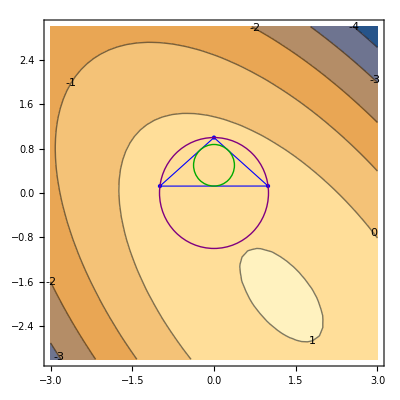

```mathematica
Module[{d=.5,cd,trils,print=False,prints=0,weaver},
cd=chappleData[d,180.01];
ContourPlot[
trils=getTrilinears[{x,y},cd["tri"],cd["triL"]];
weaver=weaverCircle2[trils,cd["R"],cd["r"],d];
If[print&&prints++<10,Print["trils=",trils,", weaver=",weaver]];
weaver,{x,-3,3},{y,-3,3},ContourLabels->All,Axes->True,Epilog->{FaceForm@None,drawPoly[cd["tri"],Blue],Thick,Darker@Green,Circle[cd["inc"],cd["r"]],Purple,Circle[cd["cir"],cd["R"]]}]]
```

```mathematica
Clear@getHypsLow;
Options@getHypsLow={addHeader->False};
getHypsLow[tri_,triL_,OptionsPattern[]]:=Module[{exc,excL,hyps,as,bs,cs,ds,tDegs,names,dets,discr,header,mas,ns,vals},
exc=excentralTriangle[tri,triL];
excL=triLengthsRL@exc;
names={"F","J","F_exc","J_exc"};
hyps={
getFeuerbachHyp[tri,triL],
getJerabekHyp[tri,triL],
getFeuerbachHyp[exc,excL],
getJerabekHyp[exc,excL]};
as=#["a"]&/@hyps;
bs=#["b"]&/@hyps;
cs=#["c"]&/@hyps;
dets=#["det"]&/@hyps;
discr=#["discr"]&/@hyps;
mas=#["majorAxis"]&/@hyps;
ns=magn/@mas;
ds=ConstantArray["n/a",Length@hyps];
tDegs=ConstantArray["n/a",Length@hyps];
header={"d","tDeg","name","a","b","c","det","discr","majorAxis","norm"};
vals=Transpose@{ds,tDegs,names,as,bs,cs,dets,discr,mas,ns};
If[OptionValue@addHeader,Prepend[vals,header],vals]];
```

```mathematica
Clear@getChappleHyps;
Options@getChappleHyps={addHeader->False};
getChappleHyps[d_,tDeg_,OptionsPattern[]]:=Module[{cd,hyps,as,bs,cs,ds,tDegs,names,dets,discr,header,mas,ns,vals},
cd=chappleData[d,tDeg];
names={"F","J","F_exc","J_exc"};
hyps={
getFeuerbachHyp[cd["tri"],cd["triL"]],
getJerabekHyp[cd["tri"],cd["triL"]],
getFeuerbachHyp[cd["exc"],cd["excL"]],
getJerabekHyp[cd["exc"],cd["excL"]]};
as=#["a"]&/@hyps;
bs=#["b"]&/@hyps;
cs=#["c"]&/@hyps;
dets=#["det"]&/@hyps;
discr=#["discr"]&/@hyps;
mas=#["majorAxis"]&/@hyps;
ns=magn/@mas;
ds=ConstantArray[d,Length@hyps];
tDegs=ConstantArray[tDeg,Length@hyps];
header={"d","tDeg","name","a","b","c","det","discr","majorAxis","norm"};
vals=Transpose@{ds,tDegs,names,as,bs,cs,dets,discr,mas,ns};
If[OptionValue@addHeader,Prepend[vals,header],vals]];
```

```mathematica
getExtrYLine[vs_]:=Module[{ys,top,bot},
ys=Second/@vs;
bot=First[Ordering[ys,1]];
top=First[Ordering[ys,-1]];
Part[vs,{bot,top}]];
```

```mathematica
Clear@lineLength;lineLength[{p_,q_}]:=magn[p-q];
```

```mathematica
Clear@annotateAxesLow;
Options@annotateAxesLow={plIncAreas->False,pre->""};
annotateAxesLow[symbol1_,symbol2_,subscr_,cd_,var_,OptionsPattern[]]:=Module[{s1,sp1,s2,sp2},
s1=ToString[Subscript[symbol1,subscr],StandardForm];
sp1=s1<>"'";(*ToString[Subscript[symbol1<>"'",subscr],StandardForm];*)
s2=ToString[Subscript[symbol2,subscr],StandardForm];
sp2=s2<>"'";(*ToString[Subscript[symbol2<>"'",subscr],StandardForm];*)
"\n"<>If[OptionValue@pre≠"",OptionValue@pre<>": ",""]<>s1<>"="<>nfn[cd[var]["lengths"][[2]],3]<>", "<>s2<>"="<>nfn[cd[var]["lengths"][[1]],3]<>", "<>s1<>s2<>"="<>nfn[Apply[Times,cd[var]["lengths"]],3]<>", "<>s1<>"/"<>s2<>"="<>nfn[1/cd[var]["ratio"],3]<>If[OptionValue@plIncAreas,", "<>ToString[Subscript["A",subscr],StandardForm]<>"="<>nfn[signedArea[cd[var]["orbit"]],3]<>", "<>ToString[Subscript["A",subscr],StandardForm]<>"="<>nfn[triPer[cd[var]["orbit"]],3],""]];
```

```mathematica
Clear@annotateAxes;
Options@annotateAxes={drCircumX1->False,drCircumX10->False,drExcIncX3->False,drExcIncX5->False,drExcCaustic->False,drExcCircumX5->False,drExcCircumX6->False,drCB->False,plShort->False,plAreas->False};
annotateAxes[cd_,OptionsPattern[]]:=Module[{n3,n5,e5exc,e6exc,e1,e10,a9b9},
a9b9=annotateAxesLow["a","b",9,cd,"cb",pre->"E_9"];
n3=annotateAxesLow["α'","β'",3,cd,"excIncX3",pre->"I_3'"];
n5=annotateAxesLow["α'","β'",5,cd,"excIncX5",pre->"I_5'"];
e5exc=annotateAxesLow["η'","ζ'",5,cd,"excCircumX5",pre->"E_5'"];
e6exc=annotateAxesLow["η'","ζ'",6,cd,"excCircumX6",pre->"E_6'"];
e1=annotateAxesLow["η","ζ",1,cd,"circumX1",pre->"E_1"];
e10=annotateAxesLow["η","ζ",10,cd,"circumX10",pre->"E_10"];
"d="<>nfn[cd["d"],4]<>", R=1, r="<>nfn[cd["r"],4]<>", R/r="<>nfn[1/cd["r"],3]<>", θ="<>nfn[cd["tDeg"],1]<>"°"<>If[OptionValue@plAreas,
"\nA="<>nfn[cd["A"],3]<>", A_exc="<>nfn[cd["Aexc"],3]<>", A.A_exc="<>nfn[cd["A"]cd["Aexc"],3]<>", A_exc/A="<>nfn[cd["Aexc"]/cd["A"],3],""]<>
If[OptionValue@plShort,"",
If[OptionValue@drCB,a9b9,""]<>
If[OptionValue@drCircumX1,e1,""]<>
If[OptionValue@drCircumX10,e10,""]<>
If[OptionValue@drExcIncX3,n3,""]<>
If[OptionValue@drExcIncX5||OptionValue@drExcCaustic,n5,""]<>
If[OptionValue@drExcCircumX5,e5exc,""]<>
If[OptionValue@drExcCircumX6,e6exc,""]]];
```

```mathematica
annotateAxes[chappleData[.7,10.],drCircumX1->True,plShort->False,plAreas->False]
```

d=0.7000, R=1, r=0.2550, R/r=3.922, θ=10.0°
E_1: "\[Eta]"_1=1.700, "\[Zeta]"_1=0.300, "\[Eta]"_1"\[Zeta]"_1=0.510, "\[Eta]"_1/"\[Zeta]"_1=5.667

```mathematica
Clear@showChapple;
Options@showChapple={fnt->16,minX->-1,maxX->1,minY->-2,maxY->2,drExc->True,drMed->False,drAct->False,drExcCircle->False,drExcCaustic->False,drExcCausticAxes->False,excCausticClr->Directive[Thick,Darker@Green,Dashed],drTangential->False,drExcMed->False,drAntiorthic->False,drAntiorthicConstr->False,drWeaverCirc->False,drNpcHex->False,drJerabek->False,drExcJerabek->False,drFeuerbach->False,drExcFeuerbach->False,rotHypSinCos->False,drMitten->False,drCB->False,drCBFocusLocus->False,drExcIncX3->False,drExcCircumX5->False,drExcIncX5->False,plShort->False,drSimson->False,plIncAreas->False,drCircumX1->False,drEqualPowerInc->False,drEqualPowerCir->False,plAreas->True,drX100->True,drX11->False,drL31->False,drOrthicAxis->False,drL663->False,axisLgt->100,drCircumX10->False,drExcCircumX6->False,drExcCircumX6FocusLocus->False};
showChapple[d_,tDeg_,opts:OptionsPattern[]]:=Module[{cd,pl,plHyps,plHypsJoined,pr,gr,R=1,J,Jexc,F,Fexc,drHyps,excCausticA,excCausticB,excCaustic,simson,llpor,llexcmed,dl},
cd=chappleData[d,tDeg,doTangential->OptionValue@drTangential,odehnalVertices->True];
pl=annotateAxes[cd,FilterRules[{opts},Options@annotateAxes]];
pr={{OptionValue@minX,OptionValue@maxX},{OptionValue@minY,OptionValue@maxY}};
{F,J,Fexc,Jexc}={
getFeuerbachHyp[cd["tri"],cd["triL"]],
getJerabekHyp[cd["tri"],cd["triL"]],
getFeuerbachHyp[cd["exc"],cd["excL"]],
getJerabekHyp[cd["exc"],cd["excL"]]};
drHyps=
{If[OptionValue@drFeuerbach,drawHyp5b[F,showFoci->True,psAxes->Directive[Dashed,Black],ps->Directive[AbsoluteThickness@3,Lighter@Blue]],{}],
If[OptionValue@drJerabek,{drawHyp5b[J,showFoci->True,psAxes->Directive[Dashed,Black],ps->Directive[Dashed,Thick,Blue]](*,Graphics[{Pink,Thick,Circle[cd["x5"],cd["npcRad"]]}]*)},{}],
(*Print[getJerabekHyp[cd["tri"],cd["triL"]]];*)
If[OptionValue@drExcFeuerbach,drawHyp5b[Fexc,showFoci->True,psAxes->Directive[Dashed,Black],ps->Directive[Dashed,Thick,Darker@Green]],{}],
If[OptionValue@drExcJerabek,drawHyp5b[Jexc,showFoci->True,psAxes->Directive[Dashed,Black],ps->Directive[AbsoluteThickness@3,Lighter@Green]],{}]
};
plHyps=DeleteCases[
{If[OptionValue@drFeuerbach,"F(a,b,c)={"<>nfn[F["a"],2]<>", "<>nfn[F["b"],2]<>", "<>nfn[F["c"],2]<>"}, cs="<>ToString@Chop[F["coeffs"]],""],
If[OptionValue@drExcFeuerbach,"F'(a,b,c)={"<>nfn[Fexc["a"],2]<>", "<>nfn[Fexc["b"],2]<>", "<>nfn[Fexc["c"],2]<>"}",""],
If[OptionValue@drJerabek,"J(a,b,c)={"<>nfn[J["a"],2]<>", "<>nfn[J["b"],2]<>", "<>nfn[J["c"],2]<>"}",""],
If[OptionValue@drExcJerabek,"J'(a,b,c)={"<>nfn[Jexc["a"],2]<>", "<>nfn[Jexc["b"],2]<>", "<>nfn[Jexc["c"],2]<>"}, cs="<>ToString@Chop[Jexc["coeffs"]],""],
If[OptionValue@drExcJerabek&&OptionValue@drFeuerbach,"λ'/λ="<>nfn[Jexc["c"]/F["c"],3]<>", √(2  R/r)="<>nfn[Sqrt[2R/cd["r"]],3],""]},""];
plHypsJoined=If[Length@plHyps==0,"",StringJoin@Most@Riffle[plHyps,ConstantArray["\n",Length@plHyps]]];
gr=Graphics[{PointSize@Large,Thick,FaceForm@None,
If[OptionValue@drL31,dl=OptionValue@axisLgt norm[cd["l31"][[1]]-cd["l31"][[2]]];{Darker@Green,Line@{cd["l31"][[2]]-dl,cd["l31"][[1]]+dl}},{}],
If[OptionValue@drL663,dl=OptionValue@axisLgt norm[cd["l663"][[1]]-cd["l663"][[2]]];{Brown,Line@{cd["l663"][[2]]-dl,cd["l663"][[1]]+dl},Point@cd["x57"],Text[Style["X_57",OptionValue@fnt],cd["x57"],{-1.25,0}]},{}],
If[OptionValue@drOrthicAxis,dl=OptionValue@axisLgt norm[cd["orthicAxis"][[1]]-cd["orthicAxis"][[2]]];{Orange,Line@{cd["orthicAxis"][[2]]-dl,cd["orthicAxis"][[1]]+dl}},{}],
If[OptionValue@drExcCircle,{Orange,Circle[-cd["inc"],2R]},{}],
{Darker@Green,Circle[cd["inc"],cd["r"]]},
{Purple,Circle[cd["cir"],cd["R"]]},
If[OptionValue@drExc,{drawPolyThick[cd["exc"],Darker@Green]},{}],
If[OptionValue@drMed,{drawPoly[cd["med"],Darker@Red]},{}],
If[OptionValue@drAct,{drawPoly[cd["act"],Directive[Dashed,Blue]]},{}],
If[OptionValue@drExcIncX3||OptionValue@drExcCaustic||OptionValue@drExcCircle,
{Orange,Point@cd["x40"],Text[Style["X_40",OptionValue@fnt],cd["x40"],{-1.25,-1.25}]},{}],
drawPolyThick[cd["tri"],Blue],
If[OptionValue@drSimson,{Thick,Blue,Dashed,Line[getExtrYLine@cd["pedalX100"]],Point@cd["pedalX100"](*,{Dashed,Line@{cd["x100"],#}&/@cd["pedalX100"]}*),Pink,Line[getExtrYLine@cd["excMedPedalX100"]],Point@cd["excMedPedalX100"](*,{Dashed,Line@{cd["x100"],#}&/@cd["excMedPedalX100"]}*)},{}],
If[OptionValue@drExcCaustic,
excCausticA=R;(*Abs@chappleData[d,.001]["exc"][[2,2]];*)
excCausticB=Sqrt[excCausticA^2-d^2];
{OptionValue@excCausticClr,Circle[{0,0},{excCausticB,excCausticA}],Point@cd["excCausticTouchPts"],If[OptionValue@drExcCausticAxes,{Dashed,Line@{{-excCausticB,0},{excCausticB,0}},Line@{{0,-excCausticA},{0,excCausticA}}},{}]},{}],
If[OptionValue@drExcMed,drawPoly[cd["excMed"],Directive[Thick,Pink]],{}],
If[OptionValue@drTangential,drawPoly[cd["tangential"],Directive[Purple,Dashed]],{}],
If[OptionValue@drAntiorthic,
{Blue,Line@{{OptionValue@minX,cd["aoa"][[1,2]]},{OptionValue@maxX,cd["aoa"][[1,2]]}}},{}],
If[OptionValue@drAntiorthicConstr,{
{Dashed,Darker@Green,MapThread[Line@{#1,#2}&,{cd["exc"],cd["aoa"]}]},
{Blue,Dashed,Point@cd["aoa"],MapThread[Text[Style[Subscript["Q",#2],OptionValue@fnt],#1,{0,-1.5}]&,{cd["aoa"],{1,2,3}}],MapThread[Line@{#1,#2}&,{cd["tri"],cd["aoa"]}]}
},{}],
If[OptionValue@drWeaverCirc,{
{Red,Point@cd["weaverCtr"],Circle[cd["weaverCtr"],cd["weaverR"]],Text[Style["C",OptionValue@fnt],cd["weaverCtr"],{-1.25,-1.25}],
MapThread[Text[Style[Subscript["T'",#2],OptionValue@fnt],#1,{-#3 1.25,-1.25}]&,{cd["tangsWeaver"],{1,2},{-1,1}}],
Point@cd["tangsWeaver"],Line@{cd["x1155"],#}&/@cd["tangsWeaver"],Dashed,Line@cd["tangsWeaver"]}(*,
{Darker@Green,Point@cd["tangsInc"],Line@{cd["x1155"],#}&/@cd["tangsInc"]}*),
(*{Purple,Point@cd["tangsCir"],Line@{cd["x1155"],#}&/@cd["tangsCir"],
MapThread[Text[Style[Subscript["T",#2],OptionValue@fnt],#1,{-#3 2,1}]&,{cd["tangsCir"],{1,2},{-1,1}}],
Dashed,Circle[cd["x1155"],magn[cd["x1155"]-cd["tangsCir"][[1]]]]}*)

},{}],
(*{Red,Point@cd["tangsEqualPowerCir"],Line@{cd["x1155"],#}&/@cd["tangsEqualPowerCir"],Circle@@cd["equalPowerCir"],Point[cd["equalPowerCir"][[1]]]}}*)
If[OptionValue@drEqualPowerInc,{
(* draw tangs to incirc and circle through them *)
{Darker@Green,Line@{cd["x1155"],#}&/@cd["tangsInc"],Point@cd["tangsInc"],Text[Style["C",OptionValue@fnt],cd["weaverCtr"],{-1.25,-1.25}],
Dashed,Circle[cd["x1155"],magn[cd["x1155"]-cd["tangsInc"][[1]]]],
MapThread[Text[Style[Subscript["T",#2],OptionValue@fnt],#1,{-#3 1.25,-1.25}]&,{cd["tangsInc"],{1,2},{-1,1}}]},
(* draw equal power circ and *)
{Darker@Green,Circle[{0,-R},cd["powerIncExplicit"]]},
{Darker@Green,Point[cd["equalPowerInc"][[1]]],(*Circle@@cd["equalPowerInc" ],*)Point@cd["tangsEqualPowerInc"],Line@{cd["x1155"],#}&/@cd["tangsEqualPowerInc"],
MapThread[Text[Style[Subscript["T\"",#2],OptionValue@fnt],#1,{-#3 2,-.5}]&,{cd["tangsEqualPowerInc"],{1,2},{-1,1}}]}},{}],
If[OptionValue@drEqualPowerCir,{
{Purple,Point@cd["tangsCir"],Line@{cd["x1155"],#}&/@cd["tangsCir"],
MapThread[Text[Style[Subscript["T",#2],OptionValue@fnt],#1,{-#3 2,1}]&,{cd["tangsCir"],{1,2},{-1,1}}],
(* --- *)
Dashed,Circle[cd["x1155"],magn[cd["x1155"]-cd["tangsCir"][[1]]]]},
{Orange,Point@cd["tangsExcCir"],Line@{cd["x1155"],#}&/@cd["tangsExcCir"],MapThread[Text[Style[Subscript["T'",#2],OptionValue@fnt],#1,{0,-2}]&,{cd["tangsExcCir"],{1,2},{-1,1}}]},
{Red,Point@cd["tangsEqualPowerCir"],Line@{cd["x1155"],#}&/@cd["tangsEqualPowerCir"],Circle@@cd["equalPowerCir"],Point[cd["equalPowerCir"][[1]]],Text[Style["C",OptionValue@fnt],cd["weaverCtr"],{-1.25,-1.25}],(*Dashed,Line@cd["tangsEqualPowerCir"]*)
MapThread[Text[Style[Subscript["T\"",#2],OptionValue@fnt],#1,{0,-2}]&,{cd["tangsEqualPowerCir"],{1,2},{-1,1}}]}},{}],
If[OptionValue@drNpcHex,{drawPoly[cd["npcHex"],Red],FaceForm@{Opacity@.1,Red},drawPoly[cd["npcHexHull"],Red]},{}],
If[OptionValue@drMitten,{Darker@Red,Point@cd["x9"],Circle[cd["x9ctr"],cd["x9rad"]]},{}],
MapThread[{#3,Point@#1,Text[Style[Subscript["X",#2],OptionValue@fnt],#1,{-1.25,-1.25}]}&,
Transpose@{
{cd["inc"],1,Darker@Green},
{{0,0},3,Purple}
(*{cd["x100"],100,Black}*)(*,
{cd["excMedInc"],-1,Pink}*)}],
If[OptionValue@drX100,{Black,Point@cd["x100"],Text[Style["X_100",OptionValue@fnt],cd["x100"],{-1.25,-1.25}]},{}],
If[OptionValue@drX11,{Black,Point@cd["x11"],Text[Style["X_11",OptionValue@fnt],cd["x11"],{-1.25,-1.25}]},{}],
If[OptionValue@drAntiorthic,{Blue,Point@cd["x1155"],Text[Style["X_1155",OptionValue@fnt],cd["x1155"],{-1.25,-1.25}]},{}],
If[OptionValue@drCB&&OptionValue@drCBFocusLocus,{Darker@Cyan,
Circle[cd["cbFocusLocusCtr"],cd["cbFocusLocusRad"]],
Point@cd["cbFocusLocusCtr"]},{}],
If[OptionValue@drExcCircumX6&&OptionValue@drExcCircumX6FocusLocus,Module[{ctr},
ctr=cd["x9ctr"];
{Darker@Cyan,
Circle[ctr,magn[ctr-cd["excCircumX6"]["foci"][[1]]]],
Point@ctr}],{}]}];
Show[{gr,drHyps,If[OptionValue@drCB,
drawCircumAnyLow[cd["cb"],cd["tri"],drAxes->Not[OptionValue@drExcCircumX6],drFoci->True,ctrLab->Style["X_9",OptionValue@fnt],labClr->If[OptionValue@drMitten,Darker@Red,Black],ps->Directive[Thick,Black]],{}],
If[OptionValue@drCircumX1,
drawCircumAnyLow[cd["circumX1"],cd["tri"],ctrLab->""(*Style["X_40",OptionValue@fnt]*),labClr->Darker@Green,ps->Directive[Thick,Darker@Green],drFoci->True],{}],
If[OptionValue@drCircumX10,
drawCircumAnyLow[cd["circumX10"],cd["tri"],ctrLab->Style["X_10",OptionValue@fnt],labClr->Pink,ps->Directive[Thick,Pink],drFoci->True],{}],
If[OptionValue@drExcCircumX5,
drawCircumAnyLow[cd["excCircumX5"],cd["exc"],ctrLab->""(*Style["X_40",OptionValue@fnt]*),labClr->Darker@Cyan,ps->Directive[Thick,Darker@Cyan],drFoci->True],{}],
If[OptionValue@drExcCircumX6,
drawCircumAnyLow[cd["excCircumX6"],cd["exc"],ctrLab->""(*"X_9"*),labClr->ColorData["HTML","OliveDrab"],ps->Directive[Thick,ColorData["HTML","OliveDrab"]],drFoci->True],{}],
If[OptionValue@drExcIncX3,
{drawCircumAnyLow[cd["excIncX3"],cd["tri"],ctrLab->""(*Style["X_40",OptionValue@fnt]*),labClr->Darker@Red,ps->Directive[Thick,Darker@Red],drFoci->True],
Graphics[{Directive[Thick,Darker@Red],PointSize@Medium,Point[cd["excIncX3"]["orbit"]]}]},{}],
If[OptionValue@drExcIncX5,
{drawCircumAnyLow[cd["excIncX5"],cd["tri"],ctrLab->Style["X_3",OptionValue@fnt],ps->Directive[Thick,Darker@Red],drFoci->True],Graphics[{Directive[Thick,Darker@Red],PointSize@Medium,Point[cd["excIncX5"]["orbit"]]}]},{}]
},Frame->True,Axes->True,PlotLabel->Style[pl<>"\n"<>plHypsJoined,{Black,OptionValue@fnt}],PlotRange->pr]];
```

```mathematica
robtuse= Sqrt[2] - 1;N[robtuse]
```

0.414214

```mathematica
DynamicModule[{R=1,d,excLocus,eps=.01,locusExcIncX3},
Manipulate[
(*excLocus=Quiet@ParametricPlot[chappleData[d,tDeg2+eps]["exc"][[1]],{tDeg2,0,360},PlotStyle->{Thick,Orange}];*)
d=dsolChapple[r];
Dynamic@Show[showChapple[d,tDeg+eps,minX->-xlim,maxX->xlim,minY->-ylim,maxY->ylim,drExc->drExc0,drMed->drMed0,drAct->drAct0,drExcCircle->drExcCircle0,(*drExcCausticAxes->drExcCaustic0,*)drExcCaustic->drExcCaustic0,drTangential->drTangential0,drExcMed->drExcMed0,drWeaverCirc->drWeaverCirc0,drNpcHex->drNpcHex0,drExcFeuerbach->drExcFeuerbach0,drFeuerbach->drFeuerbach0,drExcJerabek->drExcJerabek0,drJerabek->drJerabek0,drAntiorthic->drAntiorthic0,drAntiorthicConstr->drAntiorthicConstr0,drMitten->drMitten0,drCB->drCB0,drCBFocusLocus->drCB0,drExcIncX3->drExcIncX30,drExcIncX5->drExcIncX50,drSimson->drSimson0,drCircumX1->drCircumX1a,drEqualPowerCir->drEqualPowerCir0,drEqualPowerInc->drEqualPowerInc0,drX100->drX100a,drX11->drX11a,drL31->drL31a,drOrthicAxis->drL3a,drL663->drL663a,drExcCircumX5->drExcCircumX5a,drExcCircumX6->drExcCircumX6a,(*drExcCircumX6FocusLocus->drExcCircumX6a,*)drCircumX10->drCircumX10a],ImageSize->600,PlotRangeClipping->True],
Style["Poristic Triangles and the Circumbilliard:",{Darker@Red,16}],
Style["Conics, Inconics, and Invariants",{Darker@Red,16}],
Style["D. Reznik & R. Garcia, April, 2020",{Blue,12}],
Delimiter,
{{r,rOvR[1.5]},0.01,.49,.01,Appearance->"Labeled"},
{{tDeg,20.},-360,360,.1,Appearance->"Labeled"},
Row[{
Control[{{xlim,3},{1,2,3,4,8}}],
"    ",
Control[{{ylim,3},{1,2,3,4,8}}]}],
Grid[(makeCtrlCol/@{
{"basic",
Control[{{drExc0,True,"exc"},{True,False}}],
Control[{{drMed0,False,"medial"},{True,False}}],
Control[{{drAct0,False,"act"},{True,False}}],
Control[{{drTangential0,False,"tangential"},{True,False}}]},
{"excentral",
Control[{{drExcCircle0,True,"exc locus"},{True,False}}],
Control[{{drExcCaustic0,False,"exc caustic"},{True,False}}],
Control[{{drExcMed0,False,"exc. medial"},{True,False}}],
Control[{{drNpcHex0,False,"9-pt hex"},{True,False}}]},
{"axes",
Control[{{drAntiorthic0,False,"antiorthic L_1"},{True,False}}],
Control[{{drAntiorthicConstr0,False,"antiorthic constr."},{True,False}}],
Control[{{drL31a,False,"L_31"},{True,False}}],
Control[{{drL3a,False,"orthic axis L_3"},{True,False}}],
Control[{{drL663a,False,"X_2X_9 axis L_663"},{True,False}}]},
{"circumconics",
Control[{{drCircumX1a,False,"circum X_1"},{True,False}}],
Control[{{drCircumX10a,False,"circum X_10"},{True,False}}],
Control[{{drExcCircumX6a,False,"exc circum X_6"},{True,False}}],
Control[{{drExcCircumX5a,False,"exc circum X_5"},{True,False}}]},
{"inconics",
Control[{{drExcIncX30,False,"exc incon X_3"},{True,False}}],
Control[{{drExcIncX50,False,"exc incon X_5"},{True,False}}]},
{"hyps",
Control[{{drFeuerbach0,False,"feuerbach"},{True,False}}],
Control[{{drExcJerabek0,False,"exc. jerabek"},{True,False}}],
Control[{{drJerabek0,False,"jerabek"},{True,False}}],
Control[{{drExcFeuerbach0,False,"exc. feuerbach"},{True,False}}]},
{"CB",
Control[{{drCB0,False,"cb"},{True,False}}],
Control[{{drMitten0,False,"x9 locus"},{True,False}}]},
{"weaver",
Control[{{drWeaverCirc0,False,"weaver circle"},{True,False}}],
Control[{{drEqualPowerInc0,False,"eq. pwr incircle"},{True,False}}],
Control[{{drEqualPowerCir0,False,"eq. pwr circum"},{True,False}}]},
{"misc",
Control[{{drX11a,False,"X_11"},{True,False}}],
Control[{{drX100a,False,"X_100"},{True,False}}],
Control[{{drSimson0,False,"pedals X_100"},{True,False}}]}
})//Partition[#,3]&,Spacings->{1,1},Alignment->Right,Frame->All,FrameStyle->Lighter@Gray],
ControlPlacement->Left]]
```

```mathematica
oneFrameHyps[d_,tDeg_]:=Show[showChapple[d,tDeg,minX->-2,maxX->2,minY->-2,maxY->2,drExc->True,drFeuerbach->True,drExcJerabek->True,drCB->True,drX100->True,drX11->True],ImageSize->800,PlotRangeClipping->True]
```

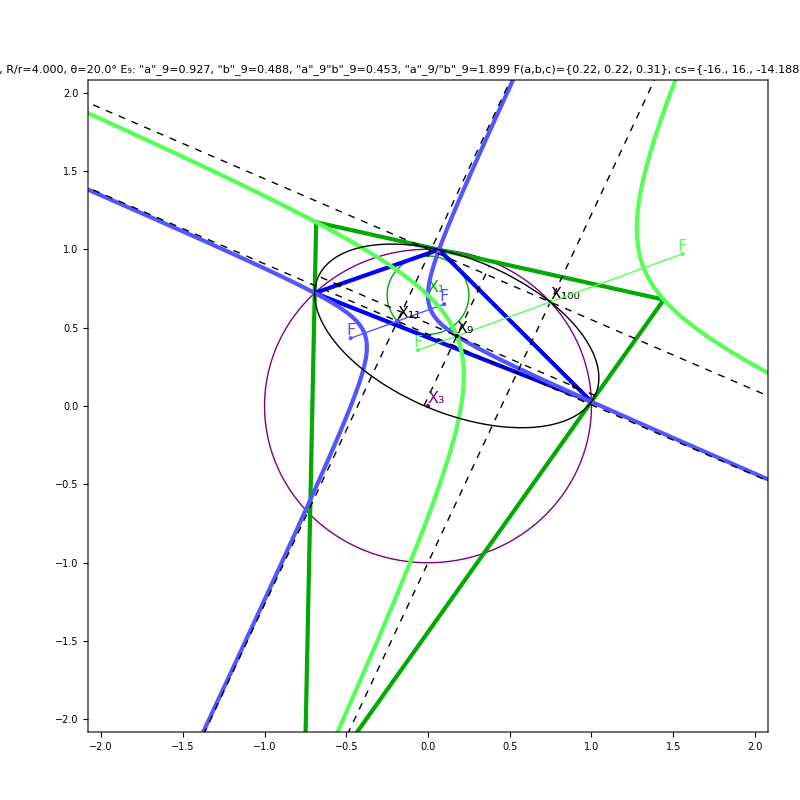

```mathematica
oneFrameHyps[dsolChapple[.25],20.]
```

## Chapple Odehnal Vertices & Ronaldo’s Excentral Sides

```mathematica
excentralSides[R_,r_,t_,x_,y_]:=Module[{d,w,ct,st,l1,l2,l3,d0,d1},
d=Sqrt[R(R-2r)];
ct=Cos@t;
st=Sin@t;
w=Sqrt[R^2-(d ct+r)^2];
d0=(d ct+r);
d1=(d ct-r);
l1=((d st-w)st-r ct)x-(d0 st-w ct)y+R^2-d^2;
l2=((d st+w)st-r ct)x-(d0 st+w ct)y+R^2-d^2;
l3=(R ct-d)x+R st y-2 d R ct+R^2+d^2;
{l1,l2,l3}];
```

```mathematica
rOvR[1.5]
```

0.36266

```mathematica
excentralSides[1,rOvR[1.5],toRad[10.],.1,.1]
```

{0.714633,0.637216,0.305841}

```mathematica
Clear@drawChappleOdehnal;
Options@drawChappleOdehnal={axisLgt->.25,drIntouch->False,drExtouch->False,ln->-1,xmin->-2,xmax->2.5,ymin->-2.25,ymax->2.25,digs->3,lgt->.2};drawChappleOdehnal[R_,r_,tDeg_,OptionsPattern[]]:=Module[{d,t,tang1,pr,vs,x1,x3,x40,int,ext,exc,cp,gr,pl},
d=Sqrt[R(R-2r)];
t=toRad@tDeg;
tang1={r Cos@t+2d,r Sin@t};
vs=poristicVertices[R,r,t];
x1={2d,0};
x3={d,0};
x40={0,0};
int=intouchTriangle[vs,triLengthsRL@vs];
ext=extouchTriangle[vs,triLengthsRL@vs];
exc=excentralTriangle[vs,triLengthsRL@vs];
pr={{OptionValue@xmin,OptionValue@xmax},{OptionValue@ymin,OptionValue@ymax}};
pl="R="<>nfn[R,1]<>", r="<>nfn[r,OptionValue@digs]<>", d="<>nfn[getEulerOI[R,r],OptionValue@digs]<>
If[OptionValue@drIntouch||OptionValue@drExtouch,", A="<>nfn[Abs@signedArea[vs],OptionValue@digs]<>"\nA/A\"=2R/r="<>nfn[2R/r,OptionValue@digs],""]<>
If[OptionValue@drIntouch,", A_int="<>nfn[Abs@signedArea[int],OptionValue@digs]<>", A/A_int="<>nfn[signedArea[vs]/signedArea[int],OptionValue@digs],""]<>
If[OptionValue@drExtouch,", A_ext="<>nfn[Abs@signedArea[ext],OptionValue@digs],""];
cp=If[OptionValue@ln>0,ContourPlot[excentralSides[R,r,t,x,y][[OptionValue@ln]]==0,{x,OptionValue@xmin,OptionValue@xmax},{y,OptionValue@ymin,OptionValue@ymax},ContourStyle->Darker@Green],{}];
gr=Graphics[{FaceForm@None,Arrowheads@Medium,PointSize@Large,Thick,
{Darker@Green,Circle[x1,r]},
{Purple,Circle[x3,R]},
{Black,Arrow@{x40,x40+{OptionValue@axisLgt,0}},Arrow@{x40,x40+{0,OptionValue@axisLgt}}},
{drawPoly[vs,Blue],Blue,Point@tang1,Text[Style["C(t)",16],tang1+OptionValue@lgt norm[tang1-x1]],MapThread[Text[Style[Subscript["P",#2],16],#1+OptionValue@lgt norm[#1-x1]]&,{vs,{1,2,3}}]},
{drawPoly[exc,If[OptionValue@ln<1,Darker@Green,Directive[Dashed,Darker@Green]]],Darker@Green,Point@exc,MapThread[Text[Style[Subscript["P'",#2],16],#1+OptionValue@lgt norm[#1-x40]]&,{exc,{1,2,3}}]},
MapThread[{#3,Point@#1,Text[Style[ToString[Subscript["X",#2],StandardForm],16],#1,{-.5,1.5}]}&,{{x1,x3,x40},{1,3,40},{Darker@Green,Purple,Orange}}],
If[OptionValue@drIntouch,{drawPoly[int,Directive[Dashed,Darker@Green]]},{}],
If[OptionValue@drExtouch,{drawPoly[ext,Directive[Dashed,Brown]]},{}]
}];
Show[{gr,cp},PlotLabel->Style[pl,{Black,16}],PlotRange->pr,ImageSize->Large]];
```

```mathematica
DynamicModule[{gr,R=1,r=rOvR[1.5],d,t},
Manipulate[
drawChappleOdehnal[R,r,tDeg,drIntouch->drIntouch0,drExtouch->drExtouch0,ln->ln0,lgt->.15,digs->4],
{{tDeg,10.},-180,180},
{{ln0,0,"exc side"},{0,1,2,3}},
{{drIntouch0,False,"intouch"},{True,False}},
{{drExtouch0,False,"extouch"},{True,False}},SaveDefinitions->True,ControlPlacement->Left]]
```

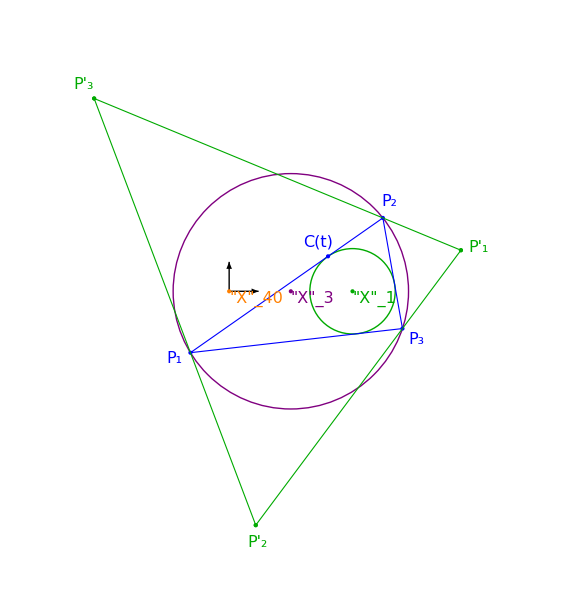

```mathematica
odehnalCoordinatesPlot=Show[drawChappleOdehnal[1,rOvR[1.5],125.,ln->0,lgt->.15,digs->4,xmin->-1.5,ymax->2],PlotLabel->None]
```

```mathematica
export3["0130_odehnal_axes",odehnalCoordinatesPlot]
```

## Chapple Envelope and Figures

```mathematica
Clear@getEnvelopeChappleLow;(* via intersection *)
Options@getEnvelopeChappleLow={epsDeg->.001};
getEnvelopeChappleLow[d_?NumericQ,tDeg_?NumericQ,obj_,OptionsPattern[]]:=Module[{la,lb,args},
la=chappleData[d,tDeg-.5OptionValue@epsDeg][obj];
lb=chappleData[d,tDeg+.5OptionValue@epsDeg][obj];
args={la[[1]],la[[2]]-la[[1]],lb[[1]],lb[[2]]-lb[[1]]};
(*Print@args;*)
interRaysUnprot@@args];
```

```mathematica
dsolChapple[rOvR[1.5]]
```

0.5241

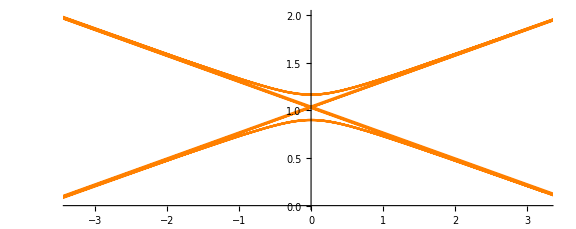

```mathematica
Module[{d=dsolChapple[rOvR[1.5]]},
ParametricPlot[getEnvelopeChappleLow[d,tDeg,"orthicAxis"],{tDeg,0,360},PerformanceGoal->"Speed",PlotStyle->Orange,ImageSize->Large]]
```

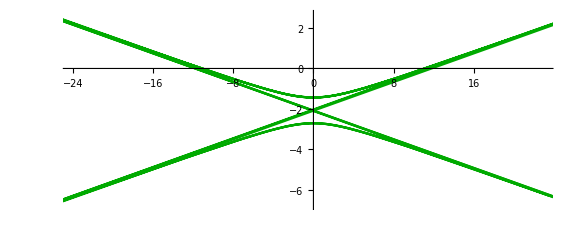

```mathematica
Module[{d=dsolChapple[rOvR[1.5]]},
ParametricPlot[getEnvelopeChappleLow[d,tDeg,"l31"],{tDeg,0,360},PerformanceGoal->"Speed",PlotStyle->Darker@Green,ImageSize->Large]]
```

```mathematica
Clear@getEnvelopeExcChapple;(* via intersection *)
Options@getEnvelopeExcChapple={epsDeg->.001};
getEnvelopeExcChapple[d_?NumericQ,tDeg_?NumericQ,OptionsPattern[]]:=Module[{exc1,exc2,args},
exc1=chappleData[d,tDeg-.5OptionValue@epsDeg]["exc"];
exc2=chappleData[d,tDeg+.5OptionValue@epsDeg]["exc"];
args={exc1[[1]],exc1[[2]]-exc1[[1]],exc2[[1]],exc2[[2]]-exc2[[1]]};
(*Print@args;*)
interRaysUnprot@@args];
```

```mathematica
getEnvelopeExcChapple[.61,20.]
```

{-0.634797,0.598523}

#### Looks like envelope of Excentral is Upright ellipse with foci on X1 and X40 of the reference (x4 and x3 of excentral), i.e., c = d

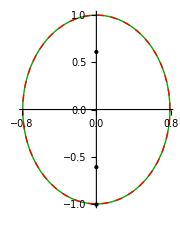

```mathematica
Module[{d=.61,pp,a,exc,x3,x4,excL,b,gr,eps=.001},
exc=chappleData[d,eps]["exc"];
excL=triLengthsRL@exc;
x4=getOrthocenterTrilin[exc,excL];
x3=getCircumcenterTrilin[exc,excL];
a=Abs@exc[[2,2]];
(* c^2 = a^2-b^2 => assume c = d => b^2 = a^2-d^2 *) 
b=Sqrt[a^2-d^2];
gr=Graphics[{PointSize@Large,Point@{0,-a},Thick,Dashed,Red,Circle[{0,0},{b,a}],Black,Point@{x4,x3}}];
pp=ParametricPlot[getEnvelopeExcChapple[d,tDeg],{tDeg,0,360},PlotStyle->Directive[Thick,Darker@Green],PerformanceGoal->"Speed"];
Show[{pp,gr},ImageSize->Small]]
```

```mathematica
chappleData[.61,0.001]["exc"]
```

{{-8.45563×10^-6,1.39},{-1.9616,-1.00002},{1.96161,-0.999979}}

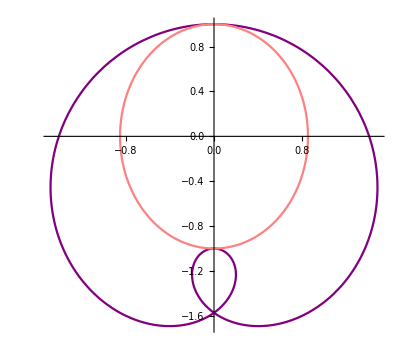

```mathematica
Module[{r=.3625,d,p3,p5},
d=dsolChapple[r];
p3=Quiet@ParametricPlot[chappleData[d,tDeg+.001]["excIncX3"]["orbit"][[1]],{tDeg,0,360},PlotStyle->Purple];
p5=Quiet@ParametricPlot[chappleData[d,tDeg+.001]["excIncX5"]["orbit"][[1]],{tDeg,0,360},PlotStyle->Pink];
Show[{p3,p5},PlotRange->All,AspectRatio->Automatic]]
```

```mathematica
ronaldoRatioEtaZeta10[R_,d_]:=Sqrt[(2Sqrt[R(R+d)]+R+d)/(3R-d)];
```

```mathematica
ronaldoRatioEtaZeta10[1,.5241]
```

1.26997

```mathematica
ronaldoRatioEtaZetaPrime5[R_,d_]:=Sqrt[(R+d)/(R-d)];
```

```mathematica
ronaldoRatioEtaZetaPrime5[1,.5241]
```

1.78957

```mathematica
ronaldoRatioEtaZetaPrime6[R_,d_]:=Sqrt[(R+d)(3R+d)/((R-d)(3R-d))];
```

```mathematica
ronaldoRatioEtaZetaPrime6[1,.5241]
```

2.13504

```mathematica
ronaldoRatioA9B9[R_,d_]:=Sqrt[(R+d)(3R-d)/((R-d)(3R+d))]
```

```mathematica
ronaldoRatioA9B9[1,.5241]
```

1.5

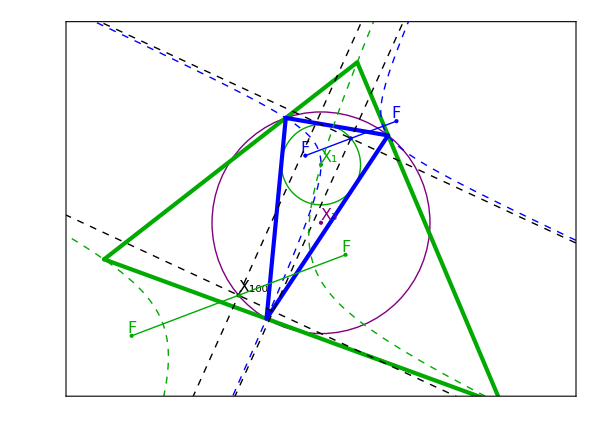

```mathematica
feuJerPlot=Module[{sc1,d=dsolChapple@rOvR[1.5],th=-30},
sc1=showChapple[d,th,minX->-2.25,maxX->2.25,minY->-1.5,maxY->1.75,plAreas->False,drX100->True,
drFeuerbach->True,drExcJerabek->True,drX100->False];
Show[sc1,PlotLabel->None,ImageSize->600,Frame->True,FrameTicks->None]]
```

```mathematica
export3["0170_feu_jexc",feuJerPlot];
```

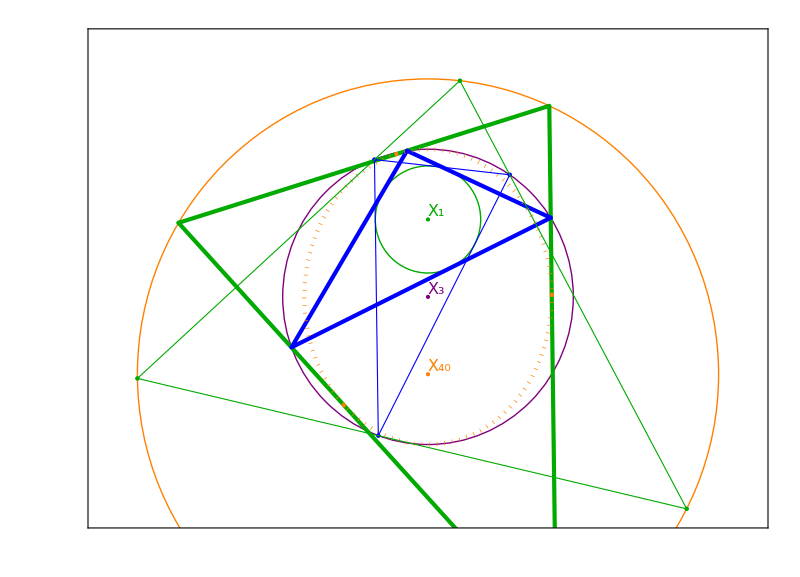

```mathematica
odehnalCirPlot=Module[{sc1,cd2,d=dsolChapple@rOvR[1.5],gr2},
sc1=showChapple[d,290,minX->-2.25,maxX->2.25,minY->-1.5,maxY->1.75,drExc->True,drExcCircle->True,plAreas->False,drX100->False,drExcCaustic->True,excCausticClr->Directive[Thick,Dotted,Orange]];
cd2=chappleData[d,340];
gr2=Graphics[{FaceForm@None,Thick,PointSize@Large,
MapThread[{drawPoly[cd2[#1],Directive[Dashed,#2]],#2,Point@cd2[#1]}&,{{"tri","exc"},{Blue,Darker@Green}}]}];
Show[{sc1,gr2},FrameTicks->None,PlotLabel->None,ImageSize->800,PlotRangeClipping->True]]
```

```mathematica
showX5X10[r_,tDeg_]:=Module[{d=dsolChapple[r],xlim=3,ylim=2.75,eps=.001},
Show[showChapple[d,tDeg+eps,minX->-xlim,maxX->xlim,minY->-ylim,maxY->ylim,drExc->True,drExcCircle->True,drL663->False,drExcCircumX5->True,drCircumX10->True,drCB->False,plAreas->False],ImageSize->800,PlotRangeClipping->True,FrameTicks->None]]
```

```mathematica
Clear@showExcCircumX6;showExcCircumX6[r_,tDeg_]:=Module[{d=dsolChapple[r],xlim=3,ymin=-2.75,ymax=2.75,eps=.001},
Show[showChapple[d,tDeg+eps,minX->-xlim,maxX->xlim,minY->ymin,maxY->ymax,drExc->True,drExcCircle->True,drExcCircumX6->True,drExcCircumX6FocusLocus->False,drCB->True,drCBFocusLocus->False,plAreas->False],ImageSize->800,PlotRangeClipping->True,FrameTicks->None]]
```

#### Note : E9 and E6' conserve aspect ratio and pairwise axis lengths, since they are in the same "EB" scale.

```mathematica
ratioX6X9[r_,tDeg_]:=Module[{d=dsolChapple[r],cd,lgts6,lgts9},
cd=chappleData[d,10.];
lgts6=cd["excCircumX6"]["lengths"];
lgts9=cd["cb"]["lengths"];
<|"x6_1_ov_x6_2"->lgts6[[1]]/lgts6[[2]],
"x9_1_ov_x9_2"->lgts9[[1]]/lgts9[[2]],
"x6_1_ov_x9_1"->lgts6[[1]]/lgts9[[1]],
"x6_2_ov_x9_2"->lgts6[[2]]/lgts9[[2]],
"x6_2_ov_x9_1"->lgts6[[2]]/lgts9[[1]],
"x6_1_ov_x9_2"->lgts6[[1]]/lgts9[[2]]|>]
```

```mathematica
ratioX6X9[rOvR[1.5],100.]
```

<|x6_1_ov_x6_2→0.468375,x9_1_ov_x9_2→0.666667,x6_1_ov_x9_1→1.96837,x6_2_ov_x9_2→2.80171,x6_2_ov_x9_1→4.20256,x6_1_ov_x9_2→1.31225|>

```mathematica
ratioX6X9[rOvR[1.5],120.]
```

<|x6_1_ov_x6_2→0.468375,x9_1_ov_x9_2→0.666667,x6_1_ov_x9_1→1.96837,x6_2_ov_x9_2→2.80171,x6_2_ov_x9_1→4.20256,x6_1_ov_x9_2→1.31225|>

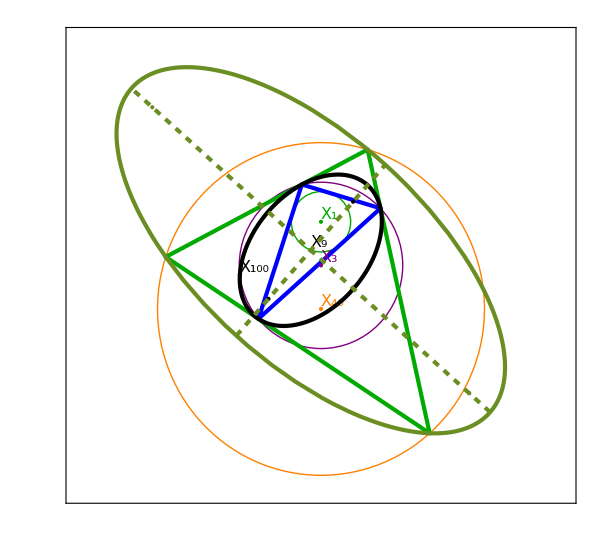

```mathematica
excCircumX6plot=Show[showExcCircumX6[rOvR[1.5],-50.],ImageSize->600,PlotLabel->None]
```

```mathematica
export3["0112_circum_x6p",excCircumX6plot]
```

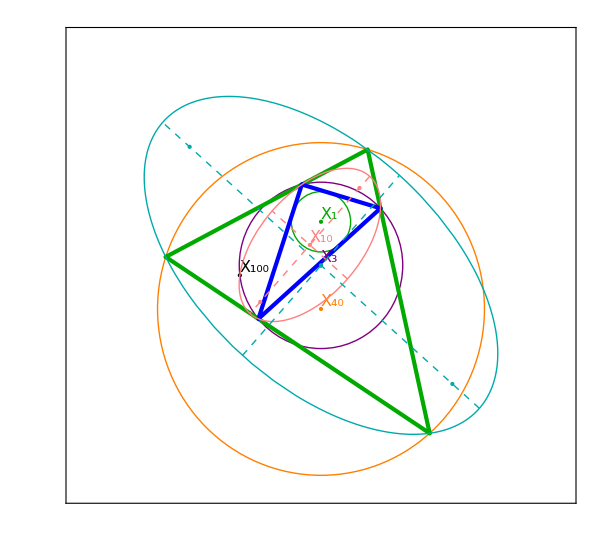

```mathematica
circumX5X10plot=Show[showX5X10[rOvR[1.5],-50.],PlotLabel->None,ImageSize->600]
```

```mathematica
export3["0114_circum_x5_x10",circumX5X10plot]
```

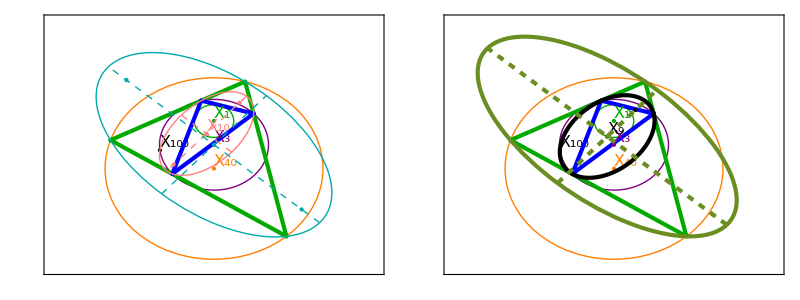

```mathematica
pairX5X10X6plot=Grid[{{circumX5X10plot,excCircumX6plot}}]
```

```mathematica
export3["0110_circum_x10_exc_x5_exc_x6_pair",pairX5X10X6plot]
```

```mathematica
export3["0080_odehnal_cir",odehnalCirPlot]
```

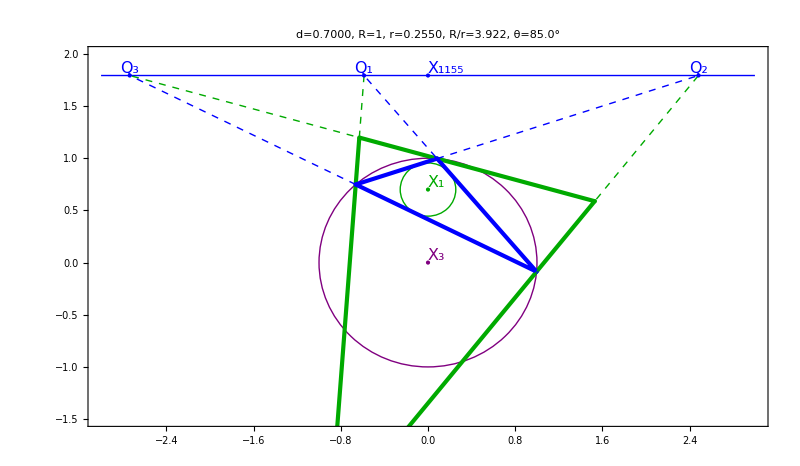

```mathematica
antiOrthicPlot=Show[showChapple[.7,85,minX->-3,maxX->3,minY->-1.5,maxY->2.,drExc->True,drAntiorthic->True,drAntiorthicConstr->True,plAreas->False,drX100->False],ImageSize->800,PlotRangeClipping->True]
```

```mathematica
export3["0050_weaver_antiorthic",antiOrthicPlot]
```

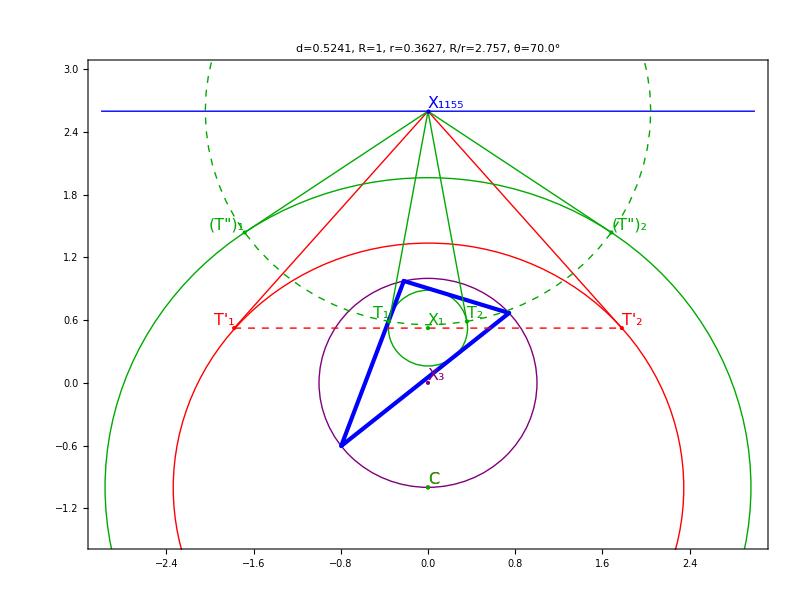

```mathematica
weaverCircPlot=Show[showChapple[.5241,70.,minX->-3,maxX->3,minY->-1.5,maxY->3,drExc->False,drAntiorthic->True,drWeaverCirc->True,drEqualPowerInc->True,plAreas->False,drX100->False],ImageSize->800,PlotRange->{Automatic,{-1.5,3}},PlotRangeClipping->True]
```

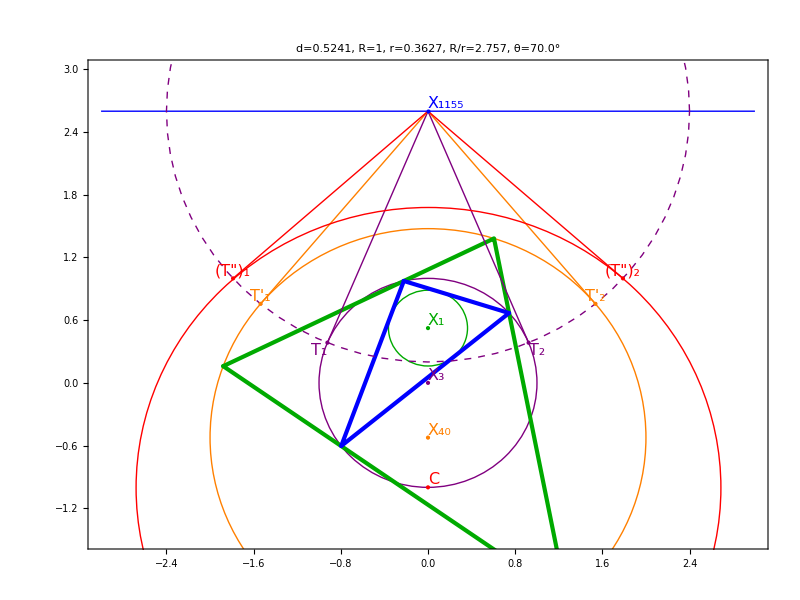

```mathematica
equalPowerCirPlot=Show[showChapple[.5241,70.,minX->-3,maxX->3,minY->-3,maxY->3,drExc->True,drExcCircle->True,drAntiorthic->True,drEqualPowerCir->True,plAreas->False,drX100->False],ImageSize->800,PlotRange->{Automatic,{-1.5,3}},PlotRangeClipping->True]
```

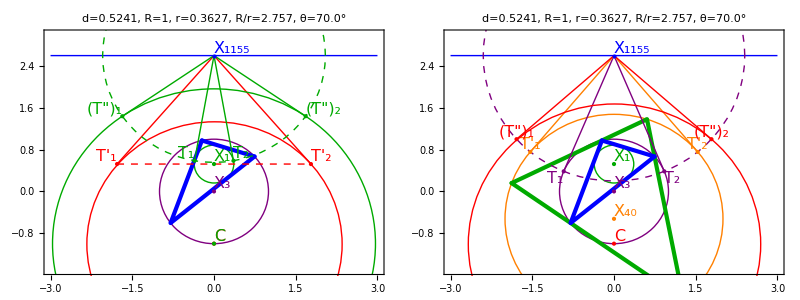

```mathematica
weaverCircPairPlot=Grid[{{weaverCircPlot,equalPowerCirPlot}},Frame->All]
```

```mathematica
export3["0120x_weaver_power_cir",weaverCircPairPlot]
```

```mathematica
(* rho is r/R *)
ronaldoIncX5axisRatio[rho_]:=1/Sqrt[2rho];
```

```mathematica
ronaldoIncX5axisRatio[rOvR[1.5]]
```

1.17418

```mathematica
FullSimplify[excIncX3AxisRatio[r,R],r>0&&R>0]
```

(-r+R+√(R (-2 r+R)))/r

```mathematica
excIncX3AxisRatio[.3142,1]
```

4.12282

```mathematica
Clear@showOnePoristicSimple;
showOnePoristicSimple[r_,tDeg_,opts:OptionsPattern[]]:=Module[{eps=.001,d},
d=dsolChapple[r];
Show[showChapple[d,tDeg+eps,minX->-2.5,maxX->2.5,minY->-3,maxY->2,plShort->True,drX100->False,FilterRules[{opts},Options@showChapple]],Frame->None,Axes->True,ImageSize->500]
]
```

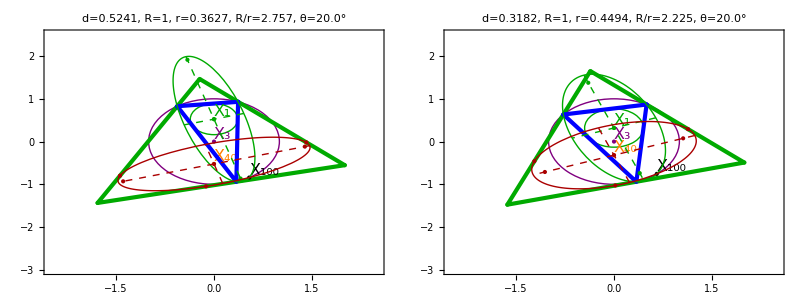

```mathematica
Grid[{{Show[showChapple[dsolChapple[rOvR[1.5]],20.,minX->-2.5,maxX->2.5,minY->-3,maxY->2.5,plShort->True,drCircumX1->True,drExcIncX3->True],ImageSize->600],Show[showChapple[dsolChapple[rOvR[1.25]],20.,minX->-2.5,maxX->2.5,minY->-3,maxY->2.5,plShort->True,drCircumX1->True,drExcIncX3->True],ImageSize->600]}},Frame->All]
```

```mathematica
Module[{d},
d=R Sqrt[(1-2r/R)];
Solve[d==r,r]]
```

{{r→-R+√2 R}}

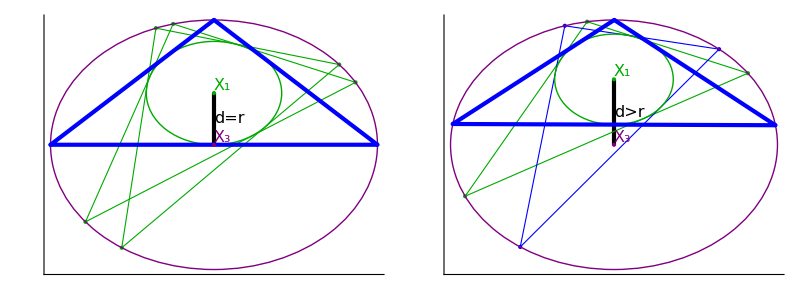

```mathematica
obtusePlot=Module[{r=Sqrt[2.]-1,r2=1.5,gr,gr2,cd,d2,cd0,cd2,cd3,por1,por2},
cd=chappleData[r,120.];
cd0=chappleData[r,130.];
gr=Graphics[{Text[Style["d=r",16],{0,r/2},{-1.4,0}],Thick,Line@{{0,0},{0,r}},FaceForm@None,drawPoly[cd["tri"],Directive[Dashed,Darker@Green]],drawPoly[cd0["tri"],Directive[Dashed,Darker@Green]]}];
por1=Show[{gr,Quiet@showOnePoristicSimple[r,90.001,drExc->False]},ImageSize->400,PlotRange->All,Frame->False,Axes->True,AxesStyle->Dashed,Ticks->None];
cd2=chappleData[dsolChapple@rOvR[r2],125.];
cd3=chappleData[dsolChapple@rOvR[r2],140.];
d2=dsolChapple[rOvR[r2]];
gr2=Graphics[{Text[Style["d>r",16],{0,d2/2},{-1.4,0}],Thick,Line@{{0,0},{0,d2}},FaceForm@None,drawPoly[cd2["tri"],Directive[Dashed,Darker@Green]],drawPoly[cd3["tri"],Directive[Dashed,Blue]]}];
por2=Show[{gr2,Quiet@showOnePoristicSimple[rOvR[r2],99,drExc->False]},ImageSize->400,PlotRange->All,Frame->False,Axes->True,AxesStyle->Dashed,Ticks->None,PlotLabel->None];
Grid[{{por1,por2}}]]
```

```mathematica
export3["0080_obtuse_poristics",obtusePlot]
```

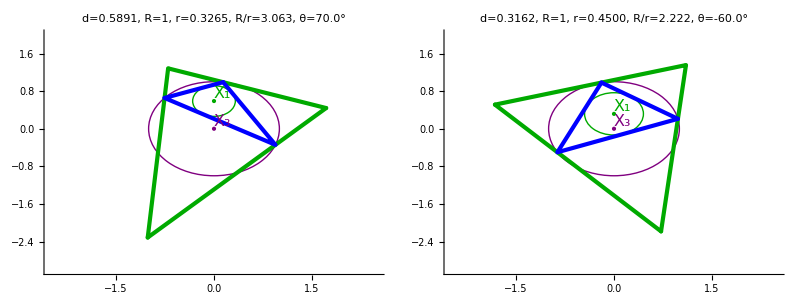

```mathematica
poristicSimplePlot=Grid[{{showOnePoristicSimple[.3265,70.],showOnePoristicSimple[.45,-60.]}},Frame->All]
```

```mathematica
export4["0010_poristic_pair",poristicSimplePlot]
```

```mathematica
Clear@showOnePoristicExcIncX3;
showOnePoristicExcIncX3[r_,tDeg_]:=Module[{eps=.001,d},
d=dsolChapple[r];
Show[showChapple[d,tDeg+eps,minX->-4,maxX->4,minY->-3,maxY->3,
drExc->True,
drExcCaustic->True,
drTangential->False,
drExcMed->False,
drMitten->False,drCB->False,plShort->True,drExcIncX3->True,drCircumX1->True],PlotRange->All,Frame->None,Axes->True,ImageSize->600]
]
```

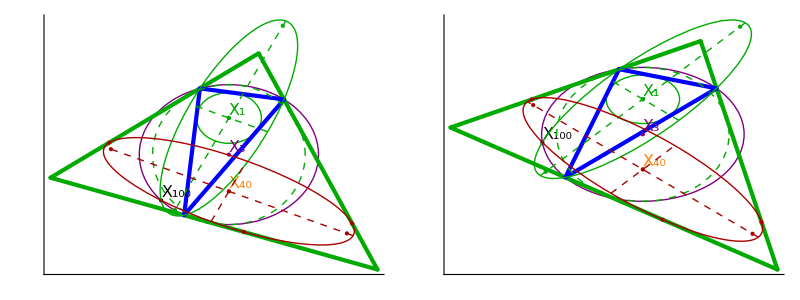

```mathematica
poristicInvariantPlot=Grid[{Show[#,PlotLabel->None,Ticks->None]&/@{showOnePoristicExcIncX3[rOvR[1.5],-30.],showOnePoristicExcIncX3[rOvR[1.5],-50.]}},Frame->All]
```

```mathematica
export3["0030_poristic_invariants",poristicInvariantPlot]
```

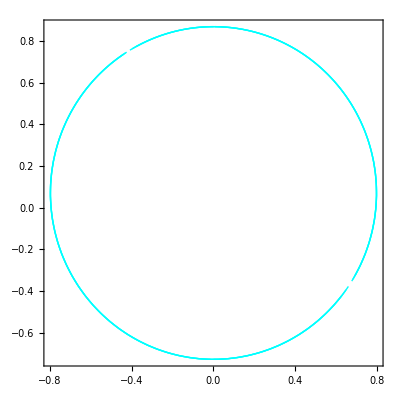

```mathematica
cbFocusLocus=Module[{r=rOvR[1.5],d,fs,pos1,pos2,fs1,fs2,jumps1,jumps2,d2lim=.1,valids1,valids2},
d=dsolChapple[r];
fs=Table[chappleData[d,tDeg+.01]["cb"]["foci"],{tDeg,0,360,1}];
fs1=First/@fs;
jumps1=MapThread[magn2[#2-#1]&,{Most@fs1,Rest@fs1}];
pos1=Flatten@Position[jumps1,d2_ /; d2>d2lim];
valids1=MapThread[{#1,#2}&,{Prepend[pos1+1,1],Append[pos1-1,Length@jumps1]}];
fs2=Second/@fs;
jumps2=MapThread[magn2[#2-#1]&,{Most@fs2,Rest@fs2}];
pos2=Flatten@Position[jumps2,d2_ /; d2>d2lim];
valids2=MapThread[{#1,#2}&,{Prepend[pos2+1,1],Append[pos2-1,Length@jumps2]}];
Graphics[{Thick,Cyan,Line[Take[fs1,#]&/@valids1],Line[Take[fs2,#]&/@valids2]},Frame->True,Axes->True]]
```

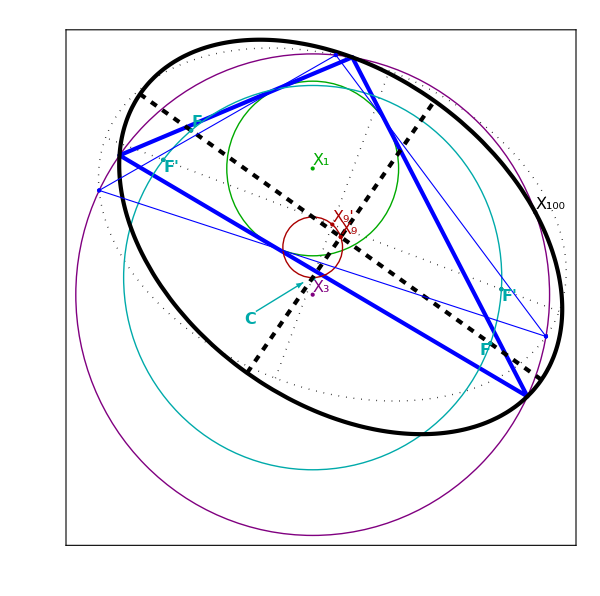

```mathematica
constCBporisticPlot=Module[{r=rOvR[1.5],eps=.001,d,p1,p2,cd1,cd2,gr2,cb2,t1=65,t2=80},
d=dsolChapple[r];
p1=Show[showChapple[d,t1+eps,minX->-4,maxX->4,minY->-3,maxY->3,
drExc->False,
drExcCaustic->False,
drTangential->False,
drExcMed->False,drMitten->True,drCB->True,drCBFocusLocus->True,plShort->True],PlotRange->All,Frame->None,Axes->True,ImageSize->600];
cd1=chappleData[dsolChapple[r],t1+eps];
cd2=chappleData[dsolChapple[r],t2+eps];
gr2=Graphics[{FaceForm@None,Thick,PointSize@Large,Arrowheads@Medium,
{drawPoly[cd2["tri"],Directive[Dashed,Blue]],Blue,Point@cd2["tri"]},{Darker@Cyan,Translate[{Text[Style["C",{Bold,16}],{-.2,-.05},{1.2,.5}],Arrow@{{-.2,-.05},cd2["cbFocusLocusCtr"]}},{-.04,-.02}],MapThread[Text[Style["F'",{Bold,16}],#1,#2]&,{cd2["cb"]["foci"],{{-1.5,1.75},{-1.25,1.5}}}],Point@cd2["cb"]["foci"],
MapThread[Text[Style["F",{Bold,16}],#1,#2]&,{cd1["cb"]["foci"],{{2,1.},{-.5,-1.5}}}],Point@cd1["cb"]["foci"]}}];
cb2=drawCircumAnyLow[cd2["cb"],cd2["tri"],drFoci->True,ctrLab->Style["X_9'",16],labClr->Darker@Red,ps->Directive[Thick,Dotted,Black]];
Show[{cb2,p1,gr2},Frame->True,FrameTicks->None,PlotLabel->None,ImageSize->600]]
```

```mathematica
export3["0160_poristic_cb",constCBporisticPlot]
```

```mathematica
Clear@showCBFocusLocus;
showCBFocusLocus[r_,tDeg_]:=Module[{eps=.001,d,p1,p2,cd1,gr},
d=dsolChapple[r];
p1=Show[showChapple[d,tDeg+eps,minX->-4,maxX->4,minY->-3,maxY->3,
drExc->False,
drExcCaustic->False,
drTangential->False,
drExcMed->False,drMitten->True,drCB->True,plShort->True],PlotRange->All,Frame->None,Axes->True,ImageSize->600];
cd1=chappleData[dsolChapple[r],tDeg+eps];
gr=Graphics[{FaceForm@None,Thick,PointSize@Large,
{Thick,Cyan,Circle[cd1["cbFocusLocusCtr"],cd1["cbFocusLocusRad"]]},
{Darker@Cyan,PointSize@Large,Point@cd1["cbFocusLocusCtr"],
Text[Style["C",{Bold,16}],cd1["cbFocusLocusCtr"],{1.25,-1.25}],
MapThread[Text[Style["F",{Darker@Cyan,{Bold,16}}],#1,#2]&,{cd1["cb"]["foci"],{{2,1.},{-.5,-1.5}}}],Point@cd1["cb"]["foci"]}}];
Show[{p1,gr},Frame->True,FrameTicks->None,PlotLabel->None,ImageSize->800,PlotRange->{{-1.25,1.25},{-1.25,1.25}}]]
```

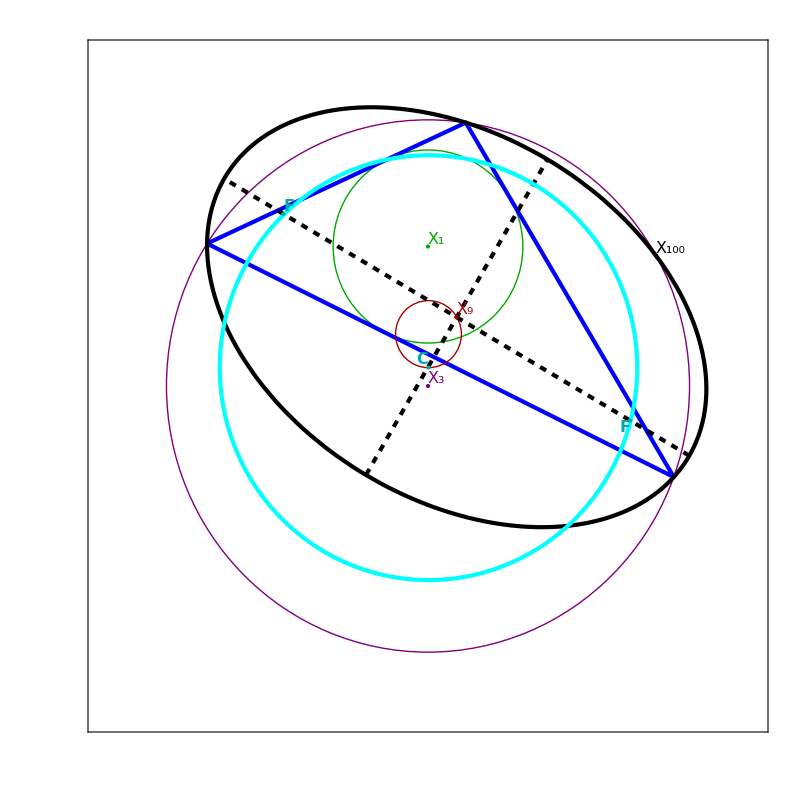

```mathematica
showCBFocusLocus[rOvR[1.5],70.]
```

```mathematica
FullSimplify[rOvR[3/2]]
```

2/25 (-97+13 √61)

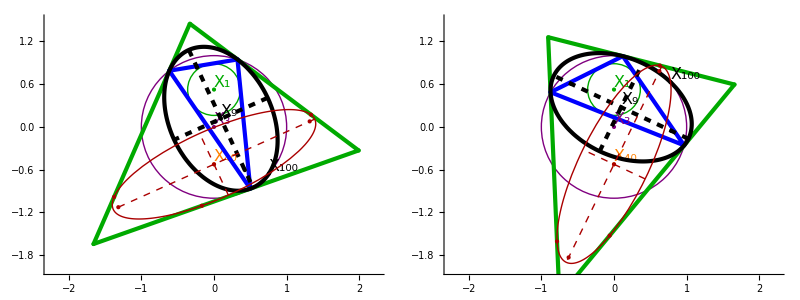

```mathematica
constCBporisticX3Plot=Module[{r=rOvR[1.5],eps=.001,d,p1,p2,xmax=2.25,sz=500},
d=dsolChapple[r];
p1=Show[showChapple[d,30.+eps,minX->-xmax,maxX->xmax,minY->-2,maxY->1.5,
drExcIncX3->True,drExc->True,
drMitten->False,drCB->True,plShort->True],Frame->None,Axes->True,ImageSize->sz,PlotLabel->None];
p2=Show[showChapple[d,75+eps,minX->-xmax,maxX->xmax,minY->-2,maxY->1.5,
drExcIncX3->True,drExc->True,
drMitten->False,drCB->True,plShort->True],Frame->None,Axes->True,ImageSize->sz,PlotLabel->None];
Grid[{{p1,p2}},Frame->All]]
```

```mathematica
export3["0040_cb_x3",constCBporisticX3Plot]
```

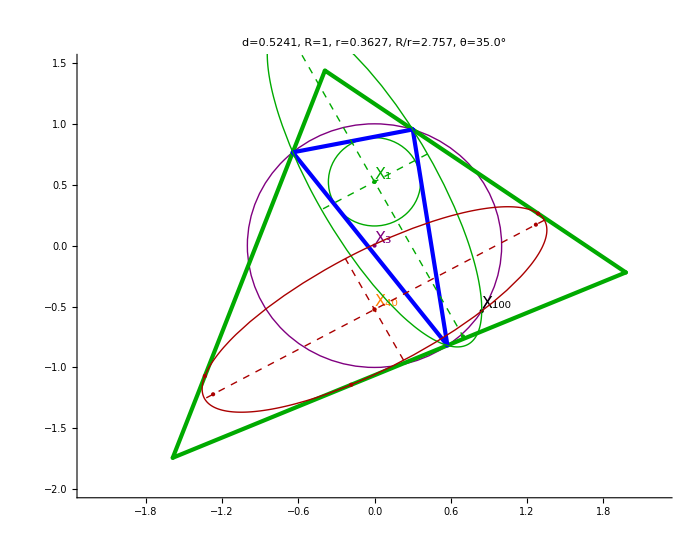

```mathematica
constCBporisticX3SinglePlot=Module[{r=rOvR[1.5],eps=.001,d,p1,p2,xmax=2.25,sz=700},
d=dsolChapple[r];
p1=Show[showChapple[d,35.+eps,minX->-xmax,maxX->xmax,minY->-2,maxY->1.5,
drExcIncX3->True,drExc->True,
drMitten->False,drCB->False,plShort->True,drCircumX1->True],Frame->None,Axes->True,ImageSize->sz];
p1]
```

```mathematica
showChappleX9[a_,tDeg_,r_]:=Module[{R=1,d,excLocus,eps=.01,x3={0,0},x1,excCaustic,excCausticA,excCausticB,chap},
d=dsolChapple[r];
x1={0,d};
excLocus=Graphics[{Thick,Orange,Circle[x3+(x3-x1),2R]}];
excCausticA=Abs@chappleData[d,eps]["exc"][[2,2]];
excCausticB=Sqrt[excCausticA^2-d^2];
excCaustic=Graphics[{Thick,Dashed,Darker@Green,Circle[{0,0},{excCausticB,excCausticA}]}];
chap=showChapple[d,tDeg+eps,minX->-2.5,maxX->2.5,minY->-3,maxY->3,
drMitten->True,drCB->True,
drTangential->False,drExcMed->False,drWeaverCirc->False,drNpcHex->False,drExcFeuerbach->False,drFeuerbach->False,drExcJerabek->False,drJerabek->False];
Show[{chap,excLocus,excCaustic},Frame->True,ImageSize->800]];
```

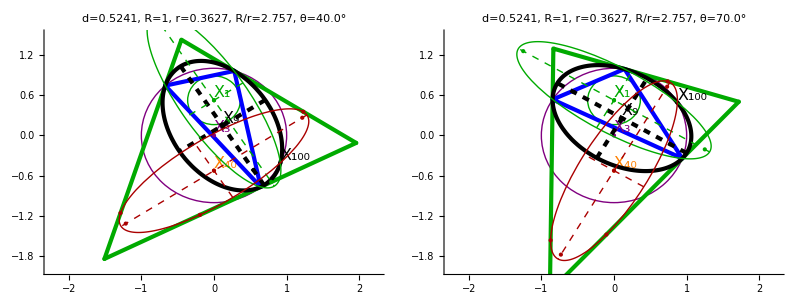

```mathematica
constCBporisticX3PlotE1=Module[{r=rOvR[1.5],eps=.001,d,p1,p2,xmax=2.25},
d=dsolChapple[r];
p1=Show[showChapple[d,40.+eps,minX->-xmax,maxX->xmax,minY->-2,maxY->1.5,
drExcIncX3->True,drExc->True,drCircumX1->True,
drMitten->False,drCB->True,plShort->True],Frame->None,Axes->True,ImageSize->600];
p2=Show[showChapple[d,70+eps,minX->-xmax,maxX->xmax,minY->-2,maxY->1.5,
drExcIncX3->True,drExc->True,drCircumX1->True,
drMitten->False,drCB->True,plShort->True],Frame->None,Axes->True,ImageSize->600];
Grid[{{p1,p2}},Frame->All]]
```

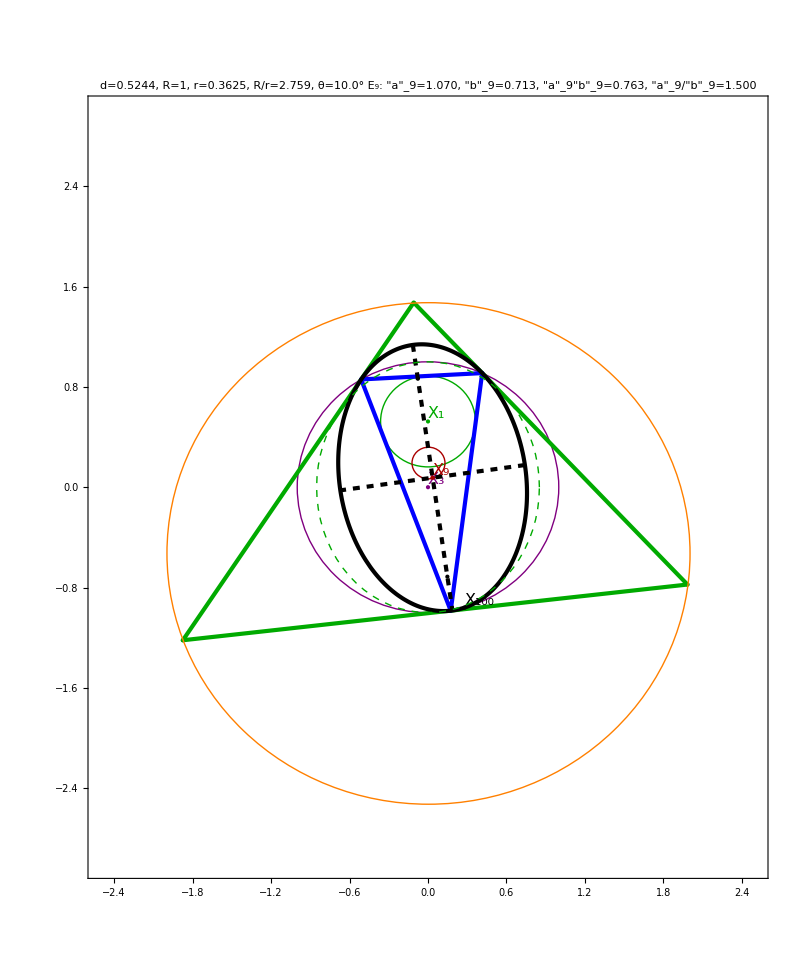

```mathematica
showChappleX9[1.5,10.,.3625]
```

```mathematica
Clear@showPoristicSimson;
showPoristicSimson[r_,tDeg_]:=Module[{eps=.001,d},
d=dsolChapple[r];
Show[showChapple[d,tDeg+eps,minX->-2.5,maxX->2.5,minY->-3,maxY->2,plShort->True,
drExcCaustic->False,drExcMed->True,drSimson->True],Frame->None,Axes->True,ImageSize->600]
]
```

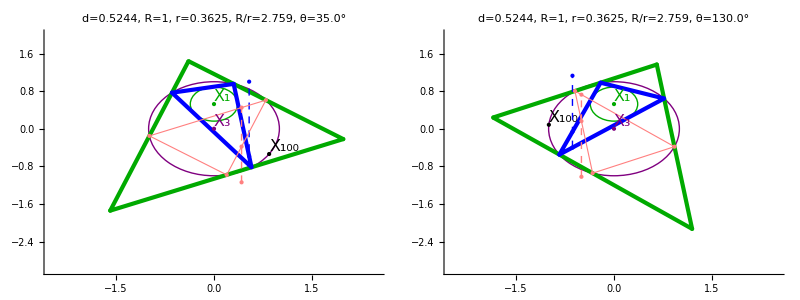

```mathematica
pedalX100plot=Grid[{{showPoristicSimson[.3625,35.],showPoristicSimson[.3625,130.]}},Frame->All]
```

```mathematica
export3["020_pedal_x100",pedalX100plot]
```

#### Poristic Perimeter

```mathematica
rOvR[1.5]
```

0.36266

```mathematica
chappleData[dsolChapple[rOvR[1.5]],10.]["cb"]
```

<|ctr→{0.0352568,0.0758117},coeffs→{0.161653,0.147841,-0.30844,-1.9609,-0.903333},vals→{-3.96586,-1.7626},valsMinMax→{-1.7626,-3.96586},axes→{{-0.989951,-0.141414},{0.141414,-0.989951}},major→{0.141414,-0.989951},minor→{-0.989951,-0.141414},minorVal→-1.7626,majorVal→-3.96586,lengths→{0.713139,1.06971},ratio→0.666667,prod→0.762851,vertices→{{-0.670716,-0.0250361},{0.186528,-0.983147}},foci→{{-0.0774945,0.865113},{0.148008,-0.713489}},c→0.797314,orbit→{{0.173648,-0.984808},{0.414665,0.909974},{-0.511407,0.859339}},orbitTangents→{{-1.8735,-0.215606},{1.62408,-1.74525},{1.24696,1.90223}},area→2.39657|>

#### Not Invariant: CB Minor Axis

```mathematica
Module[{d=dsolChapple[rOvR[1.5]],eps=.001,cd},
getStats[Table[cd=chappleData[d,tDeg+eps];cd["cb"]["lengths"][[1]],{tDeg,0,360}]]]
```

<|n→361,mean→0.695784,sd→0.0129293,z→0.0185824,min→0.677378,max→0.71385,median→0.695803,label→|>

#### Not Invariant: CB Major Axis

```mathematica
Module[{d=dsolChapple[rOvR[1.5]],eps=.001,cd},
getStats[Table[cd=chappleData[d,tDeg+eps];cd["cb"]["lengths"][[2]],{tDeg,0,360}]]]
```

<|n→361,mean→1.04368,sd→0.019394,z→0.0185824,min→1.01607,max→1.07078,median→1.0437,label→|>

#### Invariant: CB Axis Ratio

```mathematica
Module[{d=dsolChapple[rOvR[1.5]],eps=.001,cd},
getStats[Table[cd=chappleData[d,tDeg+eps];cd["cb"]["lengths"][[2]]/cd["cb"]["lengths"][[1]],{tDeg,0,360}]]]
```

<|n→361,mean→1.5,sd→4.53398×10^-16,z→3.02265×10^-16,min→1.5,max→1.5,median→1.5,label→|>

#### Invariant: Poristic Perimeter / CB Minor Axis

```mathematica
Module[{d=dsolChapple[rOvR[1.5]],eps=.001,cd},
getStats[Table[cd=chappleData[d,tDeg+eps];cd["triPer"]/cd["cb"]["lengths"][[1]],{tDeg,0,360}]]]
```

<|n→361,mean→6.73751,sd→3.29512×10^-14,z→4.89071×10^-15,min→6.73751,max→6.73751,median→6.73751,label→|>

#### Invariant: Poristic Perimeter / CB Major Axis

```mathematica
Module[{d=dsolChapple[rOvR[1.5]],eps=.001,cd},
getStats[Table[cd=chappleData[d,tDeg+eps];cd["triPer"]/cd["cb"]["lengths"][[2]],{tDeg,0,360}]]]
```

<|n→361,mean→4.49167,sd→2.95515×10^-14,z→6.57917×10^-15,min→4.49167,max→4.49167,median→4.49167,label→|>

#### Invariant: Poristic Perimeter / CB Axis Sum

```mathematica
Module[{d=dsolChapple[rOvR[1.5]],eps=.001,cd},
getStats[Table[cd=chappleData[d,tDeg+eps];triPer@cd["tri"]/Total[cd["cb"]["lengths"]],{tDeg,0,360}]]]
```

<|n→361,mean→2.695,sd→4.6451×10^-15,z→1.7236×10^-15,min→2.695,max→2.695,median→2.695,label→|>

#### Not invariant : Poristic Perimeter / CB Axis Product

```mathematica
Module[{d=dsolChapple[rOvR[1.5]],eps=.001,cd},
getStats[Table[cd=chappleData[d,tDeg+eps];triPer@cd["tri"]/Apply[Times,cd["cb"]["lengths"]],{tDeg,0,360}]]]
```

<|n→361,mean→6.45778,sd→0.120072,z→0.0185934,min→6.29218,max→6.63097,median→6.45538,label→|>

#### Invariant : Poristic Perimeter / Geometric Meand of CB Axes

```mathematica
geomMean[a_,b_]:=Sqrt[a b];
```

```mathematica
Module[{d=dsolChapple[rOvR[1.5]],eps=.001,cd},
getStats[Table[cd=chappleData[d,tDeg+eps];triPer@cd["tri"]/geomMean@@cd["cb"]["lengths"],{tDeg,0,360}]]]
```

<|n→361,mean→5.50115,sd→3.62633×10^-14,z→6.59195×10^-15,min→5.50115,max→5.50115,median→5.50115,label→|>

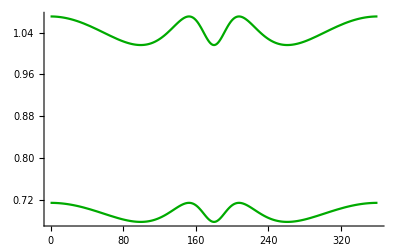

```mathematica
Module[{d=dsolChapple[rOvR[1.5]],eps=.001,cd},
Plot[cd=chappleData[d,tDeg+eps];
cd["cb"]["lengths"],{tDeg,0,360},PlotStyle->{Blue,Darker@Green}]]
```

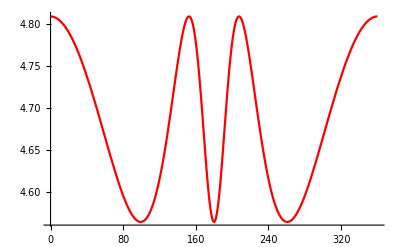

```mathematica
Module[{d=dsolChapple[rOvR[1.5]],eps=.001,cd},
Plot[cd=chappleData[d,tDeg+eps];
triPer@cd["tri"],{tDeg,0,360},PlotStyle->{Blue,Darker@Green,Red}]]
```

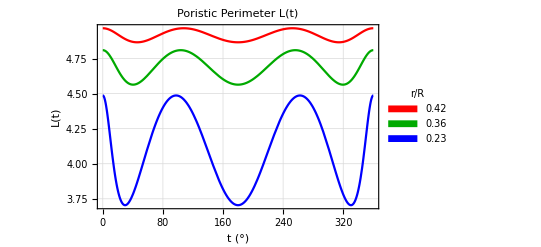

```mathematica
porPerPlot=Module[{a9b9s={1.33,1.5,2.},rs,ds},
rs=rOvR[#]&/@a9b9s;
ds=dsolChapple/@rs;
Plot[
Evaluate[poristicPer[#,1,Cos[toRad@tDeg]]&/@ds],{tDeg,0,360},PlotStyle->{Red,Darker@Green,Blue},GridLines->Automatic,Frame->True,FrameStyle->Directive[14,Black],FrameLabel->(Style[#,{16,Black}]&/@{"t (°)","L(t)"}),PlotLabel->Style["Poristic Perimeter L(t)",{Black,16}],PlotLegends->Placed[SwatchLegend[Style[nfn[#,2],16]&/@rs,LegendLabel->Style["r/R",16]],Right]]]
```

```mathematica
a9ovL[R_,d_]:=(R*Sqrt@(3*R^2+2*R*d-d^2))/(9*R^2-d^2)
```

```mathematica
1/a9ovL[1,dsolChapple[rOvR[1.5]]]
```

4.49167

```mathematica
a9ovL[1,dsolChapple[1/2]]
```

1/(3 √3)

```mathematica
a9ovL[1,dsolChapple[.5]]
```

0.19245

```mathematica
a9ovL[1,dsolChapple[0]]
```

1/4

```mathematica
b9ovL[R_,d_]:=Sqrt@(R-d)*R/(Sqrt@(3*R+d)*(3*R-d));
```

```mathematica
1/b9ovL[1,dsolChapple[rOvR[1.5]]]
```

6.73751

```mathematica
b9ovL[1,dsolChapple[.5]]
```

0.19245

```mathematica
b9ovL[1,dsolChapple[0]]
```

0

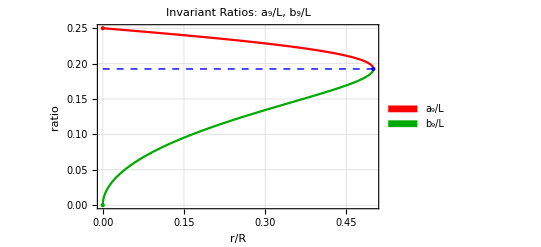

```mathematica
porRatioPlot=Module[{rs={1.33,1.5,2.},ds,lim=a9ovL[1,dsolChapple[.5]],lim0=a9ovL[1,dsolChapple[0]]},
ds=dsolChapple[rOvR[#]]&/@rs;
Plot[{
a9ovL[1,dsolChapple[r]],
b9ovL[1,dsolChapple[r]]},
{r,0.0,.5},PlotStyle->{Red,Darker@Green,Blue},GridLines->Automatic,Frame->True,FrameStyle->Directive[14,Black],FrameLabel->(Style[#,{16,Black}]&/@{"r/R","ratio"}),(*PlotLabel->Style["Poristic Perimeter L(t)",{Black,16}],*)PlotLegends->Placed[SwatchLegend[Style[#,16]&/@{"a_9/L","b_9/L"}],Right],
PlotLabel->Style["Invariant Ratios: a_9/L, b_9/L",{16,Black}],
Epilog->{PointSize@Large,Blue,Point@{.5,lim},{Dashed,Thick,Line@{{0,lim},{.5,lim}}},Red,Point@{0,lim0},Darker@Green,Point@{0,0}}]]
```

```mathematica
perAxisRatioPlot=Grid[{Show[#,ImageSize->400]&/@{porPerPlot,porRatioPlot}},Frame->All]
```

-Graphics- | -Graphics-

```mathematica
export3["0090_poristic_per_axis_ratio",perAxisRatioPlot]
```

```mathematica
Module[{d=dsolChapple[rOvR[1.5]],eps=.001,cd},
getStats[Table[cd=chappleData[d,tDeg+eps];cd["triPer"],{tDeg,0,360}]]]
```

<|n→361,mean→4.68785,sd→0.0871116,z→0.0185824,min→4.56384,max→4.80957,median→4.68798,label→|>

```mathematica
Module[{d=dsolChapple[rOvR[1.5]],eps=.001,cd},
getStats[Table[poristicPer[d,1,Cos[toRad@tDeg]],{tDeg,0,360}]]]
```

<|n→361,mean→4.68785,sd→0.0871116,z→0.0185824,min→4.56384,max→4.80957,median→4.68876,label→|>

#### Locus of Foci of E9 seems circular, and E6' does not seem elliptic

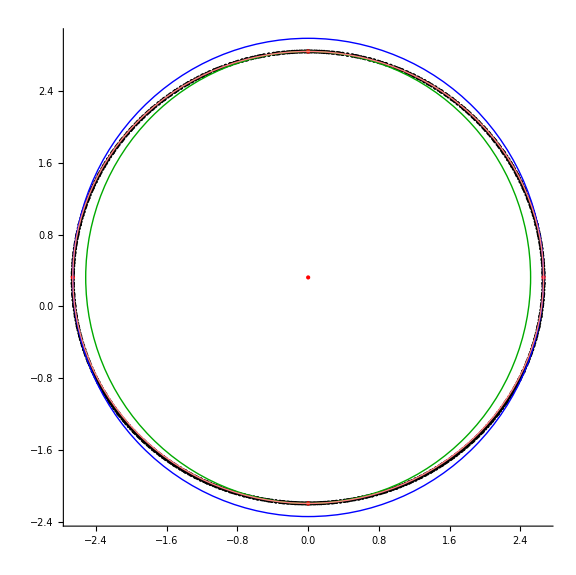

findEllParams[1.5,-1,{{2.65059,-0.251809},{-2.65059,-0.251885},{2.65387,-0.214184},{-2.64672,-0.289408},{2.65656,-0.176465},{-2.64228,-0.326823},{2.65865,-0.138661},{-2.63725,-0.364121},{2.66016,-0.10078},{-2.63165,-0.401295},{2.66107,-0.0628286},{-2.62547,-0.438337},{2.66138,-0.0248161},{-2.61872,-0.475239},{2.66109,0.0132497},{-2.6114,-0.511994},{2.66019,0.0513605},{-2.60352,-0.548595},{2.6587,0.0895082},{-2.59507,-0.585034},{2.65659,0.127684},{-2.58607,-0.621304},{2.65388,0.165881},{-2.57652,-0.657397},{2.65056,0.204089},{-2.56641,-0.693308},{2.64663,0.242301},{-2.55575,-0.729028},{2.64208,0.280509},{-2.54455,-0.764551},{2.63692,0.318702},{-2.53281,-0.79987},{2.63115,0.356874},{-2.52054,-0.834978},{2.62475,0.395015},{-2.50773,-0.869868},{2.61774,0.433117},{-2.49439,-0.904535},{2.61011,0.471172},{-2.48053,-0.93897},{2.60186,0.50917},{-2.46614,-0.973168},{2.59299,0.547103},{-2.45124,-1.00712},{2.58349,0.584962},{-2.43583,-1.04083},{2.57337,0.622738},{-2.41991,-1.07428},{2.56263,0.660424},{-2.40349,-1.10746},{2.55126,0.698009},{-2.38656,-1.14038},{2.53927,0.735485},{-2.36915,-1.17303},{2.52666,0.772843},{-2.35124,-1.20539},{2.51342,0.810075},{-2.33284,-1.23747},{2.49955,0.847171},{-2.31396,-1.26926},{2.48506,0.884122},{-2.2946,-1.30076},{2.46994,0.92092},{-2.27477,-1.33195},{2.45419,0.957555},{-2.25447,-1.36283},{2.43782,0.994019},{-2.23371,-1.3934},{2.42082,1.0303},{-2.21249,-1.42366},{2.4032,1.0664},{-2.19081,-1.45359},{2.38495,1.10229},{-2.16868,-1.48319},{2.36608,1.13798},{-2.14611,-1.51246},{2.34658,1.17345},{-2.12309,-1.5414},{2.32646,1.20869},{-2.09964,-1.56999},{2.30571,1.2437},{-2.07575,-1.59823},{2.28434,1.27846},{-2.05144,-1.62613},{2.26235,1.31297},{-2.0267,-1.65367},{2.23974,1.34722},{-2.00154,-1.68085},{2.21651,1.38119},{-1.97597,-1.70767},{2.19265,1.41489},{-1.94999,-1.73412},{2.16818,1.44829},{-1.9236,-1.7602},{2.14309,1.48139},{-1.89681,-1.7859},{2.11738,1.51418},{-1.86962,-1.81123},{2.09105,1.54665},{-1.84204,-1.83617},{2.06411,1.57879},{-1.81407,-1.86072},{2.03655,1.61059},{-1.78571,-1.88489},{2.00838,1.64205},{-1.75697,-1.90866},{1.9796,1.67314},{-1.72785,-1.93203},{1.95021,1.70387},{-1.69836,-1.955},{1.9202,1.73422},{-1.6685,-1.97757},{1.88959,1.76418},{-1.63827,-1.99974},{1.85837,1.79374},{-1.60768,-2.02149},{1.82655,1.82289},{-1.57673,-2.04282},{1.79411,1.85163},{-1.54542,-2.06375},{1.76108,1.87993},{-1.51376,-2.08425},{1.72744,1.9078},{-1.48174,-2.10432},{1.6932,1.93522},{-1.44938,-2.12398},{1.65836,1.96217},{-1.41667,-2.1432},{1.62292,1.98865},{-1.38362,-2.16199},{1.58688,2.01466},{-1.35023,-2.18035},{1.55025,2.04016},{-1.3165,-2.19826},{1.51302,2.06516},{-1.28244,-2.21574},{1.4752,2.08965},{-1.24803,-2.23277},{1.43679,2.1136},{-1.2133,-2.24935},{1.39778,2.13702},{-1.17823,-2.26549},{1.35819,2.15988},{-1.14283,-2.28116},{1.31801,2.18218},{-1.1071,-2.29638},{1.27723,2.2039},{-1.07104,-2.31114},{1.23588,2.22503},{-1.03465,-2.32543},{1.19394,2.24555},{-0.997932,-2.33926},{1.15141,2.26546},{-0.960884,-2.35261},{1.1083,2.28474},{-0.923506,-2.36548},{1.06462,2.30337},{-0.885798,-2.37787},{1.02035,2.32134},{-0.847758,-2.38978},{0.975506,2.33863},{-0.809386,-2.40119},{0.930085,2.35524},{-0.770679,-2.4121},{0.884089,2.37113},{-0.731636,-2.42252},{0.83752,2.38631},{-0.692255,-2.43242},{0.790378,2.40074},{-0.652534,-2.44182},{0.742667,2.41442},{-0.612469,-2.45069},{0.694387,2.42732},{-0.572057,-2.45903},{0.645541,2.43943},{-0.531296,-2.46684},{0.59613,2.45073},{-0.490181,-2.4741},{0.546157,2.46119},{-0.448708,-2.48081},{0.495624,2.47081},{-0.406874,-2.48696},{0.444533,2.47954},{-0.364672,-2.49254},{0.392888,2.48738},{-0.3221,-2.49754},{0.340692,2.4943},{-0.27915,-2.50194},{0.287947,2.50028},{-0.235817,-2.50573},{0.234657,2.50529},{-0.192097,-2.50891},{0.180827,2.5093},{-0.147981,-2.51146},{0.126461,2.5123},{-0.103465,-2.51335},{0.0715645,2.51425},{-0.0585416,-2.51458},{0.0161421,2.51512},{-0.0132037,-2.51513},{-0.0397997,2.51488},{0.0325555,-2.51498},{-0.096254,2.51351},{0.0787431,-2.51411},{-0.153213,2.51096},{0.125366,-2.5125},{-0.210669,2.50721},{0.172432,-2.51013},{-0.268612,2.50222},{0.219948,-2.50696},{-0.327032,2.49595},{0.267921,-2.50298},{-0.385917,2.48836},{0.316359,-2.49816},{-0.445254,2.47943},{0.365267,-2.49246},{-0.505029,2.46909},{0.414653,-2.48586},{-0.565227,2.45731},{0.464522,-2.47833},{-0.625829,2.44405},{0.51488,-2.46981},{-0.686817,2.42926},{0.565732,-2.46028},{-0.748169,2.41289},{0.617082,-2.4497},{-0.809861,2.39489},{0.668933,-2.43801},{-0.871866,2.37521},{0.721286,-2.42518},{-0.934156,2.35378},{0.774142,-2.41115},{-0.9967,2.33057},{0.8275,-2.39587},{-1.05946,2.30551},{0.881357,-2.37929},{-1.1224,2.27853},{0.935709,-2.36134},{-1.18548,2.24959},{0.990547,-2.34197},{-1.24864,2.2186},{1.04586,-2.32109},{-1.31184,2.18552},{1.10164,-2.29866},{-1.37503,2.15027},{1.15786,-2.27458},{-1.43813,2.11278},{1.21451,-2.24879},{-1.50109,2.07299},{1.27156,-2.22119},{-1.56382,2.03082},{1.32897,-2.19171},{-1.62625,1.9862},{1.38672,-2.16026},{-1.6883,1.93907},{1.44477,-2.12673},{-1.74986,1.88934},{1.50305,-2.09103},{-1.81082,1.83694},{1.56152,-2.05307},{-1.87109,1.78181},{1.62012,-2.01272},{-1.93054,1.72388},{1.67876,-1.9699},{1.73736,-1.92447},{-1.98903,1.66307},{1.79584,-1.87634},{-2.04643,1.59932},{1.85408,-1.82537},{-2.10257,1.53257},{1.91196,-1.77146},{-2.15731,1.46276},{1.96936,-1.71448},{-2.21046,1.38985},{2.02611,-1.65432},{-2.26183,1.31378},{2.08207,-1.59085},{-2.31122,1.23453},{2.13704,-1.52397},{-2.35843,1.15206},{2.19084,-1.45355},{-2.40322,1.06635},{2.24323,-1.37951},{-2.44536,0.977419},{2.294,-1.30173},{-2.4846,0.885265},{2.34287,-1.22013},{-2.52067,0.789921},{2.38956,-1.13464},{-2.5533,0.691436},{2.43379,-1.04519},{-2.58221,0.589879},{2.47523,-0.951747},{-2.60711,0.485344},{2.51352,-0.854281},{-2.62769,0.37795},{2.54833,-0.752796},{-2.64366,0.267842},{2.57924,-0.647323},{-2.6547,0.155199},{2.60588,-0.537923},{-2.66052,0.0402269},{2.62781,-0.424692},{-2.6608,-0.0768319},{2.64462,-0.307768},{-2.65526,-0.195701},{2.65584,-0.187328},{-2.64362,-0.316069},{2.66105,-0.0635988},{-2.6256,-0.437587},{2.6598,0.0631449},{-2.60097,-0.559872},{2.65163,0.192575},{-2.56951,-0.682506},{2.63611,0.324308},{-2.53104,-0.805038},{2.61284,0.457906},{-2.48542,-0.926987},{2.58143,0.592871},{-2.43254,-1.04785},{2.54151,0.728653},{-2.37236,-1.16709},{2.49278,0.864643},{-2.30488,-1.28418},{2.43498,1.00019},{-2.23015,-1.39856},{2.36791,1.13458},{-2.14829,-1.50968},{2.29143,1.26707},{-2.05947,-1.617},{2.2055,1.39689},{-1.96395,-1.72001},{2.11012,1.52324},{-1.86199,-1.8182},{2.00542,1.6453},{-1.75396,-1.91111},{1.89159,1.76225},{-1.64024,-1.99832},{1.76892,1.8733},{-1.52125,-2.07945},{1.63779,1.97766},{-1.39747,-2.1542},{1.49867,2.07456},{-1.26936,-2.22229},{1.35212,2.16331},{-1.13742,-2.28351},{1.19875,2.24324},{-1.00214,-2.3377},{1.03927,2.31377},{-0.863996,-2.38477},{0.874441,2.37435},{-0.723465,-2.42462},{0.705074,2.42455},{-0.580991,-2.45724},{0.532025,2.46398},{-0.436999,-2.4826},{0.356186,2.49235},{-0.291892,-2.5007},{0.178474,2.50946},{-0.146054,-2.51155},{-0.00017882,2.51516},{0.000146249,-2.51516},{-0.178831,2.50943},{0.146346,-2.51154},{-0.35654,2.49231},{0.292183,-2.50067},{-0.532374,2.46391},{0.437288,-2.48255},{-0.705416,2.42446},{0.581278,-2.45718},{-0.874776,2.37424},{0.723748,-2.42455},{-1.0396,2.31364},{0.864275,-2.38468},{-1.19906,2.24309},{1.00241,-2.3376},{-1.35242,2.16314},{1.13768,-2.28339},{-1.49896,2.07438},{1.26962,-2.22216},{-1.63806,1.97745},{1.39772,-2.15406},{-1.76917,1.87309},{1.52149,-2.0793},{-1.89182,1.76202},{1.64047,-1.99815},{1.75418,-1.91093},{-2.00564,1.64506},{1.8622,-1.81801},{-2.11032,1.52299},{1.96414,-1.71981},{-2.20568,1.39663},{2.05966,-1.61679},{-2.2916,1.26681},{2.14846,-1.50946},{-2.36805,1.13431},{2.2303,-1.39833},{-2.43511,0.999915},{2.30502,-1.28395},{-2.49289,0.864371},{2.37249,-1.16685},{-2.5416,0.728381},{2.43266,-1.04761},{-2.5815,0.5926},{2.48552,-0.926744},{-2.6129,0.457637},{2.53113,-0.804793},{-2.63615,0.324043},{2.56958,-0.682261},{-2.65165,0.192313},{2.60103,-0.559627},{-2.6598,0.0628886},{2.62564,-0.437343},{-2.66105,-0.0638493},{2.64364,-0.315827},{-2.65583,-0.187572},{2.65528,-0.195462},{-2.64459,-0.308005},{2.66081,-0.0765958},{-2.62777,-0.424923},{2.66051,0.040459},{-2.60583,-0.538145},{2.65468,0.155427},{-2.57919,-0.647538},{2.64363,0.268065},{-2.54826,-0.753003},{2.62765,0.378167},{-2.51345,-0.85448},{2.60706,0.485556},{-2.47515,-0.951938},{2.58216,0.590085},{-2.4337,-1.04538},{2.55324,0.691636},{-2.38947,-1.13481},{2.5206,0.790115},{-2.34277,-1.2203},{2.48452,0.885453},{-2.2939,-1.30189},{2.44528,0.977601},{-2.24313,-1.37966},{2.40313,1.06653},{-2.19073,-1.4537},{2.35834,1.15222},{-2.13693,-1.5241},{2.31113,1.23469},{-2.08196,-1.59098},{2.26173,1.31394},{-2.026,-1.65444},{2.21035,1.39},{-1.96924,-1.7146},{2.1572,1.46291},{-1.91185,-1.77157},{2.10246,1.53271},{-1.85396,-1.82548},{2.04631,1.59945},{-1.79572,-1.87644},{1.98891,1.66319},{-1.73725,-1.92457},{1.93042,1.72399},{-1.67864,-1.96999},{1.87097,1.78192},{-1.62,-2.01281},{1.8107,1.83705},{-1.56141,-2.05314},{1.74973,1.88944},{-1.50294,-2.09111},{1.68817,1.93916},{-1.44465,-2.1268},{1.62613,1.98629},{-1.38661,-2.16032},{1.5637,2.03091},{-1.32886,-2.19177},{1.50096,2.07307},{-1.27144,-2.22125},{1.43801,2.11286},{-1.21439,-2.24884},{1.3749,2.15034},{-1.15775,-2.27463},{1.31172,2.18559},{-1.10153,-2.2987},{1.24851,2.21867},{-1.04575,-2.32114},{1.18535,2.24965},{-0.990436,-2.34201},{1.12227,2.27859},{-0.9356,-2.36138},{1.05933,2.30556},{-0.881249,-2.37933},{0.996574,2.33062},{-0.827393,-2.39591},{0.934032,2.35383},{-0.774036,-2.41118},{0.871742,2.37525},{-0.72118,-2.42521},{0.809737,2.39493},{-0.668828,-2.43804},{0.748046,2.41293},{-0.616979,-2.44972},{0.686695,2.42929},{-0.56563,-2.4603},{0.625708,2.44408},{-0.514779,-2.46983},{0.565106,2.45734},{-0.464422,-2.47834},{0.504909,2.46911},{-0.414554,-2.48588},{0.445135,2.47944},{-0.365169,-2.49248},{0.385798,2.48838},{-0.316261,-2.49817},{0.326914,2.49596},{-0.267825,-2.50299},{0.268496,2.50223},{-0.219853,-2.50697},{0.210554,2.50722},{-0.172338,-2.51013},{0.153099,2.51097},{-0.125273,-2.51251},{0.0961406,2.51351},{-0.0786503,-2.51412},{0.0396873,2.51488},{-0.0324636,-2.51499},{-0.0162534,2.51512},{0.0132948,-2.51513},{-0.0716748,2.51424},{0.0586319,-2.51458},{-0.126571,2.51229},{0.103555,-2.51335},{-0.180936,2.5093},{0.14807,-2.51145},{-0.234764,2.50528},{0.192184,-2.50891},{-0.288053,2.50027},{0.235904,-2.50573},{-0.340796,2.49429},{0.279236,-2.50193},{-0.392992,2.48737},{0.322185,-2.49753},{-0.444636,2.47953},{0.364757,-2.49253},{-0.495725,2.47079},{0.406958,-2.48695},{-0.546257,2.46117},{0.448792,-2.4808},{-0.596229,2.45071},{0.490263,-2.47409},{-0.645639,2.43941},{0.531378,-2.46682},{-0.694484,2.4273},{0.572138,-2.45901},{-0.742763,2.41439},{0.612549,-2.45067},{-0.790473,2.40072},{0.652613,-2.4418},{-0.837613,2.38628},{0.692334,-2.43241},{-0.884182,2.3711},{0.731715,-2.4225},{-0.930177,2.3552},{0.770757,-2.41208},{-0.975597,2.3386},{0.809463,-2.40117},{-1.02044,2.3213},{0.847834,-2.38975},{-1.06471,2.30333},{0.885874,-2.37785},{-1.10839,2.2847},{0.923581,-2.36546},{-1.1515,2.26542},{0.960958,-2.35258},{-1.19402,2.24551},{0.998006,-2.33923},{-1.23596,2.22499},{1.03472,-2.32541},{-1.27732,2.20386},{1.07111,-2.31111},{-1.31809,2.18214},{1.10717,-2.29635},{-1.35827,2.15984},{1.1429,-2.28113},{-1.39786,2.13697},{1.1783,-2.26545},{-1.43687,2.11356},{1.21337,-2.24932},{-1.47528,2.0896},{1.2481,-2.23274},{-1.5131,2.06511},{1.2825,-2.21571},{-1.55033,2.04011},{1.31657,-2.19823},{-1.58696,2.0146},{1.3503,-2.18031},{-1.62299,1.9886},{1.38369,-2.16195},{-1.65843,1.96212},{1.41674,-2.14316},{-1.69327,1.93516},{1.44945,-2.12394},{-1.72751,1.90774},{1.48181,-2.10429},{-1.76114,1.87988},{1.51382,-2.08421},{-1.79418,1.85157},{1.54548,-2.0637},{-1.82661,1.82283},{1.57679,-2.04278},{-1.85843,1.79368},{1.60774,-2.02144},{-1.88965,1.76412},{1.63833,-1.99969},{-1.92026,1.73416},{1.66856,-1.97753},{-1.95027,1.70381},{1.69842,-1.95496},{1.72791,-1.93199},{-1.97966,1.67308},{1.75703,-1.90861},{-2.00844,1.64198},{1.78577,-1.88484},{-2.03661,1.61053},{1.81412,-1.86067},{-2.06416,1.57873},{1.84209,-1.83612},{-2.0911,1.54658},{1.86967,-1.81118},{-2.11743,1.51411},{1.89686,-1.78585},{-2.14314,1.48132},{1.92365,-1.76015},{-2.16823,1.44822},{1.95004,-1.73407},{-2.1927,1.41482},{1.97602,-1.70762},{-2.21655,1.38113},{2.00159,-1.6808},{-2.23979,1.34715},{2.02675,-1.65362},{-2.2624,1.3129},{2.05149,-1.62608},{-2.28439,1.27839},{2.0758,-1.59818},{-2.30576,1.24363},{2.09969,-1.56993},{-2.3265,1.20862},{2.12314,-1.54134},{-2.34662,1.17338},{2.14615,-1.5124},{-2.36612,1.13791},{2.16873,-1.48313},{-2.38499,1.10222},{2.19086,-1.45353},{-2.40324,1.06632},{2.21253,-1.4236},{-2.42086,1.03023},{2.23375,-1.39334},{-2.43785,0.993946},{2.25452,-1.36277},{-2.45422,0.957482},{2.27481,-1.33189},{-2.46997,0.920847},{2.29464,-1.30069},{-2.48509,0.884048},{2.314,-1.2692},{-2.49958,0.847097},{2.33288,-1.23741},{-2.51344,0.81},{2.35127,-1.20533},{-2.52668,0.772769},{2.36918,-1.17296},{-2.5393,0.73541},{2.3866,-1.14032},{-2.55129,0.697934},{2.40352,-1.1074},{-2.56265,0.660348},{2.41994,-1.07421},{-2.57339,0.622663},{2.43586,-1.04076},{-2.58351,0.584886},{2.45127,-1.00706},{-2.593,0.547027},{2.46617,-0.9731},{-2.60188,0.509094},{2.48055,-0.938901},{-2.61013,0.471095},{2.49442,-0.904465},{-2.61776,0.433041},{2.50775,-0.869799},{-2.62477,0.394939},{2.52056,-0.834908},{-2.63116,0.356798},{2.53284,-0.799799},{-2.63693,0.318626},{2.54457,-0.76448},{-2.64209,0.280432},{2.55577,-0.728957},{-2.64664,0.242225},{2.56643,-0.693236},{-2.65057,0.204013},{2.57654,-0.657325},{-2.65389,0.165805},{2.58609,-0.621231},{-2.6566,0.127608},{2.59509,-0.584961},{-2.6587,0.0894318},{2.60354,-0.548522},{-2.6602,0.0512842},{2.61142,-0.511921},{-2.66109,0.0131735},{2.61873,-0.475165},{-2.66138,-0.0248922},{2.62548,-0.438263},{-2.66106,-0.0629045},{2.63166,-0.401221},{-2.66016,-0.100855},{2.63726,-0.364047},{-2.65865,-0.138737},{2.64229,-0.326749},{-2.65655,-0.176541},{2.64673,-0.289334},{-2.65386,-0.214259},{2.65059,-0.251809},{-2.65059,-0.251885}},n/a]

```mathematica
Module[{d=dsolChapple[rOvR[1.5]],cd,foci,minX,maxX,minY,maxY,midX,midY},
foci=Flatten[Table[cd=chappleData[d,tDeg+.001];
cd["excCircumX6"]["foci"],{tDeg,0,360}],1];
maxX=Max[First/@foci];
minX=Min[First/@foci];
maxY=Max[Second/@foci];
minY=Min[Second/@foci];
midX=(minX+maxX)/2;
midY=(minY+maxY)/2;
Print@Graphics[{PointSize@Small,Point@foci,PointSize@Large,Red,Point@{{midX,midY},{minX,midY},{maxX,midY},{midX,minY},{midX,maxY}},
Blue,Circle[{midX,midY},maxX-midX],Darker@Green,Circle[{midX,midY},maxY-midY],Thick,Pink,Circle[{midX,midY},{maxX-midX,maxY-midY}]},ImageSize->Large,AspectRatio->Automatic,Axes->True];
findEllParams[1.5,-1,(#-{midX,midY})&/@foci,"n/a"] ]
```

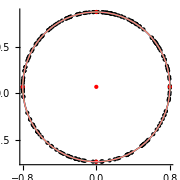

findEllParams[1.5,-1,{{-0.328453,0.727385},{0.563988,-0.564713},{0.727532,0.328134},{-0.779776,0.170072},{0.018478,0.79789},{-0.0355028,-0.797324},{0.790838,0.10748},{-0.701857,0.379961},{0.784838,-0.144946},{-0.582025,0.546095},{0.779453,0.171548},{-0.728111,0.326847},{0.118836,0.789207},{-0.225033,-0.765732},{0.63827,0.47915},{-0.797461,-0.0321588},{0.772809,0.199354},{-0.738756,0.302017},{-0.179231,0.777719},{0.333035,-0.725308},{0.00241734,0.7981},{-0.00464586,-0.7981},{0.743166,0.290997},{-0.76963,0.211293},{0.0697956,0.795046},{-0.133463,-0.786875},{0.276524,0.748669},{-0.490564,-0.629548},{-0.209939,0.769997},{0.385241,-0.69898},{0.162013,0.781487},{-0.302904,-0.7384},{0.12261,0.78863},{-0.231956,-0.763663},{0.4354,0.668878},{-0.687013,-0.406195},{0.786806,-0.133851},{-0.587731,0.539949},{-0.276086,0.74883},{0.489912,-0.630056},{0.727552,0.328089},{-0.779765,0.170123},{-0.286397,0.744948},{0.505152,-0.617904},{-0.0352609,0.797325},{0.0676854,-0.795238},{0.78875,-0.121872},{-0.59385,0.533212},{0.239396,0.761354},{-0.43326,-0.670276},{0.438759,0.66668},{-0.69021,-0.400738},{-0.181908,0.777097},{0.337668,-0.723164},{0.753871,-0.262028},{-0.519452,0.605922},{0.389253,0.696744},{-0.638868,-0.478361},{0.653083,0.458755},{-0.798108,-0.0010186},{0.795999,-0.0580016},{-0.625733,0.49541},{0.390325,0.696145},{-0.640074,-0.476747},{0.720841,-0.342592},{-0.473604,0.642394},{0.149351,0.784005},{-0.28039,-0.747239},{-0.288492,0.744139},{0.508211,-0.615391},{-0.131031,0.787274},{0.247331,-0.758823},{-0.121161,0.788854},{0.2293,-0.764465},{-0.371409,0.706418},{0.618201,-0.504787},{0.766139,0.223623},{-0.747611,0.279379},{-0.0758613,0.79449},{0.144928,-0.784845},{0.385248,0.698967},{-0.634327,-0.484368},{0.697419,0.388048},{-0.792176,0.09713},{0.433163,0.670329},{-0.68486,-0.409815},{-0.314498,0.733527},{0.545074,-0.582991},{-0.190203,0.775108},{0.351925,-0.716334},{0.681324,-0.415667},{-0.42953,0.672663},{0.798109,0.000683248},{-0.653882,0.457614},{0.421437,0.677762},{-0.67327,-0.42859},{0.682658,0.413464},{-0.795579,0.0634857},{0.798044,0.0102123},{-0.658343,0.451174},{0.469336,0.645519},{-0.717341,-0.349861},{-0.0279645,0.797614},{0.0537058,-0.796305},{0.699002,-0.385198},{-0.448236,0.660345},{0.601178,0.524936},{-0.790848,-0.107412},{0.511259,0.612851},{-0.748591,-0.276752},{0.202608,0.771958},{-0.372968,-0.705606},{0.79409,-0.0799975},{-0.614895,0.508799},{-0.325142,0.728871},{0.559557,-0.569104},{0.798028,-0.0113557},{-0.648202,0.465626},{0.644845,0.470264},{-0.797896,-0.0184212},{0.369977,0.707169},{-0.616494,-0.506871},{0.755347,-0.257743},{-0.521822,0.603882},{-0.184443,0.776499},{0.34204,-0.721106},{0.742869,0.291755},{-0.769853,0.210479},{0.269595,0.751192},{-0.480159,-0.63752},{-0.404375,0.688078},{0.6555,-0.455305},{-0.298485,0.740187},{0.522618,-0.603203},{0.471822,0.643704},{-0.719388,-0.345632},{-0.293564,0.742152},{0.515561,-0.609246},{0.161405,0.781613},{-0.30183,-0.738839},{0.168223,0.780174},{-0.313838,-0.733819},{0.0785301,0.794231},{-0.14996,-0.783899},{0.653523,0.458127},{-0.798109,-0.0000819245},{0.603988,0.521701},{-0.791586,-0.101834},{0.349277,0.717619},{-0.591039,-0.536336},{0.793542,0.0852566},{-0.692266,0.397167},{0.159716,0.78196},{-0.298841,-0.740053},{0.388973,0.696901},{-0.638552,-0.478783},{-0.278351,0.747991},{0.493286,-0.627418},{0.775569,0.18833},{-0.734596,0.311999},{-0.208172,0.770477},{0.382295,-0.700597},{0.628305,0.492144},{-0.796365,-0.0527356},{0.738078,-0.303681},{-0.496065,0.625212},{0.0997207,0.79185},{-0.189668,-0.775249},{0.740109,-0.298697},{-0.498898,0.622954},{0.0978616,0.792081},{-0.186204,-0.776088},{0.192221,0.77461},{-0.355371,-0.71463},{0.0644782,0.795495},{-0.123388,-0.788518},{-0.176026,0.77845},{0.327472,-0.727837},{-0.0321683,0.797455},{0.0617628,-0.79572},{0.671267,0.431711},{-0.797192,0.0382309},{0.143373,0.78512},{-0.269664,-0.751177},{0.685437,0.408839},{-0.795056,0.069737},{0.116146,0.789607},{-0.220085,-0.767169},{0.642037,0.47409},{-0.797739,-0.0243044},{0.117596,0.789393},{-0.222752,-0.766398},{0.303739,0.738047},{-0.530073,-0.596662},{-0.105541,0.791095},{0.200485,-0.772522},{0.213065,0.769138},{-0.390436,-0.696092},{-0.180654,0.777389},{0.335501,-0.724171}},n/a]

```mathematica
Module[{d=dsolChapple[rOvR[1.5]],cd,foci,minX,maxX,minY,maxY,midX,midY},
foci=Flatten[(cd=chappleData[d,#+.001];
cd["cb"]["foci"])&/@RandomReal[{0,360},100],1];
maxX=Max[First/@foci];
minX=Min[First/@foci];
maxY=Max[Second/@foci];
minY=Min[Second/@foci];
midX=(minX+maxX)/2;
midY=(minY+maxY)/2;
Print@Graphics[{PointSize@Small,Point@foci,PointSize@Large,Red,Point@{{midX,midY},{minX,midY},{maxX,midY},{midX,minY},{midX,maxY}},
Blue,Circle[{midX,midY},maxX-midX],Darker@Green,Circle[{midX,midY},maxY-midY],Thick,Pink,Circle[{midX,midY},{maxX-midX,maxY-midY}]},ImageSize->Small,AspectRatio->Automatic,Axes->True];
findEllParams[1.5,-1,(#-{midX,midY})&/@foci,"n/a"]]
```

```mathematica
getChappleExcInter[d_?NumberQ,tDeg_?NumberQ]:=Module[{cd,tri,exc,excReflX9,inter},
cd=chappleData[d,tDeg+.001];
tri=cd["tri"];
exc=cd["exc"];
excReflX9=(2cd["x9"]-#)&/@exc;
inter=interRays[exc[[1]],exc[[2]]-exc[[1]],excReflX9[[1]],excReflX9[[3]]-excReflX9[[1]]];
<|"tri"->tri,"exc"->exc,"excRefl"->excReflX9,"inter"->inter,"x9"->cd["x9"]|>]
```

```mathematica
showInterExcChapple[r_,tDeg_]:=Module[{ci},
ci=getChappleExcInter[dsolChapple[r],tDeg];
Graphics[{FaceForm@None,PointSize@Large,MapThread[drawPoly[#1,#2]&,{{ci["tri"],ci["exc"],ci["excRefl"]},{Blue,Darker@Green,Directive[Dashed,Darker@Green]}}],
Darker@Red,Point@ci["inter"],Circle[#,.1]&/@ci["exc"][[{1,2}]],Blue,Circle[#,.1]&/@ci["excRefl"][[{1,3}]],Black,Point@ci["x9"]},Axes->True]]
```

```mathematica
DynamicModule[{locus,r=rOvR[1.5],d},
Manipulate[
d=dsolChapple[r];
locus=Quiet@ParametricPlot[getChappleExcInter[d,tDeg2+.001]["inter"],{tDeg2,0,360},PlotStyle->Red,PerformanceGoal->"Speed"];
Dynamic@Show[{locus,showInterExcChapple[r,tDeg]},PlotRange->{{-2,2},{-2,2}}],{tDeg,0,360}]]
```

## [slow] Chapple Invariance Tests

### Which triangle centers are stationary for main, exc, tangental, excMed tris? r/R ≤2, if r/R<Sqrt[2]-1 no obtuse, let’s try this first

```mathematica
Clear@getStoppedPoints;getStoppedPoints[r_,triName_]:=Module[{rmin=Sqrt[2]-1.,d,cp1,cp2,t1=13.,t2=27.,nc1,nc2,names,ds,neglPos},
d=dsolChapple[r];
cp1=chappleData[d,t1];
cp2=chappleData[d,t2];
nc1=newCentersLow[cp1[triName],triLengthsRL@cp1[triName]];
names=First/@nc1;
nc1=Third/@nc1;
nc2=Third/@newCentersLow[cp2[triName],triLengthsRL@cp2[triName]];
ds=MapThread[magn2[#1-#2]&,{nc1,nc2}];
neglPos=First/@Position[ds,d_/; negl[d]];
names[[neglPos]]]
```

#### Note : if r > Sqrt[2] - 1 ≃ .41, there will be obtuse tris

```mathematica
getStoppedPoints[.33,"tri"]
```

{X(1),X(3),X(35),X(36),X(40),X(46),X(55),X(56),X(57),X(65)}

```mathematica
getStoppedPoints[.33,"exc"]
```

{X(2),X(3),X(4),X(5),X(20),X(22),X(23),X(24),X(25),X(26)}

```mathematica
getStoppedPoints[.33,"tangential"]
```

Set::shape: Lists {a, b, c} and {} are not the same shape.

{X(1),X(1),X(2),X(2),X(3),X(3),X(4),X(4),X(5),X(5),X(6),X(6),X(7),X(7),X(8),X(8),X(9),X(9),X(10),X(10),X(11),X(11),X(12),X(12),X(13),X(13),X(14),X(14),X(15),X(15),X(16),X(16),X(17),X(17),X(18),X(18),X(19),X(19),X(20),X(20),X(21),X(21),X(22),X(22),X(23),X(23),X(24),X(24),X(25),X(25),X(26),X(26),X(27),X(27),X(28),X(28),X(29),X(29),X(30),X(30),X(31),X(31),X(32),X(32),X(33),X(33),X(34),X(34),X(35),X(35),X(36),X(36),X(37),X(37),X(38),X(38),X(39),X(39),X(40),X(40),X(41),X(41),X(42),X(42),X(43),X(43),X(44),X(44),X(45),X(45),X(46),X(46),X(47),X(47),X(48),X(48),X(49),X(49),X(50),X(50),X(51),X(51),X(52),X(52),X(53),X(53),X(54),X(54),X(55),X(55),X(56),X(56),X(57),X(57),X(58),X(58),X(59),X(59),X(60),X(60),X(61),X(61),X(62),X(62),X(63),X(63),X(64),X(64),X(65),X(65),X(66),X(66),X(67),X(67),X(68),X(68),X(69),X(69),X(70),X(70),X(71),X(71),X(72),X(72),X(73),X(73),X(74),X(74),X(75),X(75),X(76),X(76),X(77),X(77),X(78),X(78),X(79),X(79),X(80),X(80),X(81),X(81),X(82),X(82),X(83),X(83),X(84),X(84),X(85),X(85),X(86),X(86),X(87),X(87),X(88),X(88),X(89),X(89),X(90),X(90),X(91),X(91),X(92),X(92),X(93),X(93),X(94),X(94),X(95),X(95),X(96),X(96),X(97),X(97),X(98),X(98),X(99),X(99),X(100),X(100)}

```mathematica
getStoppedPoints[.33,"excMed"]
```

{X(2),X(3),X(4),X(5),X(20),X(22),X(23),X(24),X(25),X(26)}

```mathematica
Module[{first,rest},
first=getChappleHyps[.33,.1,addHeader->True];
rest=getChappleHyps[.33,#+.1,addHeader->False]&/@Range[1,1];
Flatten[Join[{first},rest],1]]//TableForm
```

d | tDeg | name | a | b | c | det | discr | majorAxis | norm
0.33 | 0.1 | F | 0.0263733 | 0.0263733 | 0.0372975 | -2.06701×10^6 | -2.06701×10^6 | -0.708344
0.705867 | 1.
0.33 | 0.1 | J | 0.0311684 | 0.0311684 | 0.0440787 | -1.0596×10^6 | -1.0596×10^6 | -0.708589
0.705622 | 1.
0.33 | 0.1 | F_exc | 0.0651782 | 0.0651782 | 0.0921759 | -55410.3 | -55410.3 | -0.708456
0.705755 | 1.
0.33 | 0.1 | J_exc | 0.0558768 | 0.0558768 | 0.0790217 | -102583. | -102583. | -0.708344
0.705867 | 1.
0.33 | 1.1 | F | 0.0874601 | 0.0874601 | 0.123687 | -17090.7 | -17090.7 | -0.720601
0.69335 | 1.
0.33 | 1.1 | J | 0.103326 | 0.103326 | 0.146126 | -8773.12 | -8773.12 | -0.723235
0.690602 | 1.
0.33 | 1.1 | F_exc | 0.216122 | 0.216122 | 0.305643 | -458.358 | -458.358 | -0.721809
0.692092 | 1.
0.33 | 1.1 | J_exc | 0.185301 | 0.185301 | 0.262055 | -848.189 | -848.189 | -0.720601
0.69335 | 1.

```mathematica
Clear@ratioFocalsAll;
ratioFocalsAll[d_]:=Module[{ss,hyp,names},
names={"F","J","F_exc","J_exc"};
ss=Subsets[Range@4,{2}];
getStats[Table[
hyp=getChappleHyps[d,tDeg];
hyp[[#[[1]],6]]/hyp[[#[[2]],6]],{tDeg,1,81,1}],label->Part[names,#]]&/@ss]
```

#### The last two coefficients bx & by are *always* zero

```mathematica
Module[{ons,exc,excL},
ons=orbitNormals[2,toRad@21.];
exc=excentralTriangle[ons[[1]],ons[[3]]];
excL=triLengthsRL@exc;
Print["F: ",Chop[getFeuerbachHyp[ons[[1]],ons[[3]]]["coeffs"]]];
Print["Fexc: ",Chop[getFeuerbachHyp[exc,excL]["coeffs"]]];
Print["J: ",Chop[getJerabekHyp[ons[[1]],ons[[3]]]["coeffs"]]];
Print["Jexc: ",Chop[getJerabekHyp[exc,excL]["coeffs"]]];
]
```

F: {0,0,-6.2925,0,0}

Fexc: {0.0575758,-0.0575758,-0.338239,0,0}

J: {-0.821567,0.821567,2.18339,0,0}

Jexc: {0,0,-0.718573,0,0}

#### If the two triangles don' t belong to the same "set" the ratio of their focal lengths does not remain constant!

```mathematica
Module[{ons1,ons2,h1,h2},
ons1=orbitNormals[1.5,toRad@10.];

ons2=orbitNormals[2,toRad@20.];
h1=getHypsLow[ons1[[1]],ons1[[3]]];
h2=getHypsLow[ons2[[1]],ons2[[3]]];
{h1[[4,6]]/h1[[1,6]],h2[[4,6]]/h2[[1,6]]}]
```

{2.34836,2.95921}

```mathematica
Module[{ons1,ons2,h1,h2},
ons1=orbitNormals[1.5,toRad@10.];
ons2=orbitNormals[2,toRad@20.];
h1=getHypsLow[ons1[[1]],ons1[[3]]];
h2=getHypsLow[ons2[[1]],ons2[[3]]];
{h1[[4,7]]/h1[[1,7]],h2[[4,7]]/h2[[1,7]]}]
```

{0.0328805,0.0130405}

```mathematica
Clear@ratioDetsAll;ratioDetsAll[d_]:=Module[{ss,hyp,names},
names=names={"F","J","F_exc","J_exc"};
ss=Subsets[Range@4,{2}];
getStats[Table[
hyp=getChappleHyps[d,tDeg];
hyp[[#[[1]],7]]/hyp[[#[[2]],7]],{tDeg,1,81,1}],label->Part[names,#]]&/@ss]
```

```mathematica
Clear@dotAxesAll;dotAxesAll[d_]:=Module[{ss,hyp,names},
names={"F","J","F_exc","J_exc"};
ss=Subsets[Range@4,{2}];
getStats[Table[
hyp=getChappleHyps[d,tDeg];
hyp[[#[[1]],9]].hyp[[#[[2]],9]],{tDeg,1,81,1}],label->Part[names,#]]&/@ss]
```

```mathematica
dotAxesAll[.33]//TableForm
```

<|n→81,mean→0.998209,sd→0.00119887,z→0.00120102,min→0.996569,max→0.999994,median→0.998156,label→{F,J}|>
<|n→81,mean→0.99955,sd→0.000302119,z→0.000302255,min→0.999135,max→0.999999,median→0.999535,label→{F,F_exc}|>
<|n→81,mean→1.,sd→1.23505×10^-16,z→1.23505×10^-16,min→1.,max→1.,median→1.,label→{F,J_exc}|>
<|n→81,mean→0.999553,sd→0.000302084,z→0.000302219,min→0.999135,max→0.999998,median→0.99955,label→{J,F_exc}|>
<|n→81,mean→0.998209,sd→0.00119887,z→0.00120102,min→0.996569,max→0.999994,median→0.998156,label→{J,J_exc}|>
<|n→81,mean→0.99955,sd→0.000302119,z→0.000302255,min→0.999135,max→0.999999,median→0.999535,label→{F_exc,J_exc}|>

```mathematica
ratioDetsAll[.33]//TableForm
```

<|n→81,mean→0.7132,sd→0.637664,z→0.894089,min→0.0883319,max→1.94854,median→0.445191,label→{F,J}|>
<|n→81,mean→23.8774,sd→8.42912,z→0.353016,min→13.1769,max→37.2898,median→22.5207,label→{F,F_exc}|>
<|n→81,mean→20.1496,sd→6.07416×10^-13,z→3.01453×10^-14,min→20.1496,max→20.1496,median→20.1496,label→{F,J_exc}|>
<|n→81,mean→65.4984,sd→43.702,z→0.667223,min→19.1373,max→149.175,median→50.5867,label→{J,F_exc}|>
<|n→81,mean→77.457,sd→72.0428,z→0.930101,min→10.3409,max→228.113,median→45.2607,label→{J,J_exc}|>
<|n→81,mean→0.959228,sd→0.342097,z→0.356638,min→0.540353,max→1.52916,median→0.894715,label→{F_exc,J_exc}|>

```mathematica
ratioFocalsAll[.33]//TableForm
```

<|n→81,mean→1.27654,sd→0.339979,z→0.266328,min→0.846394,max→1.8343,median→1.22423,label→{F,J}|>
<|n→81,mean→0.461531,sd→0.0418777,z→0.0907366,min→0.404672,max→0.524864,median→0.459044,label→{F,F_exc}|>
<|n→81,mean→0.47199,sd→3.59643×10^-15,z→7.6197×10^-15,min→0.47199,max→0.47199,median→0.47199,label→{F,J_exc}|>
<|n→81,mean→0.378813,sd→0.066464,z→0.175453,min→0.286138,max→0.478112,median→0.374965,label→{J,F_exc}|>
<|n→81,mean→0.396682,sd→0.104375,z→0.263119,min→0.257314,max→0.557649,median→0.38554,label→{J,J_exc}|>
<|n→81,mean→1.03101,sd→0.0933051,z→0.090499,min→0.899263,max→1.16635,median→1.0282,label→{F_exc,J_exc}|>

```mathematica
ratioFocalsJexcF[d_,tDeg_]:=Module[{hyp},
hyp=getChappleHyps[d,tDeg,addHeader->False];
hyp[[4,6]]/hyp[[1,6]]]
```

```mathematica
ratioFocalsFexcJ[d_,tDeg_]:=Module[{hyp},
hyp=getChappleHyps[d,tDeg,addHeader->False];
hyp[[3,6]]/hyp[[2,6]]]
```

#### Ratio of focal lengths from (F,Jexc) is maintained

```mathematica
getStats[Table[ratioFocalsJexcF[.33,tDeg],{tDeg,1,181,10}]]
```

<|n→19,mean→2.11869,sd→1.19932×10^-13,z→5.66069×10^-14,min→2.11869,max→2.11869,median→2.11869,label→|>

```mathematica
getStats[Table[ratioFocalsFexcJ[.33,tDeg],{tDeg,1,181,10}]]
```

<|n→19,mean→2.77615,sd→0.5202,z→0.187382,min→2.09119,max→3.49613,median→2.71147,label→|>

```mathematica
getChappleHyps[.33,20.]//TableForm
```

0.33 | 20. | F | 0.358341 | 0.358341 | 0.506771 | -60.6475 | -60.6475 | -0.907427
0.420211 | 1.
0.33 | 20. | J | 0.380851 | 0.380851 | 0.538604 | -47.5315 | -47.5315 | -0.931263
0.364347 | 1.
0.33 | 20. | F_exc | 0.854623 | 0.854623 | 1.20862 | -1.87457 | -1.87457 | -0.919084
0.394062 | 1.
0.33 | 20. | J_exc | 0.759213 | 0.759213 | 1.07369 | -3.00985 | -3.00985 | -0.907427
0.420211 | 1.

## Movie Utils

```mathematica
showPoristicHyps=True;
If[showPoristicHyps,
Module[{degStep=.2,imgs,d=dsolChapple@rOvR[1.5],eps=.001},
(*tpLocus=Quiet@ParametricPlot[getMacBeathTouchpoints[a,tDeg2][[1]],{tDeg2,0,360},PlotStyle->Directive[Thick,Orange],PerformanceGoal->"Quality"];*)
imgs=Table[oneFrameHyps[d,tDeg+eps],{tDeg,0,360,degStep}];
makeMovie["poristic hyps v2.mov",Join[imgs,Reverse@imgs],1]]];
```

Exporting 3602 frames to poristic hyps v2.mov